```mathematica
dataset = Import["http://www-groups.dcs.st-and.ac.uk/history/Indexes/Full_Chron.html",{"Hyperlinks"}];
```

```mathematica
dataset1 =Flatten[StringCases[dataset,"http://www-groups.dcs.st-and.ac.uk/history/Biographies/"~~__]];
```

```mathematica
dataset2 = Import[#,"Text"]&/@dataset1
```

{6706,8997,7335,26071,13189,8342,33967,14134,17034,14494,2755,22932,25623,32677,25710,28993,20588,22485,15680,26426,25808}
 |  |  |  |

## HTML Parser

```mathematica
TemplateApply;

$mapping=Reverse[Normal[Templating`HTML`PackagePrivate`$SafeHTMLEntities],{2}];

htmlToText[txt_String]:=StringReplace[txt,$mapping]
```

```mathematica
htmls= Map[htmlToText,dataset2]
```

{6706,8997,7335,26071,13163,8342,33967,14134,17034,14494,2755,22907,25464,32564,25656,28923,20469,22478,15680,26396,25787}
 |  |  |  |

## Exporting List of HTMLs

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\tanha\OneDrive\Documents\GitHub\Summer2018\StudentDeliverables

```mathematica
Export["htmlbiographies.mx",htmls,"MX"]
```

htmlbiographies.mx

```mathematica
Export["listURLs.mx",dataset1,"MX"]
```

listURLs.mx

```mathematica
htmlList = Import["htmlbiographies.mx"];
```

```mathematica
Export["Biography1.m",dataset2]
```

```mathematica
ClearAll[x]
```

```mathematica
fullNames =StringCases[htmlList,"<h1>"~~x__~~"</h1>"->x];
```

```mathematica
birthdate= StringCases[htmlList, "Born:<font color=\"green\"> "~~Shortest[y__]~~"<br>"->y];
```

```mathematica
deathdate=StringCases[htmlList, "<font color=\"purple\">"~~Shortest[z__]~~"</font>"->z];
```

```mathematica
ClearAll[a]
```

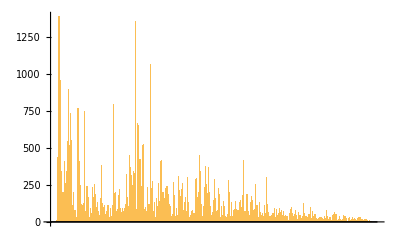

```mathematica
BarChart[Counts[Flatten[StringCases[htmlList,"../Mathematicians/"~~Shortest[a__]~~".html"->a]]]]
```

```mathematica
ClearAll[b]
```

```mathematica
wikiCodeMathematicians= Map[WikipediaData[#,"ArticleWikicode"] &,fullNames[[;;40]]]
```

{[[File:Rhind Mathematical Papyrus.jpg|thumb|A portion of the [[Rhind Mathematical Papyrus]]]]
'''Ahmes''' (more accurately '''Ahmose''') was an [[ancient Egypt]]ian [[scribe]] who lived towards the end of the [[15th Dynasty|Fifteenth Dynasty]] (and of the [[Second Intermediate Period]]) and the beginning of the [[Eighteenth dynasty of Egypt|Eighteenth Dynasty]] (and of the [[New Kingdom]]). He wrote the [[Rhind Mathematical Papyrus]], a work of [[Ancient Egyptian mathematics]] that dates to approximately 1550 BC;<ref>{{Cite web|url=http://www.britishmuseum.org/research/collection_online/collection_object_details.aspx?objectId=110036&partId=1|title=The Rhind Mathematical Papyrus|website=britishmuseum.org|language=en|access-date=2017-09-18}}</ref> he is the earliest contributor to [[mathematics]] whose name is known.<ref>{{citation|title=The Math Book: From Pythagoras to the 57th Dimension, 250 Milestones in the History of Mathematics|first=Clifford A.|last=Pickover|authorlink=Clifford A. Pickover|publisher=Sterling Publishing Company, Inc.|year=2009|isbn=978-1-4027-5796-9|page=36}}.</ref><ref>{{citation|title=Unknown quantity: a real and imaginary history of algebra|first=John|last=Derbyshire|authorlink=John Derbyshire|publisher=National Academies Press|year=2006|isbn=978-0-309-09657-7|page=29}}.</ref>

==References==
{{reflist}}

==External links==
*[http://www.math.tamu.edu/~don.allen/history/egypt/node3.html The Ahmes Papyrus]
*{{MacTutor Biography|id=Ahmes|title=Ahmes}}

{{Authority control}}
{{DEFAULTSORT:Ahmes}}
[[Category:16th-century BC people]]
[[Category:Ancient Egyptian scribes]]
[[Category:Egyptian mathematicians]],{{Hinduism}}
{{Pi box}}
The '''Baudhayana sūtras''' are a group of [[Vedic Sanskrit]] texts which  cover dharma, daily ritual, mathematics, etc. They belong to the ''[[Taittiriya]]'' branch of the  [[Krishna Yajurveda]] school and are among the earliest texts of the ''[[sutra]]'' genre, perhaps compiled in the 8th to 7th centuries BCE.<ref name="Plofker 387">{{cite book | first = Kim | last = Plofker | year = 2007 | page = 387| }}. In relative chronology, they predate  [[Apastamba|Āpastamba]], which is dated by [[Robert Lingat]] to the ''sutra'' period proper,  between c. 500 to 200 BCE. Robert Lingat, The Classical Law of India, (Munshiram Manoharlal Publishers Pvt Ltd, 1993), p.20</ref>

The Baudhayana sūtras consist of six texts:
# the [[Srautasutra|{{IAST|Śrautasûtra}}]], probably in 19 {{IAST|Praśnas}} (questions), 
# the {{IAST|Karmāntasûtra}} in 20 {{IAST|Adhyāyas}} (chapters), 
# the {{IAST|Dvaidhasûtra}} in 4 {{IAST|Praśnas}}, 
# the [[Grhyasutra|Grihyasutra]] in 4 {{IAST|Praśnas}}, 
# the [[Dharmasutra|{{IAST|Dharmasûtra}}]] in 4 {{IAST|Praśnas}} and 
# the [[Sulba Sutras|{{IAST|Śulbasûtra}}]] in 3 {{IAST|Adhyāyas}}.<ref>[http://www.sacred-texts.com/hin/sbe14/sbe1403.htm ''Sacred Books of the East'', vol.14 – Introduction to Baudhayana]</ref>

The '''''{{IAST |Baudhāyana Śulbasûtra}}''''' is noted for  containing several early mathematical results, including  an approximation of the [[square root of 2]] and the statement of a version of the [[Pythagorean theorem]]. 

==Baudhāyana Shrautasūtra==
{{main|Baudhayana Shrauta Sutra}}
His [[Śrauta|shrauta]] sūtras related to performing [[Vedas|Vedic]] [[sacrifice]]s has followers in some [[Smartism|Smārta]] [[brāhmaṇa]]s ([[Iyers]]) and some [[Iyengar]]s of [[Tamil Nadu]], [[Yajurveda|Yajurvedis]] or [[Namboothiri]]s of [[Kerala]], Gurukkal Brahmins (Aadi Saivas), among others.  The followers of this sūtra follow a different method and do 24 Tila-tarpaṇa, as  Lord [[Krishna]] had done tarpaṇa on the day before [[Amavasya|amāvāsyā]];  they call themselves Baudhāyana Amavasya.

==Baudhāyana Dharmasūtra==
The Dharmasūtra of Baudhāyana like that of [[Apastamba]] also forms a part of the larger [[Kalpa Sūtra|Kalpasutra]]. Likewise, it is composed of ''[[praśna]]s'' which literally means ‘questions’ or books. The structure of this Dharmasūtra is not very clear because it came down in an incomplete manner. Moreover, the text has undergone alterations in the form of additions and explanations over a period of time. The ''praśnas'' consist of the [[Srautasutra]] and other ritual treatises, the Sulvasutra which deals with vedic geometry, and the [[Grhyasutra]] which deals with domestic rituals.<ref name="Patrick Olivelle 1999 p.127">Patrick Olivelle, Dharmasūtras: The Law Codes of Ancient India, (Oxford World Classics, 1999), p.127</ref>

There are no commentaries on this Dharmasūtra with the exception of [[Govindasvāmin]]'s ''Vivaraṇa''. The date of the commentary is uncertain but according to Olivelle it is not very ancient. Also the commentary is inferior in comparison to that of Haradatta on Āpastamba and Gautama.<ref name="Patrick Olivelle 1999">Patrick Olivelle, Dharmasūtras: The Law Codes of Ancient India, (Oxford World Classics, 1999), p.xxxi</ref> 

This Dharmasūtra is divided into four books. Olivelle states that Book One and the first sixteen chapters of Book Two are the ‘Proto-Baudhayana’<ref name="Patrick Olivelle 1999 p.127" /> even though this section has undergone alteration. Scholars like Bühler and Kane agree that the last two books of the Dharmasūtra are later additions. Chapter 17 and 18 in Book Two lays emphasis on various types of ascetics and acetic practices.<ref name="Patrick Olivelle 1999 p.127" />

The first book is primarily devoted to the student and deals in topics related to studentship. It also refers to social classes, the role of the king, marriage, and suspension of Vedic recitation. Book two refers to penances, inheritance, women, householder, orders of life, ancestral offerings. Book three refers to holy householders, forest hermit and penances. Book four primarily refers to the yogic practices and penances along with offenses regarding marriage.<ref>Patrick Olivelle, Dharmasūtras: The Law Codes of Ancient India, (Oxford World Classics, 1999), p.128-131</ref>

==Baudhāyana Sulbasūtra==

===Pythagorean theorem===

It is also referred to as Baudhayana theorem.
The most notable of the rules (the Sulbasūtra-s do not contain any axiomatic proof for the rules which they describe since they are sūtra-s, formulae, concise. The statement itself is in the form of an empirical proof.) in the ''Baudhāyana Sulba Sūtra'' says:

<blockquote>
दीर्घचतुरश्रस्याक्ष्णया रज्जु: पार्श्र्वमानी तिर्यग् मानी च यत् पृथग् भूते कुरूतस्तदुभयं करोति ॥<br /><br />
''dīrghachatursrasyākṣaṇayā rajjuḥ pārśvamānī, tiryagmānī,''<br />
''cha yatpṛthagbhūte kurutastadubhayāṅ karoti.''<br />
:A rope stretched along the length of the [[diagonal]] produces an [[area]] which the vertical and horizontal sides make together.<ref>[[Subhash Kak]], Pythagorean Triples and Cryptographic Coding, https://arxiv.org/find/all/1/all:+kak/0/1/0/all/0/1?skip=25&query_id=a7b95a2782affe4b </ref></blockquote>

The lines are to be referring to a rectangle, although some interpretations consider this to refer to a [[Square (geometry)|square]].  In either case, it states that the square of the [[hypotenuse]] equals the sum of the squares of the sides.  If restricted to right-angled isosceles triangles, however, it would constitute a less general claim, but the text seems to be quite open to unequal sides.

If this refers to a rectangle, it is the earliest recorded statement of the [[Pythagorean theorem]].

Baudhāyana also provides a non-axiomatic demonstration using a rope measure of the reduced form of the Pythagorean theorem for an isosceles [[right triangle]]:

:''The cord which is stretched across a square produces an area double the size of the original square.''

Sequences of [[Pythagorean triples]]  used in cryptography as random sequences and for the generation of keys have been dubbed "Baudhayana sequences" in a 2014 paper.<ref>[[Subhash Kak|Kak, S.]] and Prabhu, M. Cryptographic applications of primitive Pythagorean triples. Cryptologia, 38:215-222, 2014. [http://www.tandfonline.com/doi/full/10.1080/01611194.2014.915257#.U5tvAvldXkg ] </ref>

===Circling the square===
Another problem tackled by Baudhāyana is that of finding a circle whose area is the same as that of a square (the reverse of [[squaring the circle]]). His sūtra i.58 gives this construction:

:''Draw half its diagonal about the centre towards the East-West line; then describe a circle together with a third part of that which lies outside the square. ''

Explanation:
*Draw the half-diagonal of the square, which  is larger than the half-side by <math>x = {a \over 2}\sqrt{2}- {a \over 2}</math>.
*Then draw a circle with radius <math>{a \over 2} + {x \over 3}</math>, or <math>{a \over 2} + {a \over 6}(\sqrt{2}-1)</math>, which equals <math>{a \over 6}(2 + \sqrt{2})</math>.
* Now <math>(2+\sqrt{2})^2 \approx 11.66 \approx {36.6\over \pi}</math>, so the area <math>{\pi}r^2 \approx \pi \times {a^2 \over 6^2} \times {36.6\over \pi} \approx a^2</math>.

===Square root of 2===
Baudhāyana i.61-2 (elaborated in Āpastamba Sulbasūtra i.6)
gives the length of the diagonal of a square in terms of its sides, which is equivalent to a formula for the [[square root of 2]]:

:''samasya dvikaraṇī. pramāṇaṃ tṛtīyena vardhayet <br /> tac caturthenātmacatustriṃśonena saviśeṣaḥ''

: The diagonal [lit. "doubler"] of a square. The measure is to be increased by a third and by a fourth decreased by the 34th. That is its diagonal approximately.{{citation needed|date=December 2012}}

That is,

:<math>\sqrt{2} \approx  1 + \frac{1}{3} + \frac{1}{3 \cdot 4} - \frac{1}{3 \cdot4 \cdot 34} = \frac{577}{408} \approx 1.414216,</math>

which is correct to five decimals.<ref name="Baudhayana">O'Connor, "Baudhayana".</ref>

Other theorems include: diagonals of rectangle bisect each other, diagonals of rhombus bisect at right angles, area of a square formed by joining the middle points of a square is half of original, the
midpoints of a rectangle joined forms a rhombus whose area is half the rectangle, etc.

Note the emphasis on rectangles and squares; this arises from the need to specify ''yajña bhūmikā''s—i.e. the altar on which a rituals were conducted, including fire offerings (yajña).  This is an aspect of Vaastu Shastras and Shilpa Shastras.  These theroms are derived from those texts.

==See also==
*[[Indian mathematics]]
*[[List of Indian mathematicians]]

==Notes==
{{reflist}}

==References==
* George Gheverghese Joseph. ''The Crest of the Peacock: Non-European Roots of Mathematics'', 2nd Edition. [[Penguin Books]], 2000. {{ISBN|0-14-027778-1}}.
* Vincent J. Katz. ''A History of Mathematics: An Introduction'', 2nd Edition. [[Addison-Wesley]], 1998. {{ISBN|0-321-01618-1}}
* [[S. Balachandra Rao]], ''Indian Mathematics and Astronomy: Some Landmarks''. Jnana Deep Publications, Bangalore, 1998. {{ISBN|81-900962-0-6}}
* {{MacTutor Biography|id=Baudhayana}} [[St Andrews University]], 2000.
* {{MacTutor Biography|id=Indian_sulbasutras|title=The Indian Sulbasutras|class=HistTopics}} St Andrews University, 2000.
* Ian G. Pearce. [http://turnbull.mcs.st-and.ac.uk/~history/Projects/Pearce/Chapters/Ch4_2.html ''Sulba Sutras''] at the [[MacTutor archive]]. St Andrews University, 2002.
* B.B. Dutta."The Science of the Shulba".
{{refend}}

{{Indian mathematics}}

{{Authority control}}
[[Category:Ancient Indian mathematicians]]
[[Category:Pi]]
[[Category:Indian mathematics]],{{For|the heir to [[Shashanka]]'s kingdom|Manava (king)}}
{{Refimprove|article|date=January 2008}}

'''Manava''' (c. 750 BC &ndash; 690 BC) is an author of the [[Hindu]] [[Geometry|geometric]] text of ''[[Sulba Sutras]].''

The Manava [[Sulbasutra]] is not the oldest (the one by [[Baudhayana]] is older), nor is it one of the most important, there being at least three Sulbasutras which are considered more important. Historians place his lifetime at around 750 BC.

Manava would have not have been a mathematician in the sense that we would understand it today. Nor was he a scribe who simply copied manuscripts like [[Ahmes]]. He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes. Undoubtedly he wrote the ''Sulbasutra'' to provide rules for religious rites and it would appear almost a certainty that Manava himself would be a [[Hindu]] priest.

The mathematics given in the ''Sulbasutras'' is there to enable accurate construction of altars needed for sacrifices. It is clear from the writing that Manava, as well as being a priest, must have been a skilled craftsman.

Manava's ''Sulbasutra,'' like all the ''Sulbasutras,'' contained approximate constructions of circles from rectangles, and squares from circles, which can be thought of as giving approximate values of π. There appear therefore different values of π throughout the ''Sulbasutra,'' essentially every construction involving circles leads to a different such approximation. The paper of R.C. Gupta is concerned with an interpretation of verses 11.14 and 11.15 of Manava's work which give π = 25/8 = 3.125.

==External links==
*{{MacTutor Biography|id=Manava}}

==References==
{{reflist}}
*Gupta, R.C. [http://onlinelibrary.wiley.com/doi/10.1111/j.1600-0498.1988.tb00682.x/full ''New Indian Values of π from the Mānava Súlba Sūtra'']. Centaurus. Volume 31, Issue 2, pages 114–125, July 1988

{{Indian mathematics}}

{{Authority control}}
[[Category:Ancient Indian mathematicians]]
[[Category:Geometers]]
[[Category:750s BC births]]
[[Category:690 BC deaths]]


{{Hindu-bio-stub}}
{{India-scientist-stub}}
{{asia-mathematician-stub}},{{other uses|Thales (disambiguation)}}
{{Infobox philosopher
| name = Thales of Miletus
| image = Illustrerad Verldshistoria band I Ill 107.jpg
| birth_date = {{circa}} 624 BC
| death_date = {{circa}} 546 BC (aged {{circa|78}}) <!--PLEASE SEE TALK BEFORE CHANGING DATE (no, really) -->
| era = [[Pre-Socratic philosophy]]
| region = [[Western philosophy]]
| school_tradition = {{hlist|class=nowrap |[[Ionian School (philosophy)|Ionian]]{{\}}[[Milesian school|Milesian]] |[[Naturalism (philosophy)|Naturalism]]}}
| main_interests = {{hlist |[[Ethics]] |[[Metaphysics]] |[[Mathematics]] |[[Astronomy]]}}
| notable_ideas = {{ublist|class=nowrap |Water is the ''[[arche]]'' |[[Thales' theorem]] |[[Intercept theorem]]}}
| influences = {{ublist |[[Babylonian astronomy]] |[[Ancient Egyptian mathematics]] |[[Ancient Egyptian religion]]}}
| influenced = {{hlist |[[Pythagoras]] |[[Anaximander]] |[[Anaximenes of Miletus|Anaximenes]]}}
}}

'''Thales of Miletus''' ({{IPAc-en|ˈ|θ|eɪ|l|iː|z}}; {{lang-el|[[wikt:Θαλῆς|Θαλῆς]] (ὁ Μιλήσιος)}}, ''Thalēs''; {{circa}} 624&nbsp;– c. 546&nbsp;BC) was a [[Pre-Socratic philosophy|pre-Socratic]] [[Greek philosophy|Greek philosopher]], [[Greek Mathematics|mathematician]], and [[astronomer]] from [[Miletus]] in [[Asia Minor]] (present-day [[Milet]] in [[Turkey]]).  He was one of the [[Seven Sages of Greece]]. Many, most notably [[Aristotle]], regarded him as the first philosopher in the [[Greek philosophy|Greek tradition]],<ref>[[Aristotle]], Metaphysics Alpha, 983b18.</ref><ref name="CPM">{{cite DGRBM |title=Thales |year=1870 |url=https://archive.org/stream/dictionaryofgree03smituoft#page/1016  |page=1016}}</ref> and he is otherwise historically recognized as the first individual in [[Western civilization]] known to have entertained and engaged in [[History of science#Greco-Roman world|scientific philosophy]].<ref>Michael Fowler, [http://galileoandeinstein.physics.virginia.edu/lectures/thales.html Early Greek Science: Thales to Plato], University of Virginia [Retrieved 2016-06-16]</ref><ref name="books.google.com">Frank N. Magill, [https://books.google.com/books?id=_CMl8ziTbKYC&pg=PA1121 ''The Ancient World: Dictionary of World Biography'', Volume 1], Routledge, 2003 {{isbn|1135457395}}</ref>

Thales is recognized for breaking from the use of [[mythology]] to explain the world and the universe, and instead explaining natural objects and phenomena by [[Theory|theories]] and [[hypothesis|hypotheses]], in a precursor to modern [[science]]. Almost all the other [[Pre-Socratic philosophy|Pre-Socratic philosophers]] followed him in explaining nature as deriving from a unity of everything based on the existence of a single ultimate substance, instead of using mythological explanations. Aristotle reported Thales' hypothesis that the [[Arche|originating principle]] of [[nature]] and the nature of [[matter]] was a single material [[Substance theory|substance]]: [[Water (classical element)|water]].

In [[mathematics]], Thales used [[geometry]] to calculate the heights of pyramids and the distance of ships from the shore. He is the first known individual to use [[deductive reasoning]] applied to geometry, by deriving four corollaries to [[Thales' theorem]]. He is the first known individual to whom a [[Greek mathematics#Classical period|mathematical discovery]] has been attributed.<ref>{{harv|Boyer|1991|loc="Ionia and the Pythagoreans" p. 43}}</ref>

==Life==
{{See also|Seven Sages of Greece}}
Thales was probably born in the city of Miletus around the mid-620s BC. The ancient writer [[Apollodorus of Athens]]<ref name=Cohenetal>{{cite book|last1=Cohen|first1=Mark S.|last2=Curd|first2=Patricia|last3=Reeve|first3=C. D. C.|date=2011|url=https://books.google.com/books?id=pFEII68kmVsC|title=Readings in Ancient Greek Philosophy (Fourth Edition): From Thales to Aristotle|page=10|location=Indianapolis, Indiana|publisher=Hackett Publishing|isbn=1603846077|ref=harv}}</ref> writing during the 2nd century BC,<ref name="books.google.com"/> thought Thales was born about the year 625 BC.<ref name=Cohenetal/> [[Herodotus]], writing in the fifth century BC, described Thales as "a [[Phoenicia]]n by remote descent".<ref name="Freely2012">{{cite book|url=https://books.google.com/books?id=e4ye9m3EflQC&pg=PA7&dq=Thales+of+Miletus+Phoenician&hl=en&sa=X&ved=0ahUKEwjgxpLr_s_WAhUOU1AKHeAUBWwQ6AEILDAB#v=onepage&q=Thales%20of%20Miletus%20Phoenician&f=false|title=The Flame of Miletus: The Birth of Science in Ancient Greece (And How It Changed the World)|last1=Freely|first1=John|date=2012|publisher=I. B. Tauris & Co. Ltd.|isbn=978-1-78076-051-3|location=London, England|page=7|accessdate=1 October 2017}}</ref> The later historian [[Diogenes Laertius]], in his ''[[Lives and Opinions of Eminent Philosophers|Lives of the Philosophers]]'', references Herodotus, [[Duris of Samos|Duris]], and [[Democritus]], who all agree "that [[Thales]] was the son of Examyas and Cleobulina, and belonged to the Thelidae who are Phoenicians." He then states that "Most writers, however, represent him as a native of Miletus and of a distinguished family."<ref>{{cite book|last=Lawson|first=Russell M.|date=2004|title=Science in the Ancient World: An Encyclopedia|url=https://books.google.com/books?id=1AY1ALzh9V0C&pg=PA234|location=Santa Barbara, California, Denver Colorado, and Oxford, England|publisher=ABC CLIO|isbn=1-85109-534-9|pages=234-235}}</ref><ref>{{Cite web|url=http://www.perseus.tufts.edu/hopper/text?doc=Perseus%3Atext%3A1999.01.0258%3Abook%3D1%3Achapter%3D1|title=Lives of Eminent Philosophers|last=Diogenes Laertius}}</ref><ref>{{Cite web|url=https://books.google.ca/books?id=yjaEkWbwBm0C&pg=PA23&lpg=PA23&dq=herodotus+1.170+examyes&source=bl&ots=KrXVRE3kpd&sig=tErjJKyE5672rvGIc609oJM2vUk&hl=en&sa=X&ved=0ahUKEwi8pYKJ_eXVAhWGjlQKHcUlAooQ6AEIMjAC#v=onepage&q=herodotus%201.170%20examyes&f=false|title=The Pre-Platonic Philosophers|last=Nietzsche|first=Friedrich}}</ref>

===Background===
The dates of Thales' life are not exactly known, but are roughly established by a few datable events mentioned in the sources. According to [[Herodotus]] (and as determined by modern methods) Thales predicted the [[Eclipse of Thales|solar eclipse of May 28, 585&nbsp;BC]].<ref name="1.74.2">Herodotus, [http://www.perseus.tufts.edu/cgi-bin/ptext?lookup=Hdt.+1.74.1 1.74.2], and A. D. Godley's footnote 1; Pliny, [http://www.perseus.tufts.edu/cgi-bin/ptext?lookup=Plin.+Nat.+2.9 2.9 (12)] and Bostock's footnote 2.</ref> [[Diogenes Laërtius]] quotes the chronicle of Apollodorus of Athens as saying that Thales died at the age of 78 during the 58th [[Olympiad]] (548–545&nbsp;BC) and attributes his death to [[heat stroke]] while watching the games. 

Diogenes Laërtius states that "according to Herodotus and Douris and [[Democritus]]", Thales' parents were Examyes and Cleobuline, whose names are indigenous Carian and Greek, respectively.<ref name="Freely2012"/> Diogenes then delivers conflicting reports: one that Thales married and either fathered a son ([[Cybisthus]] or [[Cybisthon]]) or adopted his nephew of the same name; the second that he never married, telling his mother as a young man that it was too early to marry, and as an older man that it was too late. [[Plutarch]] had earlier told this version: [[Solon]] visited Thales and asked him why he remained single; Thales answered that he did not like the idea of having to worry about children. Nevertheless, several years later, anxious for family, he adopted his nephew Cybisthus.<ref>{{cite book |last=Plutarch |title=Lives |year=1952 |publisher=William Benton |location=Chicago |pages=66 |chapter=Solon |editor=Robert Maynard Hutchins |series=Great Books of the Western World |volume=14}}</ref>

Thales involved himself in many activities, taking the role of an innovator. Some say that he left no writings, others say that he wrote ''On the [[Solstice]]'' and ''On the [[Equinox]]''. (No writing attributed to him has survived.) Diogenes Laërtius quotes two letters from Thales: one to [[Pherecydes of Syros]], offering to review his book on religion, and one to [[Solon]], offering to keep him company on his sojourn from{{Clarify|date=February 2017}} [[Athens]]. Thales identifies the Milesians as Athenian [[Colonies in antiquity#Greek colonies|colonists]].<ref>Diogenes Laërtius, 1.43, 44.</ref>

===Engineering===
Thales' principal occupation was [[engineering]].<ref>J J O'Connor and E F Robertson, [http://www-groups.dcs.st-and.ac.uk/~history/Biographies/Thales.html Thales of Miletus], University of St Andrews [Retrieved 2016-06-16]</ref>

He was aware of the existence of the [[lodestone]], and was the first to be connected to knowledge of this in history. According to Aristotle, Thales thought lodestones had souls, because iron is attracted to them (by the force of [[magnetism]]).<ref>Nathan Ida, [https://books.google.com/books?id=YtmIBwAAQBAJ&pg=PA427 ''Engineering Electromagnetics''], Springer, 2015 {{isbn|3319078062}}</ref> According to [[Hieronymus of Rhodes|Hieronymus]], historically quoted by [[Diogenes Laertius]], Thales found the height of pyramids by comparison between the lengths of the shadows cast by a person and by the pyramids.<ref>J J O'Connor and E F Robertson</ref>

===Business===
[[File:Capernaum roman olive press by David Shankbone.jpg|thumb|An olive mill and an olive press dating from Roman times in [[Capernaum, Israel]].]]
Several anecdotes suggest Thales was not just a philosopher, but also a businessman.

A story, with different versions, recounts how Thales achieved riches from an olive harvest by [[Weather forecasting#Ancient forecasting|prediction of the weather]].

In one version, he bought all the [[Olive oil extraction#Traditional method: olive press|olive presses]] in Miletus after predicting the weather and a good harvest for a particular year. Another version of the story has Aristotle explain that Thales had reserved presses in advance, at a discount, and could rent them out at a high price when demand peaked, following his prediction of a particularly good harvest. Aristotle explains that Thales' objective in doing this was not to enrich himself but to prove to his fellow Milesians that philosophy could be useful, contrary to what they thought,<ref>Aristotle, [[Politics (Aristotle)|Politics]] 1259a [http://www.perseus.tufts.edu/cgi-bin/ptext?lookup=Aristot.+Pol.+1.1259a]</ref> or alternatively, Thales had made his foray into enterprise because of a personal challenge put to him by an individual who had asked why, if Thales was an intelligent famous philosopher, he had yet to attain wealth. This first version of the story would constitute the first historically known creation and use of [[Futures contract|futures]], whereas the second version would be the first historically known of creation and use of [[Option (finance)|options]].<ref>George Crawford, Bidyut Sen - ''[https://books.google.com/books?id=NIIVeirctosC&pg=PA7 Derivatives for Decision Makers: Strategic Management Issues]'', John Wiley & Sons, 1996 {{isbn|9780471129943}}</ref>

===Politics===
Thales’ political life had mainly to do with the involvement of the [[Ionians]] in the defense of [[Anatolia]] against the growing power of the [[Achaemenid Empire|Persians]], who were then new to the region. In neighbouring [[Lydia]], a king had come to power: [[Croesus]], who was somewhat too aggressive for the size of his army. He had conquered most of the states of coastal Anatolia, including the cities of the Ionians. The story is told in [[Herodotus]].<ref>[[Herodotus]], Book 1</ref>

The Lydians were at war with the [[Medes]], who were a remnant of the first wave of migration of ancient Iranian peoples, who had subsequently settled into the region, over the issue of refuge the Lydians had given to some [[Scythian]] [[Mercenary|soldiers of fortune]] inimical to the Medes. The war endured for five years, but in the sixth an eclipse of the Sun (mentioned above) spontaneously halted a battle in progress (the [[Battle of Halys (585&nbsp;BC)|Battle of Halys]]).

It seems that Thales had predicted this [[solar eclipse]]. The [[Seven Sages of Greece|Seven Sages]] were most likely already in existence, as Croesus was also heavily influenced by [[Solon]] of [[Athens]], another sage. Whether Thales was present at the battle is not known, nor are the exact terms of the prediction, but based on it the Lydians and Medes made peace immediately, swearing a [[Blood brother|blood oath]].

The Medes were [[Dependent territory|dependencies]] of the [[Achaemenid Empire|Persians]] under [[Cyrus the Great|Cyrus]]. Croesus now sided with the Medes against the Persians and marched in the direction of Iran (with far fewer men than he needed). He was stopped by the river [[Halys River|Halys]], then unbridged. This time he had Thales with him, perhaps by invitation. Whatever his status, the king gave the problem to him, and he got the army across by digging a diversion upstream so as to reduce the flow, making it possible to ford the river. The channels ran around both sides of the camp.

The two armies engaged at [[Pteria (Cappadocia)|Pteria]] in [[Cappadocia]]. As the battle was indecisive but paralyzing to both sides, Croesus marched home, dismissed his mercenaries and sent emissaries to his dependents and allies to ask them to dispatch fresh troops to [[Sardis]]. The issue became more pressing when the Persian army showed up at Sardis. [[Diogenes Laërtius]]<ref>[[Diogenes Laërtius]] 1.25</ref> tells us that Thales gained fame as a counselor when he advised the Milesians not to engage in a symmachia, a "fighting together", with the Lydians. This has sometimes been interpreted as an alliance, but a ruler does not ally with his subjects.

Croesus was defeated before the city of Sardis by Cyrus, who subsequently spared Miletus because it had taken no action. Cyrus was so impressed by Croesus’ wisdom and his connection with the sages that he spared him and took his advice on various matters.

The Ionians were now free. Herodotus says that Thales advised them to form an Ionian state; that is, a bouleuterion ("deliberative body") to be located at [[Teos]] in the center of [[Ionia]]. The Ionian cities should be demoi, or "districts". Miletus, however, received favorable terms from Cyrus. The others remained in an Ionian League of 12 cities (excluding Miletus now), and were subjugated by the Persians.

While Herodotus reported that most of his fellow Greeks believe that Thales did divert the river Halys to assist King Croesus' military endeavors, he himself finds it doubtful.<ref name="Dicks"/>

===Sagacity===
[[File:MiletusIonicStoa.jpg|thumb|The Ionic Stoa on the Sacred Way in Miletus]]
[[Diogenes Laërtius]]<ref>Diogenes Laërtius 1.22</ref> tells us that the [[Seven Sages of Greece|Seven Sages]] were created in the [[archon]]ship of Damasius at [[Athens]] about 582&nbsp;BC and that Thales was the first sage. The same story, however, asserts that Thales emigrated to [[Miletus]]. There is also a report that he did not become a student of [[nature]] until after his political career. Much as we would like to have a date on the seven sages, we must reject these stories and the tempting date if we are to believe that Thales was a native of Miletus, predicted the eclipse, and was with [[Croesus]] in the campaign against [[Cyrus the Great|Cyrus]].

Thales received instruction from an [[Ancient Egypt|Egyptian]] priest. It was fairly certain that he came from a wealthy, established family, in a class which customarily provided higher education for their children. Moreover, the ordinary citizen, unless he was a seafaring man or a merchant, could not afford the grand tour in [[Egypt]], and did not consort with noble lawmakers such as [[Solon]].
[[File:Solar eclipse 1999 4 NR.jpg|thumb|left|Total [[eclipse]] of the [[Sun]]]]
In Diogenes Laërtius' ''Lives of Eminent Philosophers'' Chapter 1.39, Laërtius relates the several stories of an expensive object that is to go to the most [[Wisdom#Philosophical perspectives|wise]]. In one version (that Laërtius credits to [[Callimachus]] in his ''Iambics'') Bathycles of Arcadia states in his will that an expensive bowl "'should be given to him who had done most good by his wisdom.'  So it was given to Thales, went the round of all the sages, and came back to Thales again. And he sent it to [[Didyma|Apollo at Didyma]], with this dedication...'Thales the Milesian, son of Examyas [dedicates this] to Delphinian Apollo after twice winning the prize from all the Greeks.'"<ref>{{harvnb|Laërtius|1925|loc=§ 28}}</ref>

=== Astronomy ===
{{See also|The Astrologer who Fell into a Well}}
Thales predicted the [[Eclipse of Thales|solar eclipse of May 28, 585&nbsp;BC]].<ref name="1.74.2"/> Thales also described the position of [[Ursa Minor]], and thought the constellation might be useful as a guide for navigation at sea. He calculated the duration of the year and the timings of the [[equinoxes]] and [[solstices]]. He is additionally attributed with the first observation of the [[Hyades (star cluster)|Hyades]] and with calculating the position of the [[Pleiades]].<ref>Geoffrey Stephen Kirk, John Earle Raven, Malcolm Schofield - Les philosophes présocratiques : Une histoire critique avec un choix de textes, vol. 16, Fribourg, Saint-Paul, coll. « Vestigia », 1995 {{isbn|978-2-204-05263-4}}</ref> [[Plutarch]] indicates that in his day (c. AD 100) there was an extant work, the ''Astronomy'', composed in verse and attributed to Thales.<ref>Plutarch, ''[[Moralia#Books|De Pythiae oraculis]]'', [http://www.perseus.tufts.edu/hopper/text?doc=Perseus%3Atext%3A2008.01.0247%3Asection%3D18 18.]</ref>

== Theories ==
Early Greeks, and other civilizations before them, often invoked idiosyncratic explanations of natural phenomena with reference to the will of [[Anthropomorphism|anthropomorphic]] [[Deity|gods]] and [[hero]]es. Instead, Thales aimed to explain natural phenomena via rational hypotheses that referenced natural processes themselves. For example, rather than assuming that earthquakes were the result of supernatural whims Thales explained them by hypothesizing that the [[Earth]] floats on water and that earthquakes occur when the Earth is rocked by waves.

Thales was a [[Hylozoism|hylozoist]] (one who thinks that matter is alive,<ref>Farrington, B., 1944 Greek Science. Pelican</ref> i.e. containing soul(s)). Aristotle wrote (''[[De Anima]]'' 411 a7-8) of Thales: ...''Thales thought all things are full of gods''. Aristotle posits the origin of Thales thought on matter generally containing souls, to Thales thinking initially on the fact of, because [[lodestone|magnets]] move iron, the presence of movement of matter indicated this matter contained life.<ref>Garrett Thomson, [https://books.google.com/books?id=aHmuCgAAQBAJ ''Thales to Sextus: An Introduction to Ancient Philosophy''], page 25, Waveland Press, 2015, {{isbn|1478631864}}</ref><ref>Patricia O'Grady, [http://www.iep.utm.edu/thales/#H7 Thales of Miletus], [[Internet Encyclopedia of Philosophy]] [Retrieved 2016-07-01]</ref>

Thales, according to [[Aristotle]], asked what was the nature (Greek ''[[arche]]'') of the object so that it would behave in its characteristic way. [[Physis]] ({{lang|el|φύσις}}) comes from phyein ({{lang|el|φύειν}}), "to grow", related to our word "be".<ref>{{cite encyclopedia |url=http://www.bartleby.com/61/77/P0277700.html |title=physics |archive-url=https://web.archive.org/web/20061222071531/http://www.bartleby.com/61/77/P0277700.html |archive-date=22 December 2006 |publisher=[[Houghton Mifflin Company]] |dictionary=[[The American Heritage Dictionary of the English Language]] |edition=4th |year=2000 |access-date=18 June 2018 |via=[[Bartleby.com]]}}</ref><ref>{{cite encyclopedia |url=http://www.bartleby.com/61/roots/IE62.html |title=be |archive-url=https://web.archive.org/web/20070206143813/http://www.bartleby.com/61/roots/IE62.html |archive-date=6 February 2007 |publisher=[[Houghton Mifflin Company]] |dictionary=[[The American Heritage Dictionary of the English Language]] |edition=4th |year=2000 |access-date=18 June 2018 |via=[[Bartleby.com]]}}</ref> ''(G)natura'' is the way a thing is "born",<ref>The initial g of the archaic Latin gives the root away as [https://web.archive.org/web/20010610085448/http://www.bartleby.com/61/roots/IE143.html *''genə''-], "beget."</ref> again with the stamp of what it is in itself.

Aristotle<ref>Aristotle, ''[[Metaphysics]]'' 983b6</ref> characterizes most of the philosophers "at first" ({{lang|grc|πρῶτον}}) as thinking that the "principles in the form of matter were the only principles of all things", where "principle" is [[arche]], "matter" is [[hyle]] ("wood" or "matter", "material") and "form" is [[eidos (philosophy)|eidos]].

''Arche'' is translated as "principle", but the two words do not have precisely the same meaning. A [[principle]] of something is merely prior (related to pro-) to it either chronologically or logically. An arche (from {{lang|grc|ἄρχειν}}, "to rule") dominates an object in some way. If the arche is taken to be an origin, then specific causality is implied; that is, B is supposed to be characteristically B just because it comes from A, which dominates it.

The archai<!-- surely the reader have to recognize this easily as Greek plural of ἀρχή? --> that Aristotle had in mind in his well-known passage on the first Greek scientists are not necessarily chronologically prior to their objects, but are constituents of it. For example, in pluralism objects are composed of earth, air, fire and water, but those elements do not disappear with the production of the object. They remain as archai within it, as do the atoms of the atomists.

What Aristotle is really saying is that the first philosophers were trying to define the substance(s) of which all material objects are composed. As a matter of fact, that is exactly what modern scientists are attempting to accomplish in nuclear physics, which is a second reason why Thales is described as the first western scientist,{{Citation needed|date=February 2016}} but some contemporary scholars reject this interpretation.<ref>{{cite book |first=Aryeh  |last=Finkelberg |author-link=|year=2017 |url=https://books.google.com/books?id=8kEEDgAAQBAJ |title=Heraclitus and Thales’ Conceptual Scheme: A Historical Study |publisher=[[Brill (publisher)|Brill]] |page=318, fn. 38}}</ref>

===Geometry===
Thales was known for his innovative use of [[geometry]]. His understanding was theoretical as well as practical. For example, he said:

{{quote|
{{transl|el|''Megiston topos: hapanta gar chorei''}} ({{lang|el|Μέγιστον τόπος· ἄπαντα γὰρ χωρεῖ.}})

The greatest is space, for it holds all things.<ref>{{harvnb|Laërtius|1925|loc=§ 35}}</ref>
}}

Topos is in Newtonian-style [[space]], since the verb, chorei, has the connotation of yielding before things, or spreading out to make room for them, which is [[Extension (metaphysics)|extension]]. Within this extension, things have a position. [[Point (geometry)|Points]], [[line (mathematics)|lines]], [[plane (mathematics)|planes]] and [[solid]]s related by [[distance]]s and [[angle]]s follow from this presumption.

Thales understood [[similar triangles]] and [[right triangle]]s, and what is more, used that knowledge in practical ways. The story is told in DL (loc. cit.) that he measured the height of the [[pyramids]] by their shadows at the moment when his own shadow was equal to his height. A right triangle with two equal legs is a 45-degree right triangle, all of which are similar. The length of the pyramid's shadow measured from the center of the pyramid at that moment must have been equal to its height.

This story indicates that he was familiar with the Egyptian ''[[seked]]'', or ''seqed'', the ratio of the run to the rise of a [[slope]] ([[cotangent]]). The ''seked'' is at the base of problems 56, 57, 58, 59 and 60 of the [[Rhind papyrus]] — an ancient Egyptian mathematical document.

In present-day trigonometry, cotangents require the same units for run and rise (base and perpendicular), but the papyrus uses [[cubits]] for rise and [[Palm (measurement)|palms]] for run, resulting in different (but still characteristic) numbers. Since there were 7 palms in a cubit, the ''seked'' was 7 times the cotangent.

To use an example often quoted in modern reference works, suppose the base of a pyramid is 140&nbsp;cubits and the angle of rise 5.25 ''seked''. The Egyptians expressed their fractions as the sum of fractions, but the decimals are sufficient for the example. What is the rise in cubits? The run is 70&nbsp;cubits, 490 palms. X, the rise, is 490 divided by 5.25 or 93{{frac|1|3}} cubits. These figures sufficed for the Egyptians and Thales. We would go on to calculate the cotangent as 70 divided by 93{{frac|1|3}} to get 3/4 or .75 and looking that up in a table of cotangents find that the angle of rise is a few minutes over 53&nbsp;degrees.

Whether the ability to use the ''[[seked]]'', which preceded Thales by about 1000&nbsp;years, means that he was the first to define trigonometry is a matter of opinion. More practically Thales used the same method to measure the distances of ships at sea, said Eudemus as reported by [[Proclus]] ("in Euclidem"). According to Kirk & Raven (reference cited below), all you need for this feat is three straight sticks pinned at one end and knowledge of your altitude. One stick goes vertically into the ground. A second is made level. With the third you sight the ship and calculate the ''seked'' from the height of the stick and its distance from the point of insertion to the line of sight.

The ''seked'' is a measure of the angle. Knowledge of two angles (the ''seked'' and a right angle) and an enclosed leg (the altitude) allows you to determine by similar triangles the second leg, which is the distance.{{citation needed|date=May 2015}}

===Thales' theorems===
[[File:Thales theorem 1.png|thumb|300px|[[Intercept theorem|Thales' theorem]]: <math>\textstyle \frac{DE}{BC} = \frac{AE}{AC } = \frac{AD}{AB}</math>]]
{{Main article|Thales' theorem}} 
{{Main article|Intercept theorem}}
{{See also|Pythagorean theorem}}
There are two theorems of Thales in [[elementary geometry]], one known as [[Thales' theorem]] having to do with a triangle inscribed in a circle and having the circle's diameter as one leg, the other theorem being also called the [[intercept theorem]]. In addition [[Eudemus of Rhodes|Eudemus]] attributed to him the discovery that a circle is [[bisection|bisected]] by its diameter, that the base angles of an isosceles triangle are equal and that [[vertical angles]] are equal. According to a historical Note,<ref>{{cite book |first=William George |last=Shute |first2=William W. |last2=Shirk |first3=George F. |last3=Porter |title=Plane and Solid Geometry |url=https://books.google.es/books?id=DIENAQAAIAAJ |publisher=[[American Book Company (1890)|American Book Company]] |year=1960 |pages=25–27}}</ref> when [[Ancient Egypt#Late Period .28672.E2.80.93332 BC.29|Thales visited Egypt]], he observed that whenever the Egyptians drew two intersecting lines, they would measure the vertical angles to make sure that they were equal. Thales concluded that one could prove that all vertical angles are equal if one accepted some general notions such as: all straight angles are equal, equals added to equals are equal, and equals subtracted from equals are equal.

===Cosmology: water as a first principle===
Thales' most famous philosophical position was his [[cosmology|cosmological]] thesis, which comes down to us through a passage from [[Aristotle]]'s ''[[Metaphysics (Aristotle)|Metaphysics]]''.<ref>{{cite book |author=Aristotle |author-link=Aristotle |title=[[Metaphysics (Aristotle)|Metaphysics]] |others=983 b6 8-11}}</ref> In the work Aristotle unequivocally reported Thales’ [[hypothesis]] about the nature of all [[Matter#Historical development|matter]] – that the [[Arche|originating principle of nature]] was [[Material monism|a single material substance]]: water. Aristotle then proceeded to proffer a number of conjectures based on his own observations to lend some credence to why Thales may have advanced this idea (though Aristotle didn’t hold it himself).

Aristotle laid out his own thinking about [[Hylomorphism|matter and form]] which may shed some light on the ideas of Thales, in ''[[Metaphysics]]'' 983 b6 8–11, 17–21. (The passage contains words that were later adopted by science with quite different meanings.)

{{quote|That from which is everything that exists and from which it first becomes and into which it is rendered at last, its substance remaining under it, but transforming in qualities, that they say is the element and principle of things that are. …For it is necessary that there be some nature ({{lang|el|φύσις}}), either one or more than one, from which become the other things of the object being saved... Thales the founder of this type of philosophy says that it is water.}}

In this quote we see Aristotle's depiction of the problem of change and the definition of [[Substance theory|substance]]. He asked if an object changes, is it the same or different? In either case how can there be a change from one to the other? The answer is that the substance "is saved", but acquires or loses different qualities ({{lang|el|πάθη}}, the things you "experience").

Aristotle conjectured that Thales reached his conclusion by contemplating that the "nourishment of all things is moist and that even the hot is created from the wet and lives by it." While Aristotle's conjecture on why Thales held water as the originating principle of matter is his own thinking, his statement that Thales held it as water is generally accepted as genuinely originating with Thales and he is seen as an incipient matter-and-formist.

Thales thought the Earth must be a flat disk which is floating in an expanse of water.<ref>{{cite EB1911 |url=http://www.britannica.com/biography/Thales-of-Miletus |title=Thales of Miletus}}</ref>

[[Heraclitus (commentator)|Heraclitus Homericus]] states that Thales drew his conclusion from seeing moist substance turn into air, slime and earth. It seems likely that Thales viewed the Earth as solidifying from the water on which it floated and the oceans that surround it.

Writing centuries later, Diogenes Laërtius also states that Thales taught "Water constituted ({{lang|grc|ὑπεστήσατο}}, 'stood under') the principle of all things."<ref>{{cite book |author=Diogenes Laërtius |author-link=Diogenes Laërtius |url=https://en.wikisource.org/wiki/Lives_of_the_Eminent_Philosophers/Book_I#Thales |title=Lives of the Eminent Philosophers | others=Book 1, paragraph 27}}</ref>

[[Aristotle]] considered Thales’ position to be roughly the equivalent to the later ideas of [[Anaximenes of Miletus|Anaximenes]], who held that everything was composed of [[air]].

The 1870 book ''[[Dictionary of Greek and Roman Biography and Mythology]]'' noted<ref name="CPM"/>
{{quote|Thales dogma that water is the origin of things, that is, that it is that out of which every thing arises, and into which every thing resolves itself, Thales may have followed [[Orphism (religion)|Orphic]] cosmogonies, while, unlike them, he sought to establish the truth of the assertion. Hence, Aristotle, immediately after he has called him the originator of philosophy brings forward the reasons which Thales was believed to have adduced in confirmation of that assertion; for that no written development of it, or indeed any book by ''Thales'', was extant, is proved by the expressions which Aristotle uses when he brings forward the doctrines and proofs of the [[Miletus|Milesian]]. (p. 1016)}}

====Influences====
Later [[Scholasticism|scholastic]] thinkers would maintain that in his choice of water Thales was influenced by Babylonian or Chaldean religion, that held that a god had begun creation by acting upon the pre-existing water. Historian Abraham Feldman holds this does not stand up under closer examination. In Babylonian religion the water is lifeless and sterile until a god acts upon it, but for Thales water itself was divine and creative. He maintained that "All things are full of gods", and to understand the nature of things was to discover the secrets of the deities, and through this knowledge open the possibility that one could be greater than the grandest Olympian.<ref name="Feldman">{{cite journal |last=Feldman |first=Abraham |title=Thoughts on Thales |journal=[[The Classical Journal]] |volume=41 |date=October 1945 |pages=4–6 |issue=1 |publisher=[[Classical Association of the Middle West and South]] |issn=0009-8353 |jstor=3292119}}</ref>

Feldman points out that while other thinkers recognized the wetness of the world "none of them was inspired to conclude that everything was ultimately aquatic."<ref name="Feldman"/> He further points out that Thales was "a wealthy citizen of the fabulously rich Oriental port of Miletus...a dealer in the staples of antiquity, wine and oil...He certainly handled the shell-fish of the Phoenicians that secreted the dye of imperial purple."<ref name="Feldman"/> Feldman recalls the stories of Thales measuring the distance of boats in the harbor, creating mechanical improvements for ship navigation, giving an explanation for the [[flooding of the Nile]] (vital to Egyptian agriculture and Greek trade), and changing the course of the river Halys so an army could ford it. Rather than seeing water as a barrier Thales contemplated the Ionian yearly religious gathering for athletic ritual (held on the promontory of Mycale and believed to be ordained by the ancestral kindred of Poseidon, the god of the sea). He called for the Ionian mercantile states participating in this ritual to convert it into a democratic federation under the protection of Poseidon that would hold off the forces of pastoral Persia. Feldman concludes that Thales saw "that water was a revolutionary leveler and the elemental factor determining the subsistence and business of the world"<ref name="Feldman"/> and "the common channel of states."<ref name="Feldman"/>

Feldman considers Thales' environment and holds that Thales would have seen tears, sweat, and blood as granting value to a person's work and the means how life giving commodities travelled (whether on bodies of water or through the sweat of slaves and pack-animals). He would have seen that minerals could be processed from water such as life-sustaining salt and gold taken from rivers. He would’ve seen fish and other food stuffs gathered from it. Feldman points out that Thales held that the lodestone was alive as it drew metals to itself. He holds that Thales "living ever in sight of his beloved sea" would see water seem to draw all "traffic in wine and oil, milk and honey, juices and dyes" to itself, leading him to "a vision of the universe melting into a single substance that was valueless in itself and still the source of wealth."<ref name="Feldman"/> Feldman concludes that for Thales "...water united all things. The social significance of water in the time of Thales induced him to discern through hardware and dry-goods, through soil and sperm, blood, sweat and tears, one fundamental fluid stuff...water, the most commonplace and powerful material known to him."<ref name="Feldman"/> This combined with his contemporary's idea of "[[spontaneous generation]]" allow us to see how Thales could hold that water could be divine and creative.

Feldman points to the lasting association of the theory that "all whatness is wetness" with Thales himself, pointing out that Diogenes Laërtius speaks of a poem, probably a satire, where Thales is snatched to heaven by the sun, "Perhaps it was an elaborate paronomasia based on the fact that ''thal'' was the Phoenician word for dew."<ref name="Feldman"/>

===Beliefs in divinity===
{{See also|Neopythagoreanism|Neoplatonism}}
Thales applied his method to objects that changed to become other objects, such as water into earth (or so he thought). Thales also applied his method to the act of change itself, approaching it through [[lodestone]] and [[amber]] (which, when electrified by rubbing together, also attracts).{{citation needed|date=August 2017}}  As for the ability of a mover to move something else without being changed itself, Thales saw a commonality between that and the power of a living thing to act. The lodestone and the amber must be alive, and if that were so, there could be no difference between the living and the dead. When asked why he didn’t die if there was no difference, he replied "because there is no difference."{{citation needed|date=August 2017}}

Aristotle defined the [[Soul (spirit)|soul]] as the principle of life, that which imbues the matter and makes it live, giving it the animation, or power to act. The idea did not originate with him, as the Greeks in general believed in the distinction between mind and matter, which was ultimately to lead to a distinction not only between body and soul but also between matter and energy.{{citation needed|date=August 2017}}  If things were alive, they must have souls. This belief was no innovation, as the ordinary ancient populations of the Mediterranean did believe that natural actions were caused by divinities. Accordingly, Aristotle and other ancient writers state that Thales believed that "all things were full of gods."<ref>{{cite book |author=Aristotle |author-link=Aristotle |title=[[De Anima]] |page=411a7}}</ref><ref>{{cite book |last=Kirk |first=G. S. |last2=Raven |first2=J. E. |last3=Schofield |first3=M. |title=The Presocratic Philosophers: A Critical History with a Selcetion of Texts |url=https://books.google.es/books?id=kFpd86J8PLsC&pg=PA93 |publisher=[[Cambridge University Press]] |date=December 29, 1983 |pages=93-97 |isbn=9780521274555}}</ref> In their zeal to make him the first in everything some said he was the first to hold the belief, which must have been widely known to be false.{{citation needed|date=August 2017}}  However, Thales was looking for something more general, a universal substance of mind.{{Citation needed|date=December 2014}} That also was in the polytheism of the times. [[Zeus]] was the very personification of supreme [[mind]], dominating all the subordinate manifestations. From Thales on, however, philosophers had a tendency to depersonify or objectify mind, as though it were the substance of animation per se and not actually a god like the other gods. The end result was a total removal of mind from substance, opening the door to a non-divine principle of action.{{citation needed|date=August 2017}}

Classical thought, however, had proceeded only a little way along that path. Instead of referring to the person, Zeus, they talked about the great mind:

{{quote| "Thales", says [[Cicero]],<ref>{{cite book |author=Cicero |author-link=Cicero |title=[[De Natura Deorum]] |page=i.,10}}</ref> "assures that ''water'' is the principle of all things; and that God is that Mind which shaped and created all things from water."}}

The universal mind appears as a Roman belief in [[Virgil]] as well:

{{quote|<poem>
In the beginning, SPIRIT within (spiritus intus) strengthens Heaven and Earth,
The watery fields, and the lucid globe of Luna, and then –
Titan stars; and mind (mens) infused through the limbs
Agitates the whole mass, and mixes itself with GREAT MATTER (magno corpore)<ref>{{cite book |author=Virgil |author-link=Virgil |title=[[Aeneid]] |chapter=vi |pages=724-727}}</ref></poem>}}

According to [[Henry Fielding]], [[Diogenes Laërtius]] (1.35) affirmed that Thales posed "the independent pre-existence of God from all eternity, stating "that God was the oldest of all beings, for he existed without a previous cause even in the way of generation; that the world was the most beautiful of all things; for it was created by God."<ref>{{cite book |last=Fielding |first=Henry |author-link=Henry Fielding |year=1775 |url=https://books.google.com/books?id=C2RVAAAAcAAJ |title=An essay on conversation |publisher=[[John Bell (publisher)|John Bell]] |page=346}}</ref>

==Reputation==
Thales (who died around 30&nbsp;years before the time of [[Pythagoras]] and 300&nbsp;years before [[Euclid]], [[Eudoxus of Cnidus]], and [[Eudemus of Rhodes]]) is often hailed as "the first Greek mathematician".<ref name="gazette"/> While some historians, such as Colin R. Fletcher, point out that there could have been a predecessor to Thales who would've been named in Eudemus' lost book  ''History of Geometry'' it is admitted that without the work "the question becomes mere speculation."<ref name="gazette">{{cite journal |last=Fletcher |first=Colin R. |title= Thales—our founder? |journal=The Mathematical Gazette |publisher=The Mathematical Association |volume=66 |date=December 1982 |page=267 |issue=438}}</ref> Fletcher holds that as there is no viable predecessor to the title of first Greek mathematician, the only question is whether Thales qualifies as a practitioner in that field; he holds that "Thales had at his command the techniques of observation, experimentation, superposition and deduction…he has proved himself mathematician."<ref name="gazette"/>

The evidence for the primacy of Thales comes to us from a book by [[Proclus]] who wrote a thousand years after Thales but is believed to have had a copy of Eudemus' book. Proclus wrote "Thales was the first to go to Egypt and bring back to Greece this study."<ref name="gazette"/> He goes on to tell us that in addition to applying the knowledge he gained in Egypt "He himself discovered many propositions and disclosed the underlying principles of many others to his successors, in some case his method being more general, in others more empirical."<ref name="gazette"/>

Other quotes from Proclus list more of Thales' mathematical achievements:

{{quote|They say that Thales was the first to demonstrate that the circle is bisected by the diameter, the cause of the bisection being the unimpeded passage of the straight line through the centre.<ref name="gazette"/>}}

{{quote|[Thales] is said to have been the first to have known and to have enunciated [the theorem] that the angles at the base of any isosceles triangle are equal, though in the more archaic manner he described the equal angles as similar.<ref name="gazette"/>}}

{{quote|This theorem, that when two straight lines cut one another, the vertical and opposite angles are equal, was first discovered, as Eudemus says, by Thales, though the scientific demonstration was improved by the [[Euclid|writer of ''Elements'']].<ref name="gazette"/>}}

{{quote|Eudemus in his ''History of Geometry'' attributes this theorem [the equality of triangles having two angles and one side equal] to Thales. For he says that the method by which Thales showed how to find the distance of ships at sea necessarily involves this method.<ref name="gazette"/>}}

{{quote|[[Pamphile of Epidaurus|Pamphila]] says that, having learnt geometry from the Egyptians, he [Thales] was the first to inscribe in a circle a right-angled triangle, whereupon he [[Animal sacrifice|sacrificed an ox]].<ref name="gazette"/>}}

In addition to Proclus, [[Hieronymus of Rhodes]] also cites Thales as the first Greek mathematician. Hieronymus held that Thales was able to measure the height of the pyramids by using a [[theorem]] of geometry now known as the [[intercept theorem#Measuring/Survey|intercept theorem]], (after gathering data by using his walking-stick and comparing its shadow to those cast by the pyramids). We receive variations of Hieronymus' story through [[Diogenes Laërtius]],<ref>{{harvnb|Laërtius|1925|loc=§27}}.</ref> [[Pliny the Elder]], and [[Plutarch]].
<ref name="gazette"/><ref>Plutarch, Moralia, The Dinner of the Seven Wise Men, [http://penelope.uchicago.edu/Thayer/E/Roman/Texts/Plutarch/Moralia/Dinner_of_the_Seven*.html#ref5 147A]</ref> Due to the variations among testimonies, such as the "story of the sacrifice of an ox on the occasion of the discovery that the angle on a diameter of a circle is a right angle" in the version told by Diogenes Laërtius being accredited to Pythagoras rather than Thales, some historians (such as D. R. Dicks) question whether such anecdotes have any historical worth whatsoever.<ref name="Dicks">{{cite journal |last=Dicks |first=D. R. |title=Thales |pages=294–309 |journal=The Classical Quarterly |volume=9 |date=November 1959 |issue=2 |doi=10.1017/S0009838800041586}}</ref>

==Influences==
Due to the scarcity of sources concerning Thales and the diversity among the ones we possess, there is a scholarly debate over possible influences on Thales and the Greek mathematicians that came after him.

Historian Roger L. Cooke points out that Proclus does not make any mention of Mesopotamian influence on Thales or Greek geometry, but "is shown clearly in Greek astronomy, in the use of sexagesimal system of measuring angles and in Ptolemy's explicit use of Mesopotamian astronomical observations."<ref name="Cooke"/> Cooke notes that it may possibly also appear in the second book of Euclid's ''Elements'', "which contains geometric constructions equivalent to certain algebraic relations that are frequently encountered in the cuneiform tablets." Cooke notes "This relation however, is controversial."<ref name="Cooke">{{cite book |last=Cooke |first=Roger L. |title=The History of Mathematics: A Brief Course |publisher=John Wiley & Sons, Inc. |year=2005}}</ref>

Historian [[Bartel Leendert van der Waerden|B.L. Van der Waerden]] is among those advocating the idea of Mesopotamian influence, writing "It follows that we have to abandon the traditional belief that the oldest Greek mathematicians discovered geometry entirely by themselves…a belief that was tenable only as long as nothing was known about Babylonian mathematics. This in no way diminishes the stature of Thales; on the contrary, his genius receives only now the honour that is due to it, the honour of having developed a logical structure for geometry, of having introduced proof into geometry."<ref name="gazette"/>

Some historians, such as D. R. Dicks takes issue with the idea that we can determine from the questionable sources we have, just how influenced Thales was by Babylonian sources. He points out that while Thales is held to have been able to calculate an eclipse using a cycle called the "Saros" held to have been "borrowed from the Babylonians", "The Babylonians, however, did not use cycles to predict solar eclipses, but computed them from observations of the latitude of the moon made shortly before the expected syzygy."<ref name="Dicks"/> Dicks cites historian O. Neugebauer who relates that "No Babylonian theory for predicting solar eclipse existed at 600&nbsp;B.C., as one can see from the very unsatisfactory situation 400&nbsp;years later; nor did the Babylonians ever develop any theory which took the influence of geographical latitude into account." Dicks examines the cycle referred to as  'Saros' - which Thales is held to have used and which is believed to stem from the Babylonians. He points out that Ptolemy makes use of this and another cycle in his book ''Mathematical Syntaxis'' but attributes it to Greek astronomers earlier than [[Hipparchus]] and not to Babylonians.<ref name="Dicks"/> Dicks notes Herodotus does relate that Thales made use of a cycle to predict the eclipse, but maintains that "if so, the fulfillment of the 'prediction' was a stroke of pure luck not science".<ref name="Dicks"/> He goes further joining with other historians (F. Martini, J.L. E. Dreyer, O. Neugebauer) in rejecting the historicity of the eclipse story altogether.<ref name="Dicks"/> Dicks links the story of Thales discovering the cause for a solar eclipse with Herodotus' claim that Thales discovered the cycle of the sun with relation to the solstices, and concludes "he could not possibly have possessed this knowledge which neither the Egyptians nor the Babylonians nor his immediate successors possessed."<ref name="Dicks"/> Josephus is the only ancient historian that claims Thales visited Babylonia.

Herodotus wrote that the Greeks learnt the practice of dividing the day into 12 parts, about the ''polos'', and the [[gnomon]] from the Babylonians. (The exact meaning of his use of the word ''polos'' is unknown, current theories include: "the heavenly dome", "the tip of the axis of the celestial sphere", or a spherical concave sundial.) Yet even Herodotus' claims on Babylonian influence are contested by some modern historians, such as L. Zhmud, who points out that the division of the day into twelve parts (and by analogy the year) was known to the Egyptians already in the second millennium, the gnomon was known to both Egyptians and Babylonians, and the idea of the "heavenly sphere" was not used outside of Greece at this time.<ref>{{cite book |last=Zhmud |first=Leonid |title=The Origin of the History of Science in Classical Antiquity |publisher=Die Deutsche Bibliothek |year=2006}}</ref>

Less controversial than the position that Thales learnt Babylonian mathematics is the claim he was influenced by Egyptians. Pointedly historian S. N. Bychkov holds that the idea that the base angles of an isosceles triangle are equal likely came from Egypt. This is because, when building a roof for a home - having a cross section be exactly an isosceles triangle isn't crucial (as it's the ridge of the roof that must fit precisely), in contrast a symmetric square pyramid cannot have errors in the base angles of the faces or they will not fit together tightly.<ref name="Cooke"/>
Historian D.R. Dicks agrees that compared to the Greeks in the era of Thales, there was a more advanced state of mathematics among the Babylonians and especially the Egyptians - "both cultures knew the correct formulae for determining the areas and volumes of simple geometrical figures such as triangles, rectangles, trapezoids, etc.; the Egyptians could also calculate correctly the volume of the frustum of a pyramid with a square base (the Babylonians used an incorrect formula for this), and used a formula for the area of a circle...which gives a value for [[Pi|π]] of 3.1605--a good approximation."<ref name="Dicks"/> Dicks also agrees that this would have had an effect on Thales (whom the most ancient sources agree was interested in mathematics and astronomy) but he holds that tales of Thales' travels in these lands are pure myth.

The ancient civilization and massive monuments of Egypt had "a profound and ineradicable impression on the Greeks". They attributed to Egyptians "an immemorial knowledge of certain subjects" (including geometry) and would claim Egyptian origin for some of their own ideas to try and lend them "a respectable antiquity" (such as the [[Hermetica|"Hermetic" literature]] of the Alexandrian period).<ref name="Dicks"/>

Dicks holds that since Thales was a prominent figure in Greek history by the time of Eudemus but "nothing certain was known except that he lived in Miletus".<ref name="Dicks"/>  A tradition developed that as "Milesians were in a position to be able to travel widely" Thales must have gone to Egypt.<ref name="Dicks"/> As Herodotus says Egypt was the birthplace of geometry he must have learnt that while there. Since he had to have been there, surely one of the theories on Nile Flooding laid out by Herodotus must have come from Thales. Likewise as he must have been in Egypt he had to have done something with the Pyramids - thus the tale of measuring them. Similar apocryphal stories exist of Pythagoras and Plato traveling to Egypt with no corroborating evidence.

As the Egyptian and Babylonian geometry at the time was "essentially arithmetical", they used actual numbers and "the procedure is then described with explicit instructions as to what to do with these numbers" there was no mention of how the rules of procedure were made, and nothing toward a logically arranged corpus of generalized geometrical knowledge with analytical 'proofs' such as we find in the words of Euclid, Archimedes, and Apollonius."<ref name="Dicks"/> So even had Thales traveled there he could not have learnt anything about the theorems he is held to have picked up there (especially because there is no evidence that any Greeks of this age could use Egyptian hieroglyphics).<ref name="Dicks"/>

Likewise until around the second century BC and the time of Hipparchus (c. 194-120&nbsp;BC) the Babylonian general division of the circle into 360&nbsp;degrees and their sexagesimal system was unknown.<ref name="Dicks"/>  Herodotus says almost nothing about Babylonian literature and science, and very little about their history. Some historians, like P. Schnabel, hold that the Greeks only learned more about Babylonian culture from Berossus, a Babylonian priest who is said to have set up a school in Cos around 270&nbsp;BC (but to what extent this had in the field of geometry is contested).

Dicks points out that the primitive state of Greek mathematics and astronomical ideas exhibited by the peculiar notions of Thales' successors (such as Anaximander, Anaximenes, Xenophanes, and Heraclitus), which historian J. L. Heiberg calls "a mixture of brilliant intuition and childlike analogies",<ref>{{cite book |last=Gesch |first=J. L. |title=D. Math. Und Naturwiss. im Altertum |location=Munich |year=1925 |page=50}}</ref> argues against the assertions from writers in late antiquity that Thales discovered and taught advanced concepts in these fields.

[[John Burnet (classicist)|John Burnet]] (1892) noted<ref>{{cite book |last=Burnet |first=John |url=https://archive.org/details/earlygreekphilo01burngoog |title=Early Greek Philosophy |page=29 |year=1892}}</ref>
{{quote|Lastly, we have one admitted instance of a philosophic guild, that of the [[Pythagoreans]]. And it will be found that the hypothesis, if it is to be called by that name, of a regular organisation of scientific activity will alone explain all the facts. The development of doctrine in the hands of ''Thales'', [[Anaximander]], and [[Anaximenes of Miletus|Anaximenes]], for instance, can only be understood as the elaboration of a single idea in a school with a continuous tradition.}}

== Interpretations ==
In the long sojourn of philosophy, there has existed hardly a philosopher or historian of philosophy who did not mention Thales and try to characterize him in some way. He is generally recognized as having brought something new to human thought. Mathematics, astronomy, and medicine already existed. Thales added something to these different collections of knowledge to produce a universality, which, as far as writing tells us, was not in tradition before, but resulted in a new field.

Ever since, interested persons have been asking what that new something is. Answers fall into (at least) two categories, the theory and the method. Once an answer has been arrived at, the next logical step is to ask how Thales compares to other philosophers, which leads to his classification (rightly or wrongly).

===Theory===
The most natural epithets of Thales are "[[materialist]]" and "[[naturalism (philosophy)|naturalist]]", which are based on ousia and physis. The [[Catholic Encyclopedia]] notes that Aristotle called him a physiologist, with the meaning "student of nature."<ref>Turner, ''Catholic Encyclopedia''.</ref> On the other hand, he would have qualified as an early [[physicist]], as did Aristotle. They studied corpora, "bodies", the medieval descendants of substances.

Most agree that Thales' stamp on thought is the unity of substance, hence [[Bertrand Russell]]:<ref>''Wisdom of the West''</ref>

{{quote|The view that all matter is one is quite a reputable scientific hypothesis.

...But it is still a handsome feat to have discovered that a substance remains the same in different [[Phase (matter)|states of aggregation]].}}

Russell was only reflecting an established tradition; for example: [[Nietzsche]], in his ''[[Philosophy in the Tragic Age of the Greeks]]'', wrote:<ref>§ 3</ref>

{{quote|Greek philosophy seems to begin with an absurd notion, with the proposition that ''water'' is the primal origin and the womb of all things. Is it really necessary for us to take serious notice of this proposition? It is, and for three reasons. First, because it tells us something about the primal origin of all things; second, because it does so in language devoid of image or fable, and finally, because contained in it, if only embryonically, is the thought, "all things are one."}}

This sort of materialism, however, should not be confused with deterministic materialism. Thales was only trying to explain the unity observed in the free play of the qualities. The arrival of uncertainty in the modern world made possible a return to Thales; for example, [[John Elof Boodin]] writes ("God and Creation"):

{{quote|We cannot read the universe from the past...}}

Boodin defines an "emergent" materialism, in which the objects of sense emerge uncertainly from the substrate. Thales is the innovator of this sort of materialism.

===Rise of theoretical inquiry===
In the West, Thales represents a new kind of inquiring community as well. [[Edmund Husserl]]<ref>''The Vienna Lecture''</ref> attempts to capture the new movement as follows. Philosophical man is a "new cultural configuration" based in stepping back from "pregiven tradition" and taking up a rational "inquiry into what is true in itself;" that is, an ideal of truth. It begins with isolated individuals such as Thales, but they are supported and cooperated with as time goes on. Finally the ideal transforms the norms of society, leaping across national borders.

===Classification===
The term "[[Pre-Socratic]]" derives ultimately from the philosopher Aristotle, who distinguished the early philosophers as concerning themselves with substance.

Diogenes Laërtius on the other hand took a strictly geographic and ethnic approach. Philosophers were either Ionian or Italian. He used "Ionian" in a broader sense, including also the Athenian academics, who were not Pre-Socratics. From a philosophic point of view, any grouping at all would have been just as effective. There is no basis for an Ionian or Italian unity. Some scholars, however, concede to Diogenes' scheme as far as referring to an "Ionian" school. There was no such school in any sense.

The most popular approach refers to a Milesian school, which is more justifiable socially and philosophically. They sought for the substance of phenomena and may have studied with each other. Some ancient writers qualify them as Milesioi, "of Miletus."

==Influence on others==
[[File:Louisstgaudens1.jpg|left|thumb|''Thales (Electricity)'', sculpture from "The Progress of Railroading" (1908), main facade of [[Union Station (Washington, DC)]]]]

Thales had a profound influence on other Greek thinkers and therefore on [[Western world|Western]] history. Some believe [[Anaximander]] was a pupil of Thales. Early sources report that one of Anaximander's more famous pupils, [[Pythagoras]], visited Thales as a young man, and that Thales advised him to travel to Egypt to further his philosophical and mathematical studies.

Many philosophers followed Thales' lead in searching for explanations in [[nature]] rather than in the supernatural; others returned to supernatural explanations, but couched them in the language of philosophy rather than of myth or of [[religion]].

Looking specifically at Thales' influence during the pre-Socratic era, it is clear that he stood out as one of the first thinkers who thought more in the way of ''[[logos]]'' than ''[[Mythology|mythos]]''. The difference between these two more profound ways of seeing the world is that ''mythos'' is concentrated around the stories of holy origin, while ''logos'' is concentrated around the argumentation. When the mythical man wants to explain the world the way he sees it, he explains it based on gods and powers. Mythical thought does not differentiate between things and persons{{Citation needed|date=July 2009}} and furthermore it does not differentiate between nature and culture{{Citation needed|date=July 2009}}. The way a ''logos'' thinker would present a world view is radically different from the way of the mythical thinker. In its concrete form, ''logos'' is a way of thinking not only about individualism{{Clarify|date=July 2009}}, but also the abstract{{Clarify|date=July 2009}}. Furthermore, it focuses on sensible and continuous argumentation. This lays the foundation of [[philosophy]] and its way of explaining the world in terms of abstract argumentation, and not in the way of gods and mythical stories{{Citation needed|date=July 2009}}.

==Reliability of sources==
[[File:Nuremberg chronicles f 59r 2.png|thumb|180px|Thales, [[Nuremberg Chronicle]].]]

Because of Thales' elevated status in Greek culture an intense interest and admiration followed his reputation. Due to this following, the oral stories about his life were open to amplification and historical fabrication, even before they were written down generations later. Most modern dissension comes from trying to interpret what we know, in particular, distinguishing legend from fact.

Historian D.R. Dicks and other historians divide the ancient sources about Thales into those before 320&nbsp;BC and those after that year (some such as [[Proclus]] writing in the 5th century C.E. and [[Simplicius of Cilicia]] in the 6th century C.E. writing nearly a millennium after his era).<ref name="Dicks"/> The first category includes [[Herodotus]], [[Plato]], [[Aristotle]], [[Aristophanes]], and [[Theophrastus]] among others. The second category includes [[Plautus]], [[Aetius (philosopher)|Aetius]], [[Eusebius]], [[Plutarch]], [[Josephus]], [[Iamblichus]], [[Diogenes Laërtius]], [[Theon of Smyrna]], [[Apuleius]], [[Clement of Alexandria]], [[Pliny the Elder]], and [[John Tzetzes]] among others.

The earliest sources on Thales (living before 320&nbsp;BC) are often the same for the other [[Milesian school|Milesian philosophers]] ([[Anaximander]], and [[Anaximenes of Miletus|Anaximenes]]). These sources were either roughly contemporaneous (such as [[Herodotus]]) or lived within a few hundred years of his passing. Moreover, they were writing from an oral tradition that was widespread and well known in the Greece of their day.

The latter sources on Thales are several  "ascriptions of commentators and compilers who lived anything from 700 to 1,000&nbsp;years after his death"<ref name="Dicks"/> which include "anecdotes of varying degrees of plausibility"<ref name="Dicks"/> and in the opinion of some historians (such as D. R. Dicks) of "no historical worth whatsoever".<ref name="Dicks"/> Dicks points out that there is no agreement "among the 'authorities' even on the most fundamental facts of his life--e.g. whether he was a Milesian or a Phoenician, whether he left any writings or not, whether he was married or single-much less on the actual ideas and achievements with which he is credited."<ref name="Dicks"/>

Contrasting the work of the more ancient writers with those of the later, Dicks points out that in the works of the early writers Thales and the other men who would be hailed as "the Seven Sages of Greece" had a different reputation than that which would be assigned to them by later authors. Closer to their own era, Thales, [[Solon]], [[Bias of Priene]], [[Pittacus of Mytilene]] and others were hailed as "essentially practical men who played leading roles in the affairs of their respective states, and were far better known to the earlier Greeks as lawgivers and statesmen than as profound thinkers and philosophers."<ref name="Dicks"/> For example, Plato praises him (coupled with [[Anacharsis]]) for being the originator of the potter's wheel and the anchor.

Only in the writings of the second group of writers (working after 320&nbsp;BC) do "we obtain the picture of Thales as the pioneer in Greek scientific thinking, particularly in regard to mathematics and astronomy which he is supposed to have learnt about in Babylonia and Egypt."<ref name="Dicks"/> Rather than "the earlier tradition [where] he is a favourite example of the intelligent man who possesses some technical 'know how'...the later [[Doxography|doxographers]] [such as [[Dicaearchus]] in the latter half of the fourth century BC] foist on to him any number of discoveries and achievements, in order to build him up as a figure of superhuman wisdom."<ref name="Dicks"/>

Dicks points out a further problem arises in the surviving information on Thales, for rather than using ancient sources closer to the era of Thales, the authors in later antiquity ("epitomators, excerptors, and compilers"<ref name="Dicks"/>) actually "preferred to use one or more intermediaries, so that what we actually read in them comes to us not even at second, but at third or fourth or fifth hand. ...Obviously this use of intermediate sources, copied and recopied from century to century, with each writer adding additional pieces of information of greater or less plausibility from his own knowledge, provided a fertile field for errors in transmission, wrong ascriptions, and fictitious attributions".<ref name="Dicks"/> Dicks points out that "certain doctrines that later commentators invented for Thales...were then accepted into the biographical tradition" being copied by subsequent writers who were then cited by those coming after them "and thus, because they may be repeated by different authors relying on different sources, may produce an illusory impression of genuineness."<ref name="Dicks"/>

Doubts even exist when considering the philosophical positions held to originate in Thales "in reality these stem directly from Aristotle's own interpretations which then became incorporated in the doxographical tradition as erroneous ascriptions to Thales".<ref name="Dicks"/> (The same treatment was given by Aristotle to [[Anaxagoras]].)

Most philosophic analyses of the philosophy of Thales come from [[Aristotle]], a professional philosopher, tutor of [[Alexander the Great]], who wrote 200&nbsp;years after Thales' death. Aristotle, judging from his surviving books, does not seem to have access to any works by Thales, although he probably had access to works of other authors about Thales, such as [[Herodotus]], [[Hecataeus of Miletus|Hecataeus]], [[Plato]] etc., as well as others whose work is now extinct. It was Aristotle's express goal to present Thales' work not because it was significant in itself, but as a prelude to his own work in natural philosophy.<ref>See Aristotle, Metaphysics Alpha, 983b 1-27.</ref> [[Geoffrey Kirk]] and [[John Raven]], English compilers of the fragments of the Pre-Socratics, assert that Aristotle's "judgments are often distorted by his view of earlier philosophy as a stumbling progress toward the truth that Aristotle himself revealed in his physical doctrines."<ref>Kirk and Raven, The Presocratic Philosophers, Second Edition (Cambridge University Press, 1983) 3.</ref>  There was also an extensive oral tradition. Both the oral and the written were commonly read or known by all educated men in the region.

Aristotle's philosophy had a distinct stamp: it professed the theory of matter and form, which modern scholastics have dubbed [[hylomorphism]]. Though once very widespread, it was not generally adopted by [[rationalist]] and modern science, as it mainly is useful in [[Metaphysics|metaphysical]] analyses, but does not lend itself to the detail that is of interest to modern science. It is not clear that the theory of matter and form existed as early as Thales, and if it did, whether Thales espoused it.

While some historians, like B. Snell, maintain that Aristotle was relying on a pre-Platonic written record by [[Hippias]] rather than oral tradition, this is a controversial position. Representing the scholarly consensus Dicks states that "the tradition about him even as early as the fifth century B.C., was evidently based entirely on hearsay....It would seem that already by Aristotle's time the early Ionians were largely names only to which popular tradition attached various ideas or achievements with greater or less plausibility".<ref name="Dicks"/> He points out that works confirmed to have existed in the sixth century BC by Anaximander and Xenophanes had already disappeared by the fourth century BC, so the chances of Pre-Socratic material surviving to the age of Aristotle is almost nil (even less likely for Aristotle's pupils Theophrastus and Eudemus and less likely still for those following after them).

The main secondary source concerning the details of Thales' life and career is [[Diogenes Laërtius]], "''[[Lives of Eminent Philosophers]]''".<ref>Translation of his biography on Thales: [http://www.classicpersuasion.org/pw/diogenes/dlthales.htm Thales], classicpersuasion site; original Greek text, under [http://www.mikrosapoplous.gr/dl/dl01.html#thales ΘΑΛΗΣ], the Library of Ancient Texts Online site.</ref> This is primarily a biographical work, as the name indicates. Compared to Aristotle, Diogenes is not much of a philosopher. He is the one who, in the Prologue to that work, is responsible for the division of the early philosophers into "Ionian" and "Italian", but he places the Academics in the Ionian school and otherwise evidences considerable disarray and contradiction, especially in the long section on forerunners of the "Ionian School". Diogenes quotes two letters attributed to Thales, but Diogenes wrote some eight centuries after Thales' death and that his sources often contained "unreliable or even fabricated information",<ref>See {{Cite book |last=McKirahan |first=Richard D., Jr. |year=1994 |title=Philosophy Before Socrates |location=Indianapolis |publisher=Hackett |page=5 |isbn=0-87220-176-7 }}</ref> hence the concern for separating fact from legend in accounts of Thales.

It is due to this use of hearsay and a lack of citing original sources that leads some historians, like Dicks and Werner Jaeger, to look at the late origin of the traditional picture of Pre-Socratic philosophy and view the whole idea as a construct from a later age, "the whole picture that has come down to us of the history of early philosophy was fashioned during the two or three generations from Plato to the immediate pupils of Aristotle".<ref>{{cite book |last=Jaeger |first=Werner |title=Aristotle |edition=2nd |year=1948 |page=454}}</ref>

== See also ==
* [[Know thyself]]
* [[Material monism]]

== Notes ==
{{reflist|30em}}

== References ==
* {{citation|first=C.B.|last=Boyer|authorlink=Carl Benjamin Boyer|title=A History of Mathematics|edition=2nd|<!-- rev. by Uta C. Merzbach.--> place= New York|publisher= Wiley|year= 1989|isbn= 0-471-09763-2}} (1991 pbk ed. {{isbn|0-471-54397-7}})
* {{cite book |last=Burnet |first=John |title=Early Greek Philosophy |publisher=The Meridian Library |year=1957 |origyear=1892}} [http://faculty.evansville.edu/tb2/courses/phil211/burnet/ Third Edition]
* {{cite LotEP |chapter=Thales |ref=harv}}
* [[Herodotus]], ''[[The Histories of Herodotus|Histories]]'', [[A. D. Godley]] (translator), Cambridge: Harvard University Press, 1920; {{isbn|0-674-99133-8}}. [http://www.perseus.tufts.edu/cgi-bin/ptext?lookup=Hdt.+1.1.0 Online version at Perseus]
* [[Hans Joachim Störig]], ''Kleine Weltgeschichte der Philosophie''. Fischer, Frankfurt/M. 2004, {{isbn|3-596-50832-0}}.
* {{cite book |last2=J.E. |first2=Raven, |last=Kirk |first=G.S. |title=The Presocratic Philosophers |publisher=University Press |location=Cambridge |year=1957}}
* {{cite book |last=Lloyd |first=G. E. R. |authorlink=G. E. R. Lloyd |title=Early Greek Science: Thales to Aristotle |publisher=}}
* {{cite book |last=Nahm |first=Milton C. |title=Selections from Early Greek Philosophy |publisher=Appleton-Century-Crofts |year=1962 |origyear=1934}}
* [[Pliny the Elder]], ''[[Pliny's Natural History|The Natural History]]'' (eds. John Bostock, M.D., F.R.S. H.T. Riley, Esq., B.A.) London. Taylor and Francis. (1855). [http://www.perseus.tufts.edu/cgi-bin/ptext?lookup=Plin.+Nat.+toc Online version] at the Perseus Digital Library.
* {{cite CE1913 |first=Turner |last=William |wstitle=Ionian School of Philosophy}}
* {{cite EB1911|wstitle=Thales of Miletus|volume=26}}

== Further reading ==
* {{cite book |last=Couprie |first=Dirk L. |title=Heaven and Earth in Ancient Greek Cosmology: from Thales to Heraclides Ponticus |year=2011 |publisher=Springer |isbn=9781441981158}}
* {{cite book |last=Luchte |first=James |title=Early Greek Thought: Before the Dawn |year=2011 |publisher=Bloomsbury Publishing |location=London |ISBN=978-0567353313}} 
* {{cite book |last=O'Grady |first=Patricia F. |title=Thales of Miletus: The Beginnings of Western Science and Philosophy |year=2002 |publisher=Ashgate |isbn=9780754605331 |series=Western Philosophy Series |volume=58}}
* {{cite book |last=Mazzeo |first=Pietro |title=Talete, il primo filosofo |publisher=Editrice Tipografica |location=Bari |year=2010}}
* {{cite book |editor-last=Wöhrle |editor-first=Georg. |title=The Milesians: Thales. Translation and additional material by Richard McKirahan |year=2014 |publisher=Walter de Gruyter |isbn=978-3-11-031525-7 |series=Traditio Praesocratica |volume=1}}

== External links ==
{{Commons category}}
{{Wikiquote|Thales}}
{{wikisource author}}
* [http://www.iep.utm.edu/t/thales.htm Thales of Miletus from The Internet Encyclopedia of Philosophy]
* [http://www-groups.dcs.st-and.ac.uk/~history/Mathematicians/Thales.html Thales of Miletus] from the MacTutor History of Mathematics archive
* [http://www.livius.org Livius], [http://www.livius.org/th/thales/thales.html Thales of Miletus] by Jona Lendering
* [http://www.philosophy.gr/presocratics/thales.htm Thales] by Giannis Stamatellos
* [http://www.mathopenref.com/thalestheorem.html Thales' Theorem - Math Open Reference] (with interactive animation)
* [http://www.mathopenref.com/thales.html Thales biography by Charlene Douglass] (with extensive bibliography)
* [http://www.ariannascuola.eu/ilfilodiarianna/it/filosofia/la-filosofia-arcaica/i-filosofi-ionici/411-l-eclissi-di-talete.html Thales' eclipse of sun]
* [http://demonax.info/doku.php?id=text:thales_fragments Thales Fragments]

{{Seven Sages of Greece}}
{{Ancient Greek astronomy}}
{{Ancient Greek mathematics}}
{{Presocratics}}
{{Ancient Greek schools of philosophy}}
{{Ancient Greece topics}}
{{Authority control}}

[[Category:6th-century BC Greek people]]
[[Category:6th-century BC philosophers]]
[[Category:Ancient Greek mathematicians]]
[[Category:Ancient Greek metaphysicians]]
[[Category:Ancient Greek astronomers]]
[[Category:Ancient Greek physicists]]
[[Category:Ancient Milesians]]
[[Category:Philosophers of ancient Ionia]]
[[Category:Presocratic philosophers]]
[[Category:Seven Sages of Greece]]
[[Category:620s BC births]]
[[Category:540s BC deaths]]
[[Category:Metaphysics writers]],{{About|the Pre-Socratic philosopher}}
{{Infobox philosopher
| region           = [[Western philosophy]]
| era              = [[Pre-Socratic philosophy]]
| image            = File:Anaximander Mosaic (cropped, with sundial).jpg
| caption          = Ancient Roman mosaic from Johannisstraße, [[Trier]], dating to the early third century AD, showing Anaximander holding a sundial<ref>{{cite web|last1=Zühmer|first1=T. H.|title=Roman Mosaic Depicting Anaximander with Sundial|url=http://isaw.nyu.edu/exhibitions/time-cosmos/objects/roman-mosaic-anaximander|website=Institute for the Study of the Ancient World|publisher=New York University|ref=harv}}</ref>
|name             = Anaximander
|birth_date       = {{circa|610|lk=no}} BC

|death_date       = {{circa|546|lk=no}} BC
|school_tradition = {{hlist|class=nowrap |[[Ionian School (philosophy)|Ionian]]{{\}}[[Milesian school|Milesian]] |[[Naturalism (philosophy)|Naturalism]]}}
|main_interests   = [[Metaphysics]], [[astronomy]], [[geometry]], [[geography]]
|influences       = [[Thales|Thales of Miletus]]
|influenced       = All pre-socratic philosophy, in particular: [[Anaximenes of Miletus|Anaximenes]], [[Pythagoras]], [[Democritus]], [[Greek astronomy]]; [[Martin Heidegger|Heidegger]]
|notable_ideas    = {{nowrap|The [[Apeiron (cosmology)|apeiron]] is the [[arche]]<br/>[[Evolution]]ary view of living things<ref>[[Diels–Kranz numbering system|DK]] fragments A 11 and A 30</ref><ref>[http://www.britannica.com/EBchecked/topic/23149/Anaximander "Anaximander"]. ''[[Encyclopædia Britannica Online]]''.</ref><br/>Earth floats unsupported<br/>Mechanical model of the sky<br/>Water of rain from evaporation}}
}}
'''Anaximander''' ({{IPAc-en|æ|ˌ|n|æ|k|s|ᵻ|ˈ|m|æ|n|d|ər}}; {{lang-grc-gre|Ἀναξίμανδρος}} ''Anaximandros''; {{nowrap|{{circa|610|546}} BC)}} was a [[Pre-Socratic philosophy|pre-Socratic]] [[Ancient Greek philosophy|Greek philosopher]] who lived in [[Miletus]],<ref name=Chambers>"Anaximander" in ''[[Chambers's Encyclopædia]]''. London: [[George Newnes]], 1961, Vol. 1, p. 403.</ref> a city of [[Ionia]] (in modern-day Turkey). He belonged to the [[Milesian school]] and learned the teachings of his master [[Thales]]. He succeeded Thales and became the second master of that school where he counted [[Anaximenes of Miletus|Anaximenes]] and, arguably, [[Pythagoras]] amongst his pupils.<ref>{{cite book|url=https://www.google.de/search?tbm=bks&hl=en&q=Porphyry%2C+Life+of+Pythagoras+Anaximander|title=Porphyry, Life of Pythagoras Anaximander}}</ref>

Little of his life and work is known today. According to available historical documents, he is the first philosopher known to have written down his studies,<ref>[[Themistius]], ''Oratio'' 36, §317</ref> although only one fragment of his work remains. Fragmentary testimonies found in documents after his death provide a portrait of the man.

He was an early proponent of [[science]] and tried to observe and explain different aspects of the universe, with a particular [[cosmogony|interest in its origins]], claiming that nature is ruled by laws, just like human societies, and anything that disturbs the balance of nature does not last long.<ref>Park, David (2005) ''The Grand Contraption'', Princeton University Press {{ISBN|0-691-12133-8}}</ref> Like many thinkers of his time, Anaximander's [[philosophy]] included contributions to many disciplines. In [[astronomy]], he attempted to describe the mechanics of celestial bodies in relation to the Earth. In physics, his postulation that the indefinite (or [[Apeiron (cosmology)|apeiron]]) was the source of all things led Greek philosophy to a new level of conceptual abstraction. His knowledge of [[geometry]] allowed him to introduce the [[gnomon]] in Greece. He created a map of the world that contributed greatly to the advancement of [[geography]]. He was also involved in the [[politics]] of Miletus and was sent as a leader to one of its colonies.

==Biography==
[[Image:Anaximander.jpg|thumb|left|140px|Detail of [[Raphael]]'s painting ''[[The School of Athens]]'', 1510–1511. This could be a representation of Anaximander leaning towards [[Pythagoras]] on his left.<ref>This character is traditionally associated with [[Anicius Manlius Severinus Boethius|Boethius]], however his face offering similarities with the relief of Anaximander (image in the box above), it could be a representation of the philosopher. See {{cite web |url=http://www.mlahanas.de/Greeks/SchoolAthens2.htm |title=Archived copy |accessdate=2007-02-14 |deadurl=yes |archiveurl=https://web.archive.org/web/20070214002240/http://www.mlahanas.de/Greeks/SchoolAthens2.htm |archivedate=2007-02-14 |df= }} for a description of the characters in this painting.</ref>]]

Anaximander, son of Praxiades, was born in the third year of the 42nd [[Olympiad]] (610 BC).<ref name="Refutation">[[Hippolytus of Rome|Hippolytus]] (?), ''[[Refutation of All Heresies]]'' (I, 5)</ref> According to [[Apollodorus of Athens]], Greek grammarian of the 2nd century BC, he was sixty-four years old during the second year of the 58th Olympiad (547–546&nbsp;BC), and died shortly afterwards.<ref>In his ''Chronicles'', as reported by [[Diogenes Laërtius]], ''[[Lives and Opinions of Eminent Philosophers]]'' (II, 2).</ref>

Establishing a timeline of his work is now impossible, since no document provides chronological references. [[Themistius]], a 4th-century [[Byzantine Empire|Byzantine]] [[rhetoric]]ian, mentions that he was the "first of the known Greeks to publish a written document on nature." Therefore, his texts would be amongst the earliest written in [[prose]], at least in the Western world. By the time of [[Plato]], his philosophy was almost forgotten, and [[Aristotle]], his successor [[Theophrastus]] and a few [[Doxography|doxographers]] provide us with the little information that remains. However, we know from Aristotle that Thales, also from Miletus, precedes Anaximander. It is debatable whether Thales actually was the teacher of Anaximander, but there is no doubt that Anaximander was influenced by Thales' theory that everything is derived from water. One thing that is not debatable is that even the ancient Greeks considered Anaximander to be from the Monist school which began in Miletus, with Thales followed by Anaximander and finished with [[Anaximenes of Miletus|Anaximenes]].<ref>Richard D. McKirahan, ''Philosophy before Socrates'', Ch 5, 32–34</ref>  3rd-century [[Ancient Rome|Roman]] rhetorician [[Claudius Aelianus|Aelian]] depicts him as leader of the Milesian colony to [[Sozopol|Apollonia]] on the [[Black Sea]] coast, and hence some have inferred that he was a prominent citizen.<ref name="Chisholm1911">{{EB1911|inline=1|wstitle=Anaximander|page=944}}</ref> Indeed, ''Various History'' (III, 17) explains that philosophers sometimes also dealt with political matters. It is very likely that leaders of Miletus sent him there as a legislator to create a constitution or simply to maintain the colony’s allegiance.

Anaximander lived the final few years of his life as a subject of the [[Achaemenid Empire|Persian Achaemenid Empire]].<ref>{{cite book|last1=Dandamaev|first1=M. A.|authorlink1=Muhammad Dandamayev|title=A Political History of the Achaemenid Empire|date=1989|publisher=BRILL|isbn=978-9004091726|page=153|quote=During the period of Achaemenid rule in Miletus, which was the most important city of Ionia, there lived the eminent philosopher Anaximander and the geographer and historian Hecataeus.}}</ref>

==Theories==
Anaximander's theories were influenced by the [[Greek mythology|Greek mythical]] tradition, and by some ideas of [[Thales]]&nbsp;– the father of philosophy&nbsp;– as well as by observations made by older civilizations in the East{{Dubious|date=October 2012}} (especially by the Babylonian astrologers).<ref>C. Mosse (1984) ''La Grece archaique d' Homere a Eschyle''. Edition du Seuil. p236</ref> All these were elaborated rationally. In his desire to find some universal principle, he assumed, like traditional religion, the existence of a cosmic order; and in elaborating his ideas on this he used the old mythical language which ascribed divine control to various spheres of reality. This was a common practice for the Greek philosophers in a society which saw gods everywhere, therefore they could fit their ideas into a tolerably elastic system.<ref>C. M. Bowra (1957) ''The Greek experience''. World publishing Company. Cleveland and New York. p168,169.</ref>

Some scholars see a gap between the existing mythical and the new [[rationalism|rational]] way of thought which is the main characteristic of the [[Archaic Greece|archaic period]] (8th to 6th century BC) in the Greek [[city-state]]s.<ref>[[Herbert Ernest Cushman]] claims Anaximander has "the first European philosophical conception of god", ''A beginner's history of philosophy'', Volume 1 pg. 24</ref> This has given rise to the phrase "Greek miracle". But if we follow carefully the course of Anaximander's ideas, we will notice that there was not such an abrupt break as initially appears. The basic elements of nature ([[Water (classical element)|water]], [[Air (classical element)|air]], [[Fire (classical element)|fire]], [[Earth (classical element)|earth]]) which the first Greek philosophers believed that constituted the universe represent in fact the primordial forces of previous thought. Their collision produced what the mythical tradition had called cosmic harmony. In the old cosmogonies&nbsp;– [[Hesiod]] (8th&nbsp;– 7th century&nbsp;BC) and [[Pherecydes of Syros|Pherecydes]] (6th century BC)&nbsp;– [[Zeus]] establishes his order in the world by destroying the powers which were threatening this harmony, (the [[Titans (mythology)|Titans]]). Anaximander claimed that the cosmic order is not [[monarchic]] but [[geometric]] and this causes the equilibrium of the earth which is lying in the centre of the universe. This is the projection on nature of a new political order and a new space organized around a centre which is the static point of the system in the society as in nature.<ref>C. Mosse (1984) ''La Grece archaique d'Homere a Eschyle''. Edition du Seuil. p 235</ref> In this space there is ''isonomy'' (equal rights) and all the forces are symmetrical and transferrable. The decisions are now taken by the assembly of ''[[Glossary of rhetorical terms#Demos|demos]]'' in the ''[[agora]]'' which is lying in the middle of the city.<ref>J. P. Vernart (1982) ''Les origins de la pensee grecque''. PUF Pariw. p 128, J. P. Vernart (1982) ''The origins of the Greek thought''. Cornell University Press.</ref>

The same ''rational'' way of thought led him to introduce the abstract ''[[Apeiron (cosmology)|apeiron]]'' (indefinite, infinite, boundless, unlimited<ref>[http://www.perseus.tufts.edu/hopper/text?doc=Perseus%3Atext%3A1999.04.0057%3Aentry%3Da%29pei%2Frwn2 ἀπείρων], 
Henry George Liddell, Robert Scott, ''A Greek-English Lexicon'', on Perseus</ref>) as an origin of the universe, a concept that is probably influenced by the original [[Chaos (mythology)|Chaos]] (gaping void, abyss, formless state) of the mythical [[Greece|Greek]] [[cosmogony]] from which everything else appeared.<ref>''The Theogony of Hesiod'', Transl. H. G. Evelyn White, 736–740</ref> It also takes notice of the mutual changes between the four elements. Origin, then, must be something else unlimited in its source, that could create without experiencing decay, so that genesis would never stop.<ref>Aetios, I 3,3 [ [[Pseudo-Plutarch]]; DK 12 A 14.]; Aristotle, ''Phys.'' Γ5,204b 23sq. [DK 12 A 16.]</ref>

===Apeiron===
{{Main|Apeiron (cosmology)|Matter#Antiquity (c. 610 BC–c. 322 BC)}}

The ''Refutation'' attributed to [[Hippolytus of Rome]] (I, 5), and the later 6th century Byzantine philosopher [[Simplicius of Cilicia]], attribute to Anaximander the earliest use of the word ''apeíron'' ({{lang|grc|ἄπειρον}} "infinite" or "limitless") to designate the original principle. He was the first philosopher to employ, in a philosophical context, the term ''[[Arche|archế]]'' ({{lang|grc|ἀρχή}}), which until then had meant beginning or origin. For him, it became no longer a mere point in time, but a source that could perpetually give birth to whatever will be. The indefiniteness is spatial in early usages as in [[Homer]] (indefinite sea) and as in [[Xenophanes]] (6th century BC) who said that the earth went down indefinitely (to ''apeiron'') i.e. beyond the imagination or concept of men.<ref>{{Cite book |last=Kirk |first=G. S. |last2=Raven |first2=J. E. |last3=Schofield |first3=M. |title=The Presocratic Philosophers|last-author-amp=yes|date=2003|publisher=Cambridge University Press|url=https://books.google.com/?id=kFpd86J8PLsC&pg|isbn=978-0-521-27455-5|page=110}}</ref>

Aristotle writes (''[[Metaphysics (Aristotle)|Metaphysics]]'', I III 3–4) that the [[Pre-Socratic philosophy|Pre-Socratics]] were searching for the element that constitutes all things. While each pre-Socratic philosopher gave a different answer as to the identity of this element ([[water (classical element)|water]] for Thales and [[air (classical element)|air]] for Anaximenes), Anaximander understood the beginning or first principle to be an endless, unlimited primordial mass (''apeiron''), subject to neither old age nor decay, that perpetually yielded fresh materials from which everything we perceive is derived.<ref>[[Pseudo-Plutarch]], ''The Doctrines of the Philosophers'' (I, 3).</ref> He proposed the theory of the ''apeiron'' in direct response to the earlier theory of his teacher, Thales, who had claimed that the primary substance was water. The notion of temporal infinity was familiar to the Greek mind from remote antiquity in the religious concept of immortality and Anaximander's description was in terms appropriate to this conception. This ''arche'' is called "eternal and ageless". (Hippolytus (?), ''Refutation'', I,6,I;DK B2)<ref>{{Cite book |last=Guthrie |first=William Keith Chambers |title=A History of Greek Philosophy|date=2000|publisher=Cambridge University Press|url=https://books.google.com/?id=ogUR3V9wbbIC&pg|isbn=978-0-521-29420-1|page=83}}</ref>

For Anaximander, the [[Principle (chemistry)|principle]] of things, the constituent of all substances, is nothing determined and not an element such as water in Thales' view. Neither is it something halfway between air and water, or between air and fire, thicker than air and fire, or more subtle than water and earth.<ref>[[Aristotle]], ''[[On Generation and Corruption]]'' (II, 5)</ref> Anaximander argues that water cannot embrace all of the opposites found in nature — for example, water can only be wet, never dry — and therefore cannot be the one primary substance; nor could any of the other candidates. He postulated the ''apeiron'' as a substance that, although not directly perceptible to us, could explain the opposites he saw around him.

Anaximander explains how the [[Classical element|four elements]] of ancient physics ([[air (classical element)|air]], [[earth (classical element)|earth]], [[water (classical element)|water]] and [[fire (classical element)|fire]]) are formed, and how Earth and terrestrial beings are formed through their interactions. Unlike other Pre-Socratics, he never defines this principle precisely, and it has generally been understood (e.g., by Aristotle and by [[Augustine of Hippo|Saint Augustine]]) as a sort of primal [[Chaos (cosmogony)|chaos]]. According to him, the Universe originates in the separation of opposites in the primordial matter. It embraces the opposites of hot and cold, wet and dry, and directs the movement of things; an entire host of shapes and differences then grow that are found in "all the worlds" (for he believed there were many).<ref name="Chisholm1911"/>

Anaximander maintains that all dying things are returning to the element from which they came (''apeiron''). The one surviving fragment of Anaximander's writing deals with this matter. Simplicius transmitted it as a quotation, which describes the balanced and mutual changes of the elements:<ref>[[Simplicius of Cilicia|Simplicius]], ''Comments on Aristotle's Physics'' (24, 13):

: "{{lang|grc|Ἀναξίμανδρος [...] λέγει δ' αὐτὴν μήτε ὕδωρ μήτε ἄλλο τι τῶν καλουμένων εἶναι στοιχείων, ἀλλ' ἑτέραν τινὰ φύσιν ἄπειρον, ἐξ ἧς ἅπαντας γίνεσθαι τοὺς οὐρανοὺς καὶ τοὺς ἐν αὐτοῖς κόσμους· ἐξ ὧν δὲ ἡ γένεσίς ἐστι τοῖς οὖσι, καὶ τὴν φθορὰν εἰς ταῦτα γίνεσθαι κατὰ τὸ χρεών· διδόναι γὰρ αὐτὰ δίκην καὶ τίσιν ἀλλήλοις τῆς ἀδικίας κατὰ τὴν τοῦ χρόνου τάξιν, ποιητικωτέροις οὕτως ὀνόμασιν αὐτὰ λέγων. δῆλον δὲ ὅτι τὴν εἰς ἄλληλα μεταβολὴν τῶν τεττάρων στοιχείων οὗτος θεασάμενος οὐκ ἠξίωσεν ἕν τι τούτων ὑποκείμενον ποιῆσαι, ἀλλά τι ἄλλο παρὰ ταῦτα· οὗτος δὲ οὐκ ἀλλοιουμένου τοῦ στοιχείου τὴν γένεσιν ποιεῖ, ἀλλ' ἀποκρινομένων τῶν ἐναντίων διὰ τῆς αἰδίου κινήσεως.}}"

In [[Ancient Greek]] quotes usually blend with surrounding text. Consequently, deciding where they start and where they end is often difficult. However, it is generally accepted that this quote is not Simplicius' own interpretation, {{Citation needed|date=March 2012}}  but Anaximander's writing, in "somewhat poetic terms" as it is mentioned by Simplicius.</ref><ref>Curd, Patricia, ''A Presocratics Reader: Selected Fragments and Testimonia'' ([[Hackett Publishing]], 1996), p. 12.</ref>

<blockquote>
Whence things have their origin,<br />
Thence also their destruction happens,<br />
According to necessity;<br />
For they give to each other justice and recompense<br />
For their injustice<br />
In conformity with the ordinance of Time.
</blockquote>

Simplicius mentions that Anaximander said all these "in poetic terms", meaning that he used the old mythical language. The goddess Justice ([[Dike (mythology)|Dike]]) keeps the cosmic order.
This concept of returning to the element of origin was often revisited afterwards, notably by Aristotle,<ref>Aristotle, ''Metaphysics'', I, 3, 983 ''b'' 8–11; ''[[Physics (Aristotle)|Physics]]'', III, 5, 204 ''b'' 33–34</ref> and by the Greek [[Tragedy|tragedian]] [[Euripides]]: "what comes from earth must return to earth."<ref>Euripides''[[The Suppliants (Euripides)|Supplices]]'', v. 532</ref>  [[Friedrich Nietzsche]], in his ''[[Philosophy in the Tragic Age of the Greeks]]'', stated that Anaximander viewed "... all coming-to-be as though it were an illegitimate emancipation from eternal being, a wrong for which destruction is the only penance."<ref>[[Friedrich Nietzsche]], ''[[Philosophy in the Tragic Age of the Greeks]]'' (1873) § 4.</ref> Physicist [[Max Born]], in commenting upon [[Werner Heisenberg]]'s arriving at the idea that the elementary particles of [[quantum mechanics]] are to be seen as different manifestations, different quantum states, of one and the same “primordial substance,”' proposed that this primordial substance be called ''apeiron''.<ref>{{cite web 
|url= https://books.google.com/books?id=Bmcpsgp-Ml4C&pg=PA546 
|title= A Cultural History of Physics
|last= Károly 
|first= Simonyi|authorlink= Simonyi Károly
|date= April 7, 2012
|work=  Chapter 5.5.10 ''Back to the Apeiron?''
|publisher= googlebooks
|accessdate=  July 9, 2013
}}</ref>

===Cosmology===
[[Image:Anaximander cosmology-en.svg|thumb|left|280px|Map of Anaximander's universe]]

Anaximander's bold use of non-[[Greek mythology|mythological]] explanatory hypotheses considerably distinguishes him from previous cosmology writers such as [[Hesiod]]. It confirms that pre-Socratic philosophers were making an early effort to demystify physical processes. His major contribution to history was writing the oldest prose document about the [[Universe]] and the origins of [[life]]; for this he is often called the "Father of [[Cosmology]]" and founder of astronomy. However, [[pseudo-Plutarch]] states that he still viewed celestial bodies as deities.<ref>Pseudo-Plutarch, ''Doctrines of the Philosophers'', i. 7</ref>

Anaximander was the first to conceive a [[Mechanics|mechanical]] model of the [[world]]. In his model, the [[Earth]] floats very still in the centre of the infinite, not supported by anything. It remains "in the same place because of its indifference", a point of view that Aristotle considered ingenious, but false, in ''[[On the Heavens]]''.<ref>Aristotle, ''On the Heavens'', ii, 13</ref> Its curious shape is that of a [[Cylinder (geometry)|cylinder]]<ref>"A column of stone", [[Aëtius (theologian)|Aetius]] reports in ''De Fide'' (III, 7, 1), or "similar to a pillar-shaped stone", pseudo-Plutarch (III, 10).</ref> with a height one-third of its diameter. The flat top forms the inhabited world, which is surrounded by a circular oceanic mass.

Anaximander's realization that the Earth floats free without falling and does not need to be resting on something has been indicated by many as the first cosmological revolution and the starting point of scientific thinking.<ref>Carlo Rovelli, "The First Scientist, Anaximander and his Legacy" (Yardley: Westholme, 2011).</ref><ref>Daniel W. Graham, "Explaining the Cosmos: The Ionian Tradition of Scientific Philosophy" (Princeton, NJ: Princeton University Press, 2006).</ref> Karl Popper calls this idea "one of the boldest, most revolutionary, and most portentous ideas in the whole history of human thinking."<ref>Karl Popper, "Conjectures and Refutations: The Growth of Scientific Knowledge" (New York: Routledge, 1998), pg 186.</ref>  Such a model allowed the concept that [[Astronomical object|celestial bodies]] could pass under the Earth, opening the way to Greek astronomy.

[[Image:Persectives of Anaximander's universe.png|thumb|right|350px|Illustration of Anaximander's models of the universe. On the left, daytime in summer; on the right, nighttime in winter. However, Anaximander pictured the earth as a truncated cylinder, not as a sphere as shown.]]

At the origin, after the separation of [[Temperature|hot and cold]], a ball of flame appeared that surrounded Earth like bark on a tree. This ball broke apart to form the rest of the Universe. It resembled a system of hollow concentric wheels, filled with fire, with the rims pierced by holes like those of a flute. Consequently, the [[Sun]] was the fire that one could see through a hole the same size as the Earth on the farthest wheel, and an eclipse corresponded with the [[Occultation|occlusion]] of that hole. The diameter of the solar wheel was twenty-seven times that of the Earth (or twenty-eight, depending on the sources)<ref>In ''Refutation'', it is reported that the circle of the Sun is twenty-seven times bigger than the Moon.</ref> and the [[Moon|lunar]] wheel, whose fire was less intense, eighteen (or nineteen) times. Its hole could change shape, thus explaining [[lunar phase]]s. The [[star]]s and the [[planet]]s, located closer,<ref>Aetius, ''De Fide'' (II, 15, 6)</ref> followed the same model.<ref>Most of Anaximander's model of the Universe comes from pseudo-Plutarch (II, 20–28):

: "[The Sun] is a circle twenty-eight times as big as the Earth, with the outline similar to that of a fire-filled chariot wheel, on which appears a mouth in certain places and through which it exposes its fire, as through the hole on a flute. [...] the Sun is equal to the Earth, but the circle on which it breathes and on which it's borne is twenty-seven times as big as the whole earth. [...] [The eclipse] is when the mouth from which comes the fire heat is closed. [...] [The Moon] is a circle nineteen times as big as the whole earth, all filled with fire, like that of the Sun".</ref>

Anaximander was the first astronomer to consider the Sun as a huge mass, and consequently, to realize how far from Earth it might be, and the first to present a system where the celestial bodies turned at different distances. Furthermore, according to Diogenes Laertius (II, 2), he built a [[celestial spheres|celestial sphere]]. This invention undoubtedly made him the first to realize the [[Axial tilt|obliquity]] of the [[Zodiac]] as the Roman philosopher [[Pliny the Elder]] reports in ''[[Natural History (Pliny)|Natural History]]'' (II, 8). It is a little early to use the term [[ecliptic]], but his knowledge and work on astronomy confirm that he must have observed the inclination of the celestial sphere in relation to the plane of the Earth to explain the seasons. The [[doxography|doxographer]] and theologian Aetius attributes to Pythagoras the exact measurement of the obliquity.

===Multiple worlds===
According to Simplicius, Anaximander already speculated on the [[Cosmic pluralism|plurality of worlds]], similar to [[atomism|atomists]] [[Leucippus]] and [[Democritus]], and later philosopher [[Epicurus]]. These thinkers supposed that worlds appeared and disappeared for a while, and that some were born when others perished. They claimed that this movement was eternal, "for without movement, there can be no generation, no destruction".<ref>Simplicius, ''Commentary on Aristotle's Physics'', 1121, 5–9</ref>

In addition to Simplicius, Hippolytus<ref>Hippolytus (?), ''Refutation'' I, 6</ref> reports Anaximander's claim that from the infinite comes the principle of beings, which themselves come from the heavens and the worlds (several doxographers use the plural when this philosopher is referring to the worlds within,<ref>Notably pseudo-Plutarch (III, 2) and Aetius, (I, 3, 3; I, 7, 12; II, 1, 3; II, 1, 8).</ref> which are often infinite in quantity). [[Cicero]] writes that he attributes different gods to the countless worlds.<ref>''On the Nature of the Gods'' (I, 10, 25):

: ''"Anaximandri autem opinio est nativos esse deos longis intervallis orientis occidentisque, eosque innumerabiles esse mundos."''
: "For Anaximander, gods were born, but the time is long between their birth and their death; and the worlds are countless."</ref>

This theory places Anaximander close to the Atomists and the [[Epicureanism|Epicureans]] who, more than a century later, also claimed that an infinity of worlds appeared and disappeared. In the [[Timeline of Western philosophers#Classical philosophers|timeline of the Greek history of thought]], some thinkers conceptualized a single world (Plato, Aristotle, [[Anaxagoras]] and [[Archelaus (philosopher)|Archelaus]]), while others instead speculated on the existence of a series of worlds, continuous or non-continuous ([[Anaximenes of Miletus|Anaximenes]], [[Heraclitus]], [[Empedocles]] and [[Diogenes Apolloniates|Diogenes]]).

===Meteorological phenomena===
Anaximander attributed some phenomena, such as [[thunder]] and [[lightning]], to the intervention of elements, rather than to divine causes.<ref>Pseudo-Plutarch (III, 3):

: "Anaximander claims that all this is done by the wind, for when it happens to be enclosed in a thick cloud, then by its subtlety and lightness, the rupture produces the sound; and the scattering, because of the darkness of the cloud, creates the light."</ref> In his system, thunder results from the shock of clouds hitting each other; the loudness of the sound is proportionate with that of the shock. Thunder without lightning is the result of the wind being too weak to emit any flame, but strong enough to produce a sound. A flash of lightning without thunder is a jolt of the air that disperses and falls, allowing a less active fire to break free. Thunderbolts are the result of a thicker and more violent air flow.<ref>According to [[Seneca the Younger|Seneca]], ''Naturales quaestiones'' (II, 18).</ref>

He saw the sea as a remnant of the mass of humidity that once surrounded Earth.<ref>Pseudo-Plutarch (III, 16)</ref> A part of that mass evaporated under the sun's action, thus causing the winds and even the rotation of the celestial bodies, which he believed were attracted to places where water is more abundant.<ref>It is then very likely that by observing the moon and the tides, Anaximander thought the latter were the cause, and not the effect of the satellite's movement.</ref> He explained rain as a product of the humidity pumped up from Earth by the sun.<ref name="Refutation" /> For him, the Earth was slowly drying up and water only remained in the deepest regions, which someday would go dry as well. According to Aristotle's ''[[Meteorology (Aristotle)|Meteorology]]'' (II, 3), Democritus also shared this opinion.

===Origin of humankind===
Anaximander speculated about the beginnings and [[Evolution|origin]] of animal life. Taking into account the existence of fossils {{Dubious|date=December 2015}}, he claimed that animals sprang out of the sea long ago. The first animals were born trapped in a spiny bark, but as they got older, the bark would dry up and break.<ref>Pseudo-Plutarch (V, 19)</ref> As the early humidity evaporated, dry land emerged and, in time, humankind had to adapt. The 3rd century Roman writer [[Censorinus]] reports:

{{quote|text=Anaximander of Miletus considered that from warmed up water and earth emerged either fish or entirely fishlike animals. Inside these animals, men took form and embryos were held prisoners until puberty; only then, after these animals burst open, could men and women come out, now able to feed themselves.<ref>Censorinus, ''De Die Natali'', IV, 7</ref>|sign=|source=}}

Anaximander put forward the idea that humans had to spend part of this transition inside the mouths of big fish to protect themselves from the Earth's climate until they could come out in open air and lose their scales.<ref>[[Plutarch]] also mentions Anaximander's theory that humans were born inside fish, feeding like sharks, and that when they could defend themselves, they were thrown ashore to live on dry land.</ref> He thought that, considering humans' extended infancy, we could not have survived in the primeval world in the same manner we do presently.

==Other accomplishments==

===Cartography===
[[Image:Anaximander world map-en.svg|thumb|right|280px|Possible rendering of Anaximander's world map<ref>According to John Mansley Robinson, ''An Introduction to Early Greek Philosophy'', Houghton and Mifflin, 1968.</ref>]]

Both [[Strabo]] and [[Agathemerus]] (later Greek geographers) claim that, according to the geographer [[Eratosthenes]], Anaximander was the first to publish a map of the world. The map probably inspired the Greek historian [[Hecataeus of Miletus]] to draw a more accurate version. Strabo viewed both as the first geographers after [[Homer]].

Maps were produced in ancient times, also notably in [[Egypt]], [[Lydia]], the [[Middle East]], and [[Babylon]]. Only some small examples survived until today. The unique example of a world map comes from late Babylonian tablet [[Babylonian Map of the World|BM 92687]] later than 9th century BC but is based probably on a much older map. These maps indicated directions, roads, towns, borders, and geological features. Anaximander's innovation was to represent the entire inhabited land known to the ancient Greeks.

Such an accomplishment is more significant than it at first appears. Anaximander most likely drew this map for three reasons.<ref>As established by Marcel Conche, ''Anaximandre. Fragments et témoignages'', introduction (p.&nbsp;43–47).</ref> First, it could be used to improve navigation and trade between [[Miletus]]'s colonies and other colonies around the Mediterranean Sea and Black Sea. Second, [[Thales]] would probably have found it easier to convince the Ionian [[Polis|city-states]] to join in a federation in order to push the [[Medes|Median]] threat away if he possessed such a tool. Finally, the philosophical idea of a global representation of the world simply for the sake of knowledge was reason enough to design one.

Surely aware of the sea's convexity, he may have designed his map on a slightly rounded metal surface. The centre or “navel” of the world ({{lang|grc|ὀμφαλός γῆς}} ''omphalós gẽs'') could have been [[Delphi]], but is more likely in Anaximander's time to have been located near Miletus. The [[Aegean Sea]] was near the map's centre and enclosed by three continents, themselves located in the middle of the ocean and isolated like islands by sea and rivers. [[Europe]] was bordered on the south by the [[Mediterranean Sea]] and was separated from [[Asia]] by the Black Sea, the [[Sea of Azov|Lake Maeotis]], and, further east, either by the [[Rioni River|Phasis River]] (now called the Rioni) or the [[Tanais]]. The [[Nile]] flowed south into the ocean, separating [[Ancient Libya|Libya]] (which was the name for the part of the then-known [[Africa]]n continent) from Asia.

===Gnomon===
The ''[[Suda]]'' relates that Anaximander explained some basic notions of geometry. It also mentions his interest in the measurement of time and associates him with the introduction in [[Greece]] of the gnomon. In [[Lacedaemon]], he participated in the construction, or at least in the adjustment, of [[sundial]]s to indicate [[solstice]]s and [[equinox]]es.<ref>These accomplishments are often attributed to him, notably by Diogenes Laertius (II, 1) and by the Roman historian [[Eusebius of Caesarea]], ''[[Preparation for the Gospel]]'' (X, 14, 11).</ref> Indeed, a gnomon required adjustments from a place to another because of the difference in latitude.

In his time, the gnomon was simply a vertical pillar or rod mounted on a horizontal plane. The position of its shadow on the plane indicated the time of day. As it moves through its apparent course, the sun draws a curve with the tip of the projected shadow, which is shortest at noon, when pointing due south. The variation in the tip’s position at noon indicates the solar time and the seasons; the shadow is longest on the winter solstice and shortest on the summer solstice.

The invention of the gnomon itself cannot be attributed to Anaximander because its use, as well as the division of days into twelve parts, came from the [[Babylonia]]ns. It is they, according to [[Herodotus]]' [[Histories (Herodotus)|Histories]] (II, 109), who gave the Greeks the art of time measurement. It is likely that he was not the first to determine the solstices, because no calculation is necessary. On the other hand, equinoxes do not correspond to the middle point between the positions during solstices, as the Babylonians thought. As the ''Suda'' seems to suggest, it is very likely that with his knowledge of geometry, he became the first Greek to accurately determine the equinoxes.

===Prediction of an earthquake===
In his philosophical work [[De Divinatione]] (I, 50, 112), Cicero states that Anaximander convinced the inhabitants of [[Lacedaemon]] to abandon their city and spend the night in the country with their weapons because an earthquake was near.<ref>[http://www.thelatinlibrary.com/cicero/divinatione1.shtml ''Da Divinatione'' (in Latin)]</ref> The city collapsed when the top of the [[Taygetus]] split like the stern of a ship. Pliny the Elder also mentions this anecdote (II, 81), suggesting that it came from an "admirable inspiration", as opposed to Cicero, who did not associate the prediction with divination.

==Interpretations==
[[Bertrand Russell]] in the ''[[History of Western Philosophy (Russell)|History of Western Philosophy]]'' interprets Anaximander's theories as <!-- the above quote as | CLARIFY: probably due to editing, the quote referenced here is unclear. --> an assertion of the necessity of an appropriate balance between earth, fire, and water, all of which may be independently seeking to aggrandize their proportions relative to the others. Anaximander seems to express his belief that a natural order ensures balance between these elements, that where there was fire, ashes (earth) now exist.<ref>Bertrand Russell, ''A History of Western Philosophy and Its Connection with Political and Social Circumstances from the Earliest Times to the Present Day'' (New York: Simon and Schuster, 1946).</ref> His Greek peers echoed this sentiment with their belief in natural boundaries beyond which not even the gods could operate.

[[Friedrich Nietzsche]], in ''[[Philosophy in the Tragic Age of the Greeks]]'', claimed that Anaximander was a pessimist who asserted that the primal being of the world was a state of indefiniteness. In accordance with this, anything definite has to eventually pass back into indefiniteness. In other words, Anaximander viewed "...all coming-to-be as though it were an illegitimate emancipation from eternal being, a wrong for which destruction is the only penance". (''Ibid.'', § 4) The world of individual objects, in this way of thinking, has no worth and should perish.<ref>Friedrich Nietzsche, ''Philosophy in the Tragic Age of the Greeks'' (Washington, D.C.: Regnery Gateway, 1962).</ref>

[[Martin Heidegger]] lectured extensively on Anaximander, and delivered a lecture entitled "Anaximander's Saying" which was subsequently included in ''Off the Beaten Track''. The lecture examines the ontological difference and the oblivion of Being or ''[[Dasein]]'' in the context of the Anaximander fragment.<ref>Martin Heidegger, ''Off the Beaten Track'' (Cambridge & New York: Cambridge University Press, 2002).</ref> Heidegger's lecture is, in turn, an important influence on the French philosopher [[Jacques Derrida]].<ref>Cf. Jacques Derrida, ''Margins of Philosophy'' (Chicago: University of Chicago Press, 1982), pp. 66–7; Derrida, "''Geschlecht'' II: Heidegger's Hand," in [[John Sallis]] (ed.), ''Deconstruction and Philosophy'' (Chicago & London: University of Chicago Press, 1987), pp. 181–2; Derrida, ''Given Time: I. Counterfeit Money'' (Chicago & London: University of Chicago Press, 1992), p. 159, n. 28.</ref>

==Works==
According to the ''Suda'':<ref>Themistius and Simplicius also mention some work "on nature". The list could refer to book titles or simply their topics. Again, no one can tell because there is no punctuation sign in Ancient Greek. Furthermore, this list is incomplete since the ''Suda'' ends it with {{lang|grc|ἄλλα τινά}}, thus implying "other works".</ref>

* ''[[On Nature (Anaximander)|On Nature]]'' ({{lang|grc|Περὶ φύσεως}} / ''Perì phúseôs'')
* ''Rotation of the Earth'' ({{lang|grc|Γῆς περίοδος}} / ''Gễs períodos'')
* ''On Fixed stars'' ({{lang|grc|Περὶ τῶν ἀπλανῶν}} / ''Perì tỗn aplanỗn'')
* ''The [Celestial] Sphere'' ({{lang|grc|Σφαῖρα}} / ''Sphaĩra'')

==See also==
{{Portal|Philosophy|Atlas}}
* [[Material monism]]
* [[Indefinite monism]]

==Footnotes==
{{Reflist|30em}}

==References==

===Primary sources===
* [[Claudius Aelianus|Aelian]]: ''Various History'' (III, 17)
* [[Aëtius (theologian)|Aëtius]]: ''De Fide'' (I-III; V)
* [[Agathemerus]]: ''A Sketch of Geography in Epitome'' (I, 1)
* [[Aristotle]]: ''[[Meteorology (Aristotle)|Meteorology]]'' (II, 3) Translated by [https://web.archive.org/web/20070217110549/http://etext.library.adelaide.edu.au/a/aristotle/meteorology/ E. W. Webster]
* Aristotle: ''[[On Generation and Corruption]]'' (II, 5) Translated by [https://web.archive.org/web/20061216164725/http://etext.library.adelaide.edu.au/a/aristotle/corruption/ H. H. Joachim]
* Aristotle: ''[[On the Heavens]]'' (II, 13) Translated by [https://web.archive.org/web/20070430004826/http://etext.library.adelaide.edu.au/a/aristotle/heavens/ J. L. Stocks]
* {{Cite wikisource |author=Aristotle |wslink=Physics (Aristotle)|title=Physics}} (III, 5, 204 b 33–34)
* [[Censorinus]]: ''De Die Natali'' (IV, 7) See original text at [http://penelope.uchicago.edu/Thayer/L/Roman/Texts/Censorinus/text*.html LacusCurtius]
* {{Cite wikisource |author=Cicero |title=On divination|author-link=Cicero|year=1853|origyear=original: 44 BC|others=Trans. [[Charles Duke Yonge]]}} (I, 50, 112)
* Cicero: ''On the Nature of the Gods'' (I, 10, 25)
* {{Cite LotEP|chapter=Anaximander}}
* [[Euripides]]: ''[[The Suppliants (Euripides)|The Suppliants]]'' (532) Translated by [https://web.archive.org/web/20070428010456/http://etext.library.adelaide.edu.au/e/euripides/suppliants/ E. P. Coleridge]
* [[Eusebius of Caesarea]]: ''[[Preparation for the Gospel]]'' (X, 14, 11) Translated by [http://www.tertullian.org/fathers/index.htm#Praeparatio_Evangelica_(The_Preparation_of_the_Gospel) E.H. Gifford]
* Heidel, W.A. ''Anaximander's Book'': PAAAS, vol. 56, n.7, 1921, pp.&nbsp;239–288.
* [[Herodotus]]: ''[[Histories (Herodotus)|Histories]]'' (II, 109) See original text in [http://www.perseus.tufts.edu/cgi-bin/ptext?doc=Perseus%3Atext%3A1999.01.0125 Perseus project]
* [[Hippolytus of Rome|Hippolytus]] (?): ''Refutation of All Heresies'' (I, 5) Translated by [http://www.ccel.org/fathers2/ANF-05/anf05-06.htm#TopOfPage Roberts and Donaldson]
* [[Pliny the Elder]]: ''[[Natural History (Pliny)|Natural History]]'' (II, 8) See original text in [http://www.perseus.tufts.edu/cgi-bin/ptext?doc=Perseus:text:1999.02.0138:toc Perseus project]
* [[Pseudo-Plutarch]]: ''The Doctrines of the Philosophers'' (I, 3; I, 7; II, 20–28; III, 2–16; V, 19)
* [[Seneca the Younger]]: ''Natural Questions'' (II, 18)
* [[Simplicius of Cilicia|Simplicius]]: ''Comments on Aristotle's Physics'' (24, 13–25; 1121, 5–9)
* [[Strabo]]: ''[[Geographica|Geography]]'' (I, 1) Books 1‑7, 15‑17 translated by [http://penelope.uchicago.edu/Thayer/E/Roman/Texts/Strabo/home.html H. L. Jones]
* [[Themistius]]: ''Oratio'' (36, 317)
* ''The [[Suda]]'' ([http://www.stoa.org/sol/ ''Suda On Line''])

===Secondary sources===
*{{cite book|last=Brumbaugh|first=Robert S. |title=The Philosopher's of Greece|location=New York|publisher= Thomas Y. Crowell |date=1964}}
*{{cite book |authorlink=John Burnet (classicist)|last=Burnet|first=John |title=Early Greek Philosophy |url=http://classicpersuasion.org/pw/burnet/index.htm |edition=3rd |location=London|publisher=Black|date=1920}}
* {{Cite book
| last=Conche
| first=Marcel
| title=Anaximandre: Fragments et témoignages
| date=1991
| publisher=Presses universitaires de France
| location=Paris
| language=French
| isbn=2-13-043785-0}} The default source; anything not otherwise attributed should be in Conche.
* {{Cite book
| last=Couprie
| first=Dirk L.
| author2=Robert Hahn
| author3=Gerard Naddaf
| title=Anaximander in Context: New Studies in the Origins of Greek Philosophy
| date=2003
| publisher=State University of New York Press
| location=Albany
| isbn=0-7914-5538-6}}
* {{Cite book
| last=Furley
| first=David J.
| author2=Reginald E. Allen
| title=Studies in Presocratic Philosophy
| volume=1
| date=1970
| publisher=Routledge
| location=London
| oclc=79496039}}
*{{cite book|authorlink= W. K. C. Guthrie |last=Guthrie|first=W.K.C. |series=A History of Greek Philosophy|volume=1|title=The Earlier Presocratics and the Pythagoreans|location=Cambridge |publisher=Cambridge University Press|date=1962}}
* {{Cite book
| last=Hahn
| first=Robert
| title=Anaximander and the Architects. The Contribution of Egyptian and Greek Architectural Technologies to the Origins of Greek Philosophy
| publisher=State University of New York Press
| location=Albany
| isbn=978-0791447949
| date=2001}}
* {{Cite book
| last=Heidegger
| first=Martin
| title=Off the Beaten Track
| date=2002
| publisher=Cambridge University Press
| location=Cambridge
| isbn=0-521-80114-1}}
* {{Cite book
| last=Kahn
| first=Charles H.
| title=Anaximander and the Origins of Greek Cosmology
| date=1960
| publisher=Columbia University Press
| location=New York}}
*{{cite book |authorlink=John Raven|last1=Kirk|first1=Geoffrey S.|first2=John E.|last2=Raven|title=The Presocratic Philosophers|edition=2nd|location= Cambridge|publisher=Cambridge University Press|date=1983}}
*{{cite book|last=Luchte|first=James|title=Early Greek Thought: Before the Dawn|date=2011|publisher=Bloomsbury Publishing|location=London|ISBN=978-0567353313}}
* {{Cite book
| last=Nietzsche
| first=Friedrich
| title=Philosophy in the Tragic Age of the Greeks
| date=1962
| publisher=Regnery
| location=Chicago
| isbn=0-89526-944-9}}
* {{Cite book
| last=Robinson
| first=John Mansley
| title=An Introduction to Early Greek Philosophy
| date=1968
| publisher=Houghton and Mifflin
| isbn=0-395-05316-1}}
* {{Cite book
| last=Ross
| first=Stephen David
| title=Injustice and Restitution: The Ordinance of Time
| date=1993
| publisher=State University of New York Press
| location=Albany
| isbn=0-7914-1670-4}}
* {{Cite book
| last=Rovelli
| first=Carlo 
| title=The First Scientist, Anaximander and his Legacy
| date=2011
| publisher=Westholme
| location=Yardley
| isbn=978-1-59416-131-5}}
*{{cite book|last=Sandywell|first=Barry|title=Presocratic Reflexivity: The Construction of Philosophical Discourse, c. 600–450 BC |volume=3|location=London|publisher=Routledge|date=1996}}
*{{cite book|last=Seligman|first=Paul|title=The "Apeiron" of Anaximander|location=London|publisher=Athlone Press|date=1962}}
* {{Cite book
| last=Vernant
| first=Jean-Pierre
| title=The Origins of Greek Thought
| date=1982
| publisher=Cornell University Press
| location=Ithaca
| isbn=0-8014-9293-9}}
*{{cite book|editor-last=Wheelwright|editor-first=Philip|title=The Presocratics|location=New York|publisher=Macmillan|date=1966}}
*{{cite book|last=Wright|first=M.R.|title=Cosmology in Antiquity|location=London|publisher=Routledge|date=1995}}

==External links==
* {{commons category inline|Anaximander}}
* {{wikiquote-inline}}
* {{wikisourcelang-inline|el|Αναξίμανδρος|Anaximander}}
* {{MacTutor Biography|id = Anaximander}}
* [http://philoctetes.free.fr/unianaximandre.htm ''Philoctete'' – Anaximandre: Fragments] ((Grk icon)) {{fr icon}} {{en icon}}
* [http://www.utm.edu/research/iep/a/anaximan.htm ''The Internet Encyclopedia of Philosophy'' – Anaximander]
* [http://www.dirkcouprie.nl/Anaximander-bibliography.htm Extensive bibliography by Dirk Couprie]
* {{ScienceWorldBiography | urlname=Anaximander | title=Anaximander of Miletus (610-ca. 546 BC)}}
* [http://demonax.info/doku.php?id=text:anaximander_fragments Anaximander entry by John Burnet] contains fragments of Anaximander

{{Presocratics}}
{{Greek astronomy}}
{{Ancient Greece topics|state=autocollapse}}

{{Authority control}}

[[Category:610s BC births]]
[[Category:540s BC deaths]]
[[Category:6th-century BC Greek people]]
[[Category:6th-century BC philosophers]]
[[Category:Natural philosophers]]
[[Category:Ancient Greek astronomers]]
[[Category:Ancient Greek cartographers]]
[[Category:Ancient Greek metaphysicians]]
[[Category:Ancient Greek physicists]]
[[Category:Ancient Milesians]]
[[Category:Philosophers of ancient Ionia]]
[[Category:Presocratic philosophers]]
[[Category:Ancient Greeks from the Achaemenid Empire]],{{italic title}}
'''''Āpastamba Dharmasūtra''''' is a Sanskrit text and one of the oldest [[Dharma]]-related texts of [[Hinduism]] that have survived into the modern age from the 1st-millennium BCE.{{Sfn|Patrick Olivelle|2006|p=178 with note 28}} It is one of three extant [[Dharmasutras]] texts from the Taittiriya school of [[Yajurveda|Krishna Yajurveda]], the other two being ''Baudhayana Dharmasutra'' and ''Hiranyakesin Dharmasutra''.{{Sfn|Robert Lingat|1973|p=20}}

The ''Gautama Dharmasutra'' is part of ''Apastamba Kalpasutra'' collection, along with ''Apastamba Shrautasutra'' and ''Apastamba Grihyasutra''.{{Sfn|Robert Lingat|1973|p=20}} It is one of the best preserved ancient texts on Dharma.{{Sfn|Patrick Olivelle|1999|p=xxvi-xxvii with note 5}}

The text is notable for its broad minded and liberal views on women and all social classes.{{sfn|Patrick Olivelle|2006|p=180}} It is also notable for mentioning and citing views of ten ancient experts on Dharma, which has led scholars to conclude that there existed a rich genre of Dharmasutras text in ancient India before this text was composed.{{Sfn|Robert Lingat|1973|pp=19-22, Quote: The dharma-sutra of Apastamba suggests that a rich literature on dharma already existed. He cites ten authors by name. (...).}}{{Sfn|Timothy Lubin|Donald R. Davis Jr|Jayanth K. Krishnan|2010|p=38}}

==Authorship, location and dates==
{{Quote box
 |quote  = '''Duties of a teacher'''
<poem>
Next the teacher's conduct towards his pupil.
Loving him like a son and totally devoted to him,
the teacher should impart knowledge to him,
without holding anything back,
with respect to any of the Laws.
Except in emergency, moreover,
he should not employ a pupil,
for purposes to the detriment of the pupil's studies.
</poem>
 |source = — ''Apastamba Dharmasutras 1.8.23-25''<br>Translator: Patrick Olivelle{{sfn|Patrick Olivelle|1999|p=17}}
 |bgcolor=#FFE0BB
 |align  = right
}}
The Dharmasutra is attributed to Apastamba, the founder of a [[Shakha]] (Vedic school) of [[Yajurveda]].{{Sfn|Robert Lingat|1973|p=20}} According to the Hindu tradition, Apastamba was the student of Baudhayana, and himself had a student named Hiranyakesin. Each of the three founded a Vedic school, and each of their schools produced a collection of literature within the Krishna Yajurveda tradition, one that included separate [[Kalpa (Vedanga)|Kalpasutra]] compilations.{{Sfn|Robert Lingat|1973|p=20}} They were founders of their traditions, but it is unclear if they authored the Dharmasutras. It is, states Patrick Olivelle, possible that the Apastamba Dharmasutra is ascribed to Apastamba, but actually composed by others in his school.{{Sfn|Patrick Olivelle|1999|p=xxv-xxvi}}

The Apastamba tradition may be from south India, possibly near where modern [[Andhra Pradesh]] is between Godavari and Krishna rivers, but this is not certain.{{Sfn|Patrick Olivelle|1999|p=xxvii}}{{Sfn|Robert Lingat|1973|pp=21-22}} The verse 2.17.17 of the Apastamba Dharmasutra mentions a practice of "northerners" but it in unclear what "north" means in the context it is used.{{Sfn|Patrick Olivelle|1999|p=xxvii}} Further, the ancient grammarian [[Pāṇini|Panini]] refers to it too, who is generally placed in northwest Indian subcontinent.{{Sfn|Patrick Olivelle|1999|p=xxvii}} Olivelle states that the three Taittiriya school Dharmasutras mention practices of north and south, but never clarify how far north or south they are referring to, but placing Dharmasutras in the southern Indian peninsula implies that Brahmanical ideas had established themselves or emerged in the south by the 1st millennium BCE.{{Sfn|Patrick Olivelle|1999|p=xxvii}} According to Olivelle, the Yajurveda schools may have been in what is north India today, and the Apastamba Dharmasutra may have been composed in north India, rather than south.{{Sfn|Patrick Olivelle|1999|p=xxvii-xxviii}} In contrast, Robert Lingat states that epigraphical evidence such as the Pallava inscriptions confirm that Apastamba tradition existed in South India, in ancient times, in parts of what became [[Madras Presidency]] in the colonial British India.{{Sfn|Robert Lingat|1973|p=22}}

Kane estimated that Apastamba Dharmasutra dates from approximately 600-300 BCE,{{Sfn|Robert Lingat|1973|p=22}} and later more narrowly to between 450-350 BCE.{{Sfn|Patrick Olivelle|1999|p=xxxi}} Lingat states that the internal evidence within the text hints of great antiquity, because unlike later Dharma texts, it makes no mention of Buddhism.{{Sfn|Robert Lingat|1973|p=22}} Other scholars, such as Hopkins, assert that all this can be explained to be an artifact of its relatively remote geographical origins in Andhra region, where refined Sanskrit grammar and Buddhist ideas may have reached much later, and he places the text to the 2nd-century BCE.{{Sfn|Robert Lingat|1973|p=22}} Olivelle, and several other scholars, in contrast, state that the first version of Apastamba Dharmasutra may have been composed after others, but the extant version of the Apastamba text is the oldest Dharma text from ancient India.{{sfn|Patrick Olivelle|1999|p=xxviii with note 8, xxx-xxxi with note 10}}{{Sfn|Patrick Olivelle|2006|pp=178 wiith note 28, 186}}

Regardless of the relative chronology, the ancient Apastamba Dharmasutra, states Olivelle, shows clear signs of a maturing legal procedure tradition and that there were Dharma texts in ancient India before it was composed.{{sfn|Patrick Olivelle|2005|p=44}}{{Sfn|Robert Lingat|1973|pp=19-22, Quote: The dharma-sutra of Apastamba suggests that a rich literature on dharma already existed. He cites ten authors by name. (...).}}{{Sfn|Timothy Lubin|Donald R. Davis Jr|Jayanth K. Krishnan|2010|p=38}}

==Organization and content==
The text is in sutra format, and part of thirty ''prashnas'' (प्रश्न, portions, issue, questions) of Apastamba Kalpasutra.{{Sfn|Robert Lingat|1973|p=21}} The Apastamba Dharmasutra is the 28th and 29th ''prashna'' of this compilation,{{Sfn|Robert Lingat|1973|p=21}} while the first 24 ''prashnas'' are about Shrautasutras (vedic rituals), 25th is an ancillary mantra section, 26th and 27th are Grihyasutras (householder rites of passage), and the last or the 30th ''prashna'' is a Shulbasutra (mathematics for altar building).{{Sfn|Robert Lingat|1973|p=21}}{{Sfn|Patrick Olivelle|1999|p=3}} The text is systematically arranged, cross references to other sections of the Kalpasutra compilation so extensively and accurately, as if it is the work of a single author.{{Sfn|Robert Lingat|1973|pp=21-22}}

Of the two books of this Dharmasūtra, the first is devoted to the student tradition and the second book is devoted to the householder tradition.{{Sfn|Patrick Olivelle|1999|p=4-6}}

{| class="wikitable" align=center style = " background: transparent; "
  |+ Apastamba Dharmasutras
  |-style="text-align: center;"
  | width=80px | Chapter 
  | width= 450px | Topics (incomplete)
  | width=80px | Translation<br>Comments
 |-
  | colspan=3 | 
{| class="wikitable collapsible"
 ! colspan=3 style="background: #ffcd66;"  | Book 1. Student life (Book 28 of Apastamba Kalpasutra)
 |-style="text-align: center;"
  | width=80px | 1.1.1-3
  | width= 450px style="text-align: left;" | Origins and reliable sources of law
  | width=80px | {{sfn|Patrick Olivelle|1999|p=7}}
 |-style="text-align: center;"
  | width=80px | 1.1.4-1.7.30
  | width= 450px style="text-align: left;" | Student at school, dress and cleanliness, residency, code of conduct, food, social classes, general rules, conduct towards teacher and teacher's family, end of school
  | width=80px | {{sfn|Patrick Olivelle|1999|pp=7-16}}
 |-style="text-align: center;"
  | width=80px | 1.7.31-1.19.15
  | width= 450px style="text-align: left;" | Responsibility of the teacher, Veda studies, duty to teach, purification, rules on food
  | width=80px | {{sfn|Patrick Olivelle|1999|pp=16-31}}
 |-style="text-align: center;"
  | width=80px | 1.20.1-1.32-29
  | width= 450px style="text-align: left;" | Law, trade, outcaste as a form of punishment for evil acts, penances, self-knowledge, graduation ceremonies
  | width=80px | {{sfn|Patrick Olivelle|1999|pp=31-43}}
|}
 |-
  | colspan=3 | 
{| class="wikitable collapsible"
 ! colspan=3 style="background: #ffcd66;"  | Book 2. Householder life (Book 29 of Apastamba Kalpasutra)
 |-style="text-align: center;"
  | width=80px | 2.1.1-2.14.20
  | width= 450px style="text-align: left;" | Wedding, rites, sex, food, respect for guests, post-school studies, charity, lawful occupations, remarriage, child custody, responsibilities to daughters and sons, inheritance
  | width=80px | {{sfn|Patrick Olivelle|1999|pp=43-58}}
 |-style="text-align: center;"
  | width=80px | 2.15.1-2.20.23
  | width= 450px style="text-align: left;" | Family customs, regional customs, death in family, duties to ancestors, monthly offerings
  | width=80px | {{sfn|Patrick Olivelle|1999|pp=58-65}}
 |-style="text-align: center;"
  | width=80px | 2.21.1-2.24.14
  | width= 450px style="text-align: left;" | Stages of life: student, wandering monk, hermit, relative superiority
  | width=80px | {{sfn|Patrick Olivelle|1999|pp=65-68}}
 |-style="text-align: center;"
  | width=80px | 2.25.1-2.26.17
  | width= 450px style="text-align: left;" | King, duties of a king, government, taxes, tax collection, judiciary
  | width=80px | {{sfn|Patrick Olivelle|1999|pp=68-70}}
 |-style="text-align: center;"
  | width=80px | 2.26.18-2.29.15
  | width= 450px style="text-align: left;" | Sexual misconduct, punishment for rape, adultery, levirate rules, crime and punishment, property rights, court system, rules of witnesses, final steps in the study of law
  | width=80px | {{sfn|Patrick Olivelle|1999|pp=70-73}}{{sfn|Ludo Rocher|2014|pp=361-386}}
|}
|}

==Significance==
{{Quote box
 |quote  = '''Who doesn't pay taxes?'''
<poem>
The following are exempt from taxes:
vedic scholars, women of all classes,
pre-pubescent boys,
all students studying with a guru,
ascetics, sudras who work as personal servants,
people who are blind, dumb, deaf and sick,
anyone excluded from acquiring property.
</poem>
 |source = — ''Apastamba Dharmasutras 2.26.10-17'' {{sfn|Patrick Olivelle|1999|p=70}}
 |bgcolor=#FFE0BB
 |align  = right
}}
The ''Āpastamba Dharmasutra'' is notable for placing the importance of the Veda scriptures second and that of ''samayacarika'' or mutually agreed and accepted customs of practice first.{{Sfn|Patrick Olivelle|1999 |pages=xl}} Āpastamba proposes that scriptures alone cannot be source of Law (dharma), and dharma has an empirical nature.{{Sfn|Patrick Olivelle |1999 |pages=xl}} Āpastamba asserts that it is difficult to find absolute sources of law, in ancient books or current people, according to [[Patrick Olivelle]], with "The Righteous (dharma) and the Unrighteous (adharma) do not go around saying, 'here we are!'; Nor do gods, Gandharvas or ancestors declare, 'This is righteous and that is unrighteous'."{{Sfn|Patrick Olivelle |1999 |pages=xl}}

Most laws are based on agreement between the Aryas, states Āpastamba, on what is right and what is wrong.{{Sfn|Patrick Olivelle |1999 |pages=xl}} Laws must also change with ages, states Āpastamba, a theory that became known as ''Yuga dharma'' in Hindu traditions.{{Sfn|Patrick Olivelle |1999 |pages=xli}} Āpastamba also asserts in verses 2.29.11-15 a broad minded and liberal view, states Olivelle, that "aspects of dharma not taught in Dharmasastras can be learned from women and people of all classes".{{Sfn|Patrick Olivelle |2006|p=180}} The Apastamba Dharmasutra also recognizes property rights of women, and her ability to inherit wealth from her parents.<ref>{{cite book|author=Laurie Patton |title=Jewels of Authority: Women and Textual Tradition in Hindu India |url=https://books.google.com/books?id=pmbRCwAAQBAJ |date=2002 |publisher=Oxford University Press |isbn=978-0-19-535064-7 |page=39}}</ref>

Āpastamba used a hermeneutic strategy to assert that the Vedas once contained all knowledge including that of ideal Dharma, but parts of Vedas have been lost.{{Sfn|Patrick Olivelle |1999 |pages=xli}} Human customs developed from the original complete Vedas, but given the lost text, one must use customs between good people as a source to infer what the original Vedas might have stated the Dharma to be.{{Sfn|Patrick Olivelle |1999 |pages=xli}} This theory, called the ‘lost Veda’ theory, made the study of customs of good people as a source of dharma and guide to proper living, states Olivelle.{{Sfn|Patrick Olivelle |1999 |pages=xli}}

==Commentaries==
Several ancient commentaries (''[[bhasya]]'') were written on this Dharmasūtra, but only one by Haradatta has survived into the modern era.{{Sfn|Patrick Olivelle|1999|p=3}}<ref name=scbp72>{{cite book|author=Sures Chandra Banerji|title=A Brief History of Dharmaśāstra |url=https://books.google.com/books?id=hAZ0CAt03_QC |year=1999|publisher=Abhinav Publications |isbn=978-81-7017-370-0 |pages=72–75}}</ref> Haradatta, possibly from South India and one who lived in 12th- or 13th-century commented on the praśnas of Āpastamba Gṛhyasūtra as well as Gautama’s Dharmasūtra.{{Sfn|Patrick Olivelle|1999|p=3}}

Haradatta's commentary on Apastamba Dharmasutra was criticized by Boehtlingk in 1885 for lacking "European critical attitude", a view that modern scholars such as Patrick Olivelle have called unjustified and erroneous because Haradatta was a very careful commentator, far more than Boehtlingk and many other 19th-century Orientalists were.<ref>{{cite journal | last=Olivelle | first=Patrick | title=Sanskrit Commentators and the Transmission of Texts: Haradatta on Āpastamba Dharmasūtra | journal=Journal of Indian Philosophy | publisher=Springer Science | volume=27 | issue=6 | year=1999 | pages=551–574 | doi=10.1023/a:1004636609126 }}</ref>

==See also==
*[[Arthashastra]]
*[[Manusmriti]]
*[[Upanishads]]
*[[Vedas]]

==References==
{{reflist|30em}}

===Bibliography===
*{{cite book|ref=harv|author=Robert Lingat |title=The Classical Law of India |url=https://books.google.com/books?id=Sauo8iSIj7YC |year=1973 |publisher=University of California Press |isbn=978-0-520-01898-3 }}
*{{cite book|ref=harv|author1=Timothy Lubin|author2=Donald R. Davis Jr|author3=Jayanth K. Krishnan|title=Hinduism and Law: An Introduction |url=https://books.google.com/books?id=MtuhClbfL7EC |date=2010 |publisher=Cambridge University Press |isbn=978-1-139-49358-1}} 
*{{cite book|ref=harv|author=Patrick Olivelle |title=Between the Empires: Society in India 300 BCE to 400 CE |url=https://books.google.com/books?id=efaOR_-YsIcC |year=2006 |publisher=Oxford University Press |isbn=978-0-19-977507-1 }} 
*{{cite book|ref=harv|author=Patrick Olivelle|title=Dharmasutras: The Law Codes of Ancient India|url=https://books.google.com/books?id=gnVxqvPg9a0C |year=1999 |publisher=Oxford University Press|isbn=978-0-19-283882-7 }} 
*{{cite book|ref=harv|author=Patrick Olivelle |title=Manu's Code of Law |url=https://books.google.com/books?id=PnHo02RtONMC |year=2005|publisher=Oxford University Press |isbn=978-0-19-517146-4 }} 
*{{cite book|ref=harv|author=Ludo Rocher |title=Studies in Hindu Law and Dharmaśāstra |url=https://books.google.com/books?id=dziNBAAAQBAJ |year=2014|publisher=Anthem Press |isbn=978-1-78308-315-2 }}

==External links==
* {{MacTutor Biography|id=Apastamba}} (discussion of his Sulbasutra)
* [http://www.sacred-texts.com/hin/sbe02/index.htm Apastamba] Georg Bühler, Sacred Books of the East (1879), Volume 2

{{Hindudharma}}
{{Indian mathematics}}

{{Authority control}}

{{DEFAULTSORT:Apastamba}}
[[Category:Hindu literature]],{{good article}}
{{short description|ancient Greek philosopher and mystic}}
{{redirect|Pythagoras of Samos|the Samian statuary|Pythagoras (sculptor)}}
{{other uses}}
{{pp-semi-indef}}
{{pp-move-indef}}
{{Infobox philosopher
| name = Pythagoras
| image = Kapitolinischer Pythagoras adjusted.jpg
| caption = Bust of Pythagoras of Samos in the [[Capitoline Museums]], [[Rome]]{{sfn|Joost-Gaugier|2006|page=143}}
| birth_date = {{circa|570 BC}}
| birth_place = [[Samos]]
| death_date = {{circa|495 BC|lk=no}} (aged around 75)<!--PLEASE SEE TALK BEFORE CHANGING DATE-->
| death_place = either [[Crotone|Croton]] or [[Metapontum]]
| era = [[Ancient Greek philosophy]]
| region = [[Western philosophy]]
| school_tradition = [[Pythagoreanism]]
| main_interests = {{hlist |[[Mathematics]] |[[Metaphysics]] |[[Music]] |[[Mysticism]] |[[Ethics]] |[[Politics]] |[[Religion]]}}
| notable_ideas = {{ublist |[[Communalism]] |[[Metempsychosis]]| ''[[Musica universalis]]''}}<br>Attributed ideas: {{ublist |[[Geographical zone|Five climactic zones]] |[[Platonic solids|Five regular solids]] |[[Proportionality (mathematics)|Proportions]] |[[Pythagorean theorem]] |[[Pythagorean tuning]] |[[Spherical Earth|Sphericity of the Earth]] |[[Vegetarianism]]}}
| influences = {{hlist |[[Thales of Miletus|Thales]] |[[Anaximander]] |[[Pherecydes of Syros|Pherecydes]] |[[Themistoclea]]}}
| influenced = {{hlist |[[Philolaus]] |[[Alcmaeon of Croton|Alcmaeon]] |[[Parmenides]] |[[Plato]]|[[Archytas]]|[[Euclid]] |[[Empedocles]] |[[Hippasus]]|[[Eudorus of Alexandria]]|[[Philo]]|[[Apollonius of Tyana]]|[[Moderatus of Gades]]|[[Nicomachus]]|[[Numenius of Apamea]]|[[Plotinus]]|[[Dante Alighieri]]|[[Nicolaus Copernicus]]|[[Johannes Kepler]]|[[Isaac Newton]]|[[Robert Fludd]]|[[John Dee]]|[[Rosicrucianism]]|[[Freemasonry]]|the [[Illuminati]]|[[Henry David Thoreau]]}}
}}

'''Pythagoras of Samos'''{{efn|{{IPAc-en|US|p|ᵻ|ˈ|θ|æ|ɡ|ər|ə|s}},<ref name="Collins2">{{cite web |url=http://www.collinsdictionary.com/dictionary/american/pythagoras?showCookiePolicy=true |title=American: Pythagoras |accessdate=25 September 2014 |publisher=Collins Dictionary |date=n.d.}}</ref> {{IPAc-en|UK|p|aɪ|-}};<ref name="Collins">{{cite web |url=http://www.collinsdictionary.com/dictionary/english/pythagoras?showCookiePolicy=true |title=British: Pythagoras |accessdate=25 September 2014 |publisher=Collins Dictionary |date=n.d.}}</ref> {{lang-grc|Πυθαγόρας ὁ Σάμιος|Pythagóras ho Sámios|Pythagoras the [[Samos|Samian]]}}, or simply {{lang|grc|Πυθαγόρας}}; {{lang|grc|Πυθαγόρης}} in [[Ionian Greek]]}} ({{circa|570|495&nbsp;BC|lk=on}}){{efn|"The dates of his life cannot be fixed exactly, but assuming the approximate correctness of the statement of Aristoxenus (ap. Porph. ''V.P.'' 9) that he left Samos to escape the tyranny of Polycrates at the age of forty, we may put his birth round about 570 BC, or a few years earlier. The length of his life was variously estimated in antiquity, but it is agreed that he lived to a fairly ripe old age, and most probably he died at about seventy-five or eighty." [[William Keith Chambers Guthrie]], (1978), ''A history of Greek philosophy, Volume 1: The earlier Presocratics and the Pythagoreans'', p. 173. Cambridge University Press}}<ref>[http://www-groups.dcs.st-and.ac.uk/history/Biographies/Pythagoras.html Biographies]</ref> was an [[Ionians|Ionian]] [[Ancient Greeks|Greek]] [[Greek philosophy|philosopher]] and the eponymous founder of the [[Pythagoreanism]] movement. His political and religious teachings were well-known in [[Magna Graecia]] and influenced the philosophies of [[Plato]], [[Aristotle]], and, through them, [[Western philosophy]]. Knowledge of Pythagoras's life is largely clouded by legend and [[obfuscation]], but he appears to have been the son of Mnesarchus, a [[Seal carving|seal engraver]] on the island of [[Samos]]. Modern scholars disagree regarding Pythagoras's education and influences, but they do agree that, in around 530 BC, he travelled to [[Crotone|Croton]], where he founded a school in which initiates were sworn to secrecy and lived a [[Communalism|communal]], [[asceticism|ascetic]] lifestyle. Following Croton's decisive victory over [[Sybaris]] in around 510 BC, Pythagoras's followers came into conflict with supporters of [[Greek democracy|democracy]] and Pythagorean meeting houses were burned. Pythagoras may have been killed during this persecution, or he may have escaped to [[Metapontum]], where he eventually died.

The teaching most securely identified with Pythagoras is ''[[metempsychosis]]'', or the "transmigration of souls", which holds that every [[soul]] is [[immortality|immortal]] and, upon death, [[reincarnation|enters into a new body]]. He may have also devised the doctrine of ''[[musica universalis]]'', which holds that the [[Classical planet|planets]] move according to [[mathematics|mathematical]] [[equation]]s and thus resonate to produce an inaudible [[symphony]] of music. Scholars debate whether Pythagoras himself developed the [[Numerology|numerological]] and musical teachings attributed to him, or if those teachings were developed by his later followers, particularly [[Philolaus|Philolaus of Croton]]. He probably prohibited his followers from eating [[bean]]s, but he may or may not have advocated a strictly [[Vegetarianism|vegetarian]] diet.

In antiquity, Pythagoras was credited with many mathematical and scientific discoveries, including the [[Pythagorean theorem]], [[Pythagorean tuning]], the [[Platonic solids|five regular solids]], the [[Proportionality (mathematics)|Theory of Proportions]], the [[Spherical Earth|sphericity of the Earth]], and the identity of the [[Phosphorus (morning star)|morning]] and [[Hesperus|evening stars]] as the planet [[Venus]]. It was said that he was the first man to call himself a philosopher ("lover of wisdom"){{efn|[[Cicero]], ''[[Tusculan Disputations]]'', 5.3.8–9 (citing [[Heraclides Ponticus]] fr. 88 Wehrli), [[Diogenes Laërtius]] 1.12, 8.8, [[Iamblichus]] ''VP'' 58.  Burkert attempted to discredit this ancient tradition, but it has been defended by C.J. De Vogel, ''Pythagoras and Early Pythagoreanism'' (1966), pp. 97–102, and C. Riedweg, ''Pythagoras: His Life, Teaching, And Influence'' (2005), p. 92.}} and that he was the first to divide the globe into [[Geographical zone|five climatic zones]]. Classical historians debate whether Pythagoras made these discoveries, and many of the accomplishments credited to him likely originated earlier or were made by his colleagues or successors. Some accounts mention that the philosophy associated with Pythagoras was related to mathematics and that numbers were important, but it is debated to what extent, if at all, he actually contributed to mathematics or [[natural philosophy]].

Pythagoras influenced Plato, whose [[Socratic dialogue|dialogues]], especially his ''[[Timaeus (dialogue)|Timaeus]]'', exhibit Pythagorean teachings. Pythagorean ideas about mathematical perfection also impacted [[ancient Greek art]]. His teachings underwent a major revival in the first century BC among [[Middle Platonism|Middle Platonists]], coinciding with the rise of [[Neopythagoreanism]]. Pythagoras continued to be regarded as a great philosopher throughout the [[Middle Ages]] and his philosophy had a major impact on scientists such as [[Nicolaus Copernicus]], [[Johannes Kepler]], and [[Isaac Newton]]. Pythagorean symbolism was used throughout early modern [[Western esotericism|European esotericism]] and his teachings as portrayed in [[Ovid]]'s ''[[Metamorphoses]]'' influenced the growth of the [[vegetarianism|vegetarian]] movement.

==Biographical sources==
{{multiple image
| align     = right
| direction = horizontal
| header   = 
| width     = 
<!-- Image 1 -->
| image1    = Pythagoras Bust Vatican Museum (cropped).jpg
| width1    = 202
| alt1      =
| caption1  = Bust of Pythagoras in the Vatican Museum, [[Vatican City]], showing him as a "tired-looking older man"{{sfn|Joost-Gaugier|2006|page=143}}
<!-- Image 2 -->
| image2    = Archytas of Tarentum MAN Napoli Inv5607.jpg
| width2    = 135
| alt2      =
| caption2  = Bronze bust of a philosopher wearing a ''[[Tainia (costume)|tainia]]'' from [[Villa of the Papyri]], [[Herculaneum]], possibly a fictional bust of Pythagoras{{sfn|Dillon|2005|page=163}}{{sfn|Joost-Gaugier|2006|page=143}}
}}

No authentic writings of Pythagoras have survived to the present day{{sfn|Joost-Gaugier|2006|page=11}}{{sfn|Grafton|Most|Settis|2010|page=796}}{{sfn|Ferguson|2008|page=4}} and almost nothing is known for certain about his life.{{sfn|Ferguson|2008|pages=3–5}}{{sfn|Copleston|2003|page=29}} The earliest sources on Pythagoras's life are brief, ambiguous, and often [[satire|satirical]].{{sfn|Kahn|2001|page=2}}{{sfn|Ferguson|2008|page=4}}{{sfn|Burkert|1985|page=299}} The earliest source on Pythagoras's teachings is a satirical poem written by [[Xenophanes of Colophon]], a contemporary of Pythagoras,{{sfn|Joost-Gaugier|2006|page=12}}{{sfn|Riedweg|2005|page=62}} which describes Pythagoras interceding on behalf of a [[dog]] that is being beaten, professing to recognize in its cries the voice of a departed friend.<ref>Diogenes Laërtius, viii. 36</ref>{{sfn|Joost-Gaugier|2006|page=12}}{{sfn|Burkert|1985|page=299}}{{sfn|Copleston|2003|page=31}}

[[Alcmaeon of Croton]], a doctor who lived in Croton at around the same time Pythagoras lived there,{{sfn|Joost-Gaugier|2006|page=12}} incorporates many Pythagorean teachings into his writings{{sfn|Joost-Gaugier|2006|pages=12–13}} and alludes to having possibly known Pythagoras personally.{{sfn|Joost-Gaugier|2006|pages=12–13}} The poet [[Heraclitus of Ephesus]], who was born across a few miles of sea away from Samos and may have lived within Pythagoras's lifetime,{{sfn|Joost-Gaugier|2006|page=13}} pegged Pythagoras as a clever charlatan,{{sfn|Kahn|2001|page=2}}{{sfn|Joost-Gaugier|2006|page=13}} remarking that "Pythagoras, son of Mnesarchus, practiced inquiry more than any other man, and selecting from these writings he manufactured a wisdom for himself—much learning, artful knavery."{{sfn|Joost-Gaugier|2006|page=13}}{{sfn|Kahn|2001|page=2}}

The Greek poets [[Ion of Chios]] ({{circa|480|421&nbsp;BC|lk=on}}) and [[Empedocles of Acragas]] ({{circa|493|432&nbsp;BC}}) both express admiration for Pythagoras in their poems.{{sfn|Joost-Gaugier|2006|pages=14–15}} The first concise early description of Pythagoras comes from the historian [[Herodotus of Halicarnassus]] ({{circa|484|420&nbsp;BC|lk=no}}),{{sfn|Joost-Gaugier|2006|page=16}} who describes Pythagoras as "not the most insignificant" of Greek sages<ref>4. 95. </ref> and states that Pythagoras taught his followers how to attain [[immortality]].{{sfn|Joost-Gaugier|2006|page=16}} The writings attributed to the Pythagorean philosopher [[Philolaus|Philolaus of Croton]], who lived in the late fifth century BC, are the earliest texts to describe the numerological and musical theories that were later ascribed to Pythagoras.{{sfn|Joost-Gaugier|2006|page=88}} The [[Ancient Athens|Athenian]] [[rhetoric]]ian [[Isocrates]] (436–338 BC) was the first to describe Pythagoras as having visited Egypt.{{sfn|Joost-Gaugier|2006|page=16}} [[Aristotle]] wrote a treatise ''On the Pythagoreans'', which is no longer extant.<ref>He alludes to it himself, ''Met.'' i. 5. p. 986. 12, ed. Bekker.</ref> Some of it may be preserved in the ''[[Protrepticus (Aristotle)|Protrepticus]]''. Aristotle's disciples [[Dicaearchus]], [[Aristoxenus]], and [[Heraclides Ponticus]] also wrote on the same subject.{{sfn|Burkert|1972|page=109}}

Most of the major sources on Pythagoras's life are from the [[Ancient Greece#Roman Greece|Roman period]],{{sfn|Kahn|2001|page=5}} by which point "the history of Pythagoreanism was already... the laborious reconstruction of something lost and gone."{{sfn|Burkert|1972|page=109}} Three [[Biography#Historical biography|lives]] of Pythagoras have survived from late antiquity,{{sfn|Kahn|2001|page=5}}{{sfn|Copleston|2003|page=29}} all of which are filled primarily with myths and legends.{{sfn|Kahn|2001|page=5}}{{sfn|Zhmud|2012|page=9}}{{sfn|Copleston|2003|page=29}} The earliest and most respectable of these is the one from [[Diogenes Laërtius]]'s ''[[Lives and Opinions of Eminent Philosophers]]''.{{sfn|Kahn|2001|page=5}}{{sfn|Zhmud|2012|page=9}} The two later lives were written by the [[Neoplatonism|Neoplatonist]] philosophers [[Porphyry (philosopher)|Porphyry]] and [[Iamblichus]]{{sfn|Kahn|2001|page=5}}{{sfn|Zhmud|2012|page=9}} and were partially intended as polemics against the [[rise of Christianity]].{{sfn|Zhmud|2012|page=9}} The later sources are much lengthier than the earlier ones,{{sfn|Kahn|2001|page=5}} and even more fantastic in their descriptions of Pythagoras's achievements.{{sfn|Kahn|2001|page=5}}{{sfn|Zhmud|2012|page=9}} Porphyry and Iamblichus did use some material from the lost writings of Aristotle's disciples{{sfn|Burkert|1972|page=109}} and material taken from these sources is generally considered to be the most reliable.{{sfn|Burkert|1972|page=109}}

==Life==
{{rquote|right|There is not a single detail in the life of Pythagoras that stands uncontradicted. But it is possible, from a more or less critical selection of the data, to construct a plausible account.|[[Walter Burkert]], 1972{{sfn|Burkert|1972|page=106}}}}
{{See also|Pythagoras (sculptor)}}

[[Herodotus]], [[Isocrates]], and other early writers agree that Pythagoras was the son of Mnesarchus{{sfn|Kahn|2001|page=6}} and that he was born on the Greek island of [[Samos]], situated in the eastern [[Aegean Sea|Aegean]].{{sfn|Kahn|2001|page=6}}{{sfn|Ferguson|2008|page=12}} His father is said to have been a gem-engraver or a wealthy merchant,<ref>Clemens von Alexandria: ''Stromata'' I 62, 2–3, cit. {{Cite book|url=https://books.google.com/books?id=teoyAQAAQBAJ&lpg=PA20&dq=neanthes%20of%20cyzicus%20pythagoras%20tyre&pg=PA15#v=onepage&q&f=false|title=Iamblichus and the Foundations of Late Platonism|last=|first=|date=|website=|publisher=Brill|year=2012|editor1=Eugene V. Afonasin|editor2=John M. Dillon|editor3=John Finamore|place=Leiden and Boston|page=15|access-date=|isbn=9789004230118}}</ref>{{sfn|Joost-Gaugier|2006|page=21}} but his ancestry is disputed and unclear.{{sfn|Ferguson|2008|pages=11–12}}{{efn|Some writers call him a Tyrrhenian or Phliasian, and give Marmacus, or Demaratus, as the name of his father: Diogenes Laërtius, viii. 1; Porphyry, ''Vit. Pyth.'' 1, 2; Justin, xx. 4; Pausanias, ii. 13.}} Pythagoras's name led him to be associated with [[Pythia]]n [[Apollo]]; [[Aristippus of Cyrene]] explained his name by saying, "He spoke ({{lang|grc|[[wikt:ἀγορεύω|ἀγορεύω]]}}, {{transl|grc|agoreúō}}) the truth no less than did the {{sic|Pythian}} ({{lang|grc|[[wikt:Πυθία|Πῡθῐ́ᾱ]]}}, {{transl|grc|Pūthíā}})", and [[Iamblichus]] tells the story that the Pythia prophesied that his pregnant mother would give birth to a man supremely beautiful, wise, and beneficial to humankind.{{sfn|Riedweg|2005|pages=5–6, 59, 73}} A late source gives his mother's name as Pythais.<ref>[[Apollonius of Tyana]] ap. Porphyry, ''Vit. Pyth.'' 2.</ref> As to the date of his birth, [[Aristoxenus]] stated that Pythagoras left Samos in the reign of [[Polycrates]], at the age of 40, which would give a date of birth around 570 BC.<ref>Porphyry, ''Vit. Pyth.'' 9</ref>

According to [[Antiphon]], while he was still on Samos, Pythagoras founded a school known as the "semicircle",{{sfn|Riedweg|2005|pages=5–6, 59, 73}}{{sfn|Cornelli|McKirahan|2013|page=64}} where prominent Samians could discuss matters of public concern.{{sfn|Cornelli|McKirahan|2013|page=64}} Pythagoras himself dwelled in a secret cave,{{sfn|Riedweg|2005|pages=5–6, 59, 73}}{{sfn|Cornelli|McKirahan|2013|page=64}} where he studied in private.{{sfn|Riedweg|2005|pages=5–6, 59, 73}}{{sfn|Cornelli|McKirahan|2013|page=64}}

{{
Location map+|Italy|width=250|float=left|caption=Map of Italy showing locations associated with Pythagoras|places=
{{Location map~|Italy|lat=39.0808|N|long=17.1271|E|region:IT_type:city(60157)|position=right|label_size=75 |label=[[Crotone|Croton]]}}
{{Location map~|Italy|lat=40.3706|N|long=16.8137|E|region:IT_type:city(60157)|position=below|label_size=75 |label=[[Metapontum]]}}
{{Location map~|Italy|lat=39.7500|N|long=16.4667|E|region:IT_type:city(60157)|position=below|label_size=75 |label=[[Sybaris]]}}
{{Location map~|Italy|lat=40.4644|N|long=17.2470|E|region:IT_type:city(60157)|position=right|label_size=75 |label=[[Taranto|Tarentum]]}}
{{Location map~|Italy|lat=37.3094|N|long=13.5860|E|region:IT_type:city(60157)|position=right|label_size=75 |label=[[Agrigento|Acragas]]}}
}}

Around 530 BC, he left Samos,{{sfn|Kahn|2001|page=6}}{{sfn|Ferguson|2008|page=5}} possibly because he disagreed with the [[Tyrant#Historical forms|tyranny]] of [[Polycrates]] in Samos.<ref name=Boyer /> His later admirers state that it was because Pythagoras was so overburdened with public duties in Samos, because of the high estimation in which he was held by his fellow-citizens.<ref>Iamblichus, ''Vit. Pyth.'' 28; Porphyry, ''Vit. Pyth.'' 9</ref> He arrived in the Greek colony of Croton (today's [[Crotone]], in [[Calabria]]) in what was then [[Magna Graecia]].<ref>Cornelia J. de Vogel: ''Pythagoras and Early Pythagoreanism.'' Assen 1966, pp. 21ff. Cfr. Cicero, ''De re publica'' 2, 28–30.</ref>{{sfn|Kahn|2001|page=6}} At Croton, he founded the philosophical school of [[Pythagoreanism]],{{sfn|Kahn|2001|page=6}} whose practitioners adhered to a strict, disciplined way of life. Pythagoras acquired great political influence in Magna Graecia;<ref>Cornelia J. de Vogel: Pythagoras and Early Pythagoreanism, Assen 1966, S. 148–150.</ref>{{sfn|Kahn|2001|page=6}} later biographers tell fantastical stories of the effects of his eloquent speech in leading the people of Croton to abandon their luxurious and corrupt way of life and devote themselves to the purer system which he came to introduce.<ref>Porphyry, ''Vit. Pyth.'' 18; Iamblichus, ''Vit. Pyth.'' 37, etc.</ref>

Pythagoras's teachings of dedication and asceticism are credited with aiding in Croton's decisive victory over the neighboring colony of [[Sybaris]] in 510 BC.{{sfn|Kahn|2001|pages=6–7}} The forces of Croton were headed by the Pythagorean [[Milo of Croton|Milo]], and it is likely that the members of the brotherhood took a prominent part. After the victory, a [[Greek democracy|democratic constitution]] was proposed,{{sfn|Kahn|2001|pages=6–7}} but the Pythagoreans rejected it.{{sfn|Kahn|2001|pages=6–7}} The supporters of democracy, headed by [[Cylon of Croton|Cylon]] and [[Ninon of Croton|Ninon]], the former of whom is said to have been irritated by his exclusion from Pythagoras's brotherhood, roused the populace against them. An attack was made upon them while assembled either in the house of Milo, or in some other meeting-place.{{sfn|Kahn|2001|page=7}} The building was set on fire,{{sfn|Kahn|2001|page=7}} and many of the assembled members perished;{{sfn|Kahn|2001|page=7}} only the younger and more active members managed to escape.<ref>Iamblichus, ''Vit. Pyth.'' 255–259; Porphyry, ''Vit. Pyth.'' 54–57; Diogenes Laërtius, viii. 39; comp. Plutarch, ''de Gen. Socr.'' p. 583</ref> Sources disagree regarding whether Pythagoras was killed,{{sfn|Burkert|1972|page=106}} or if he managed to flee to [[Metapontum]], where he lived out the rest of his life.{{sfn|Burkert|1972|page=106}}{{sfn|Kahn|2001|page=7}}{{sfn|Grant|1989|page=278}} One legend reported by both Diogenes Laërtius and Iamblichus states that Pythagoras almost managed to escape his pursuers, but that he came to a bean field and refused to run through it because doing so would violate his own teachings,{{sfn|Simoons|1998|page=227}} so instead he stopped and was killed as a result.{{sfn|Simoons|1998|pages=225–228}}

===Family===
[[File:The story of the greatest nations; a comprehensive history, extending from the earliest times to the present, founded on the most modern authorities, and including chronological summaries and (14783288925).jpg|thumb|upright=1.4|Illustration from 1913 showing Pythagoras teaching a class of women. Many prominent members of his school were women{{sfn|Kahn|2001|page=8}}{{sfn|Pomeroy|2013|page=1}} and some modern scholars think that he may have believed that women should be taught philosophy as well as men.{{sfn|Pomeroy|2013|page=xvi}}]]

Diogenes Laërtius states that Pythagoras "did not indulge in the pleasures of love"{{sfn|Ferguson|2008|page=58}} and that he cautioned others to only have sex "whenever you are willing to be weaker than yourself".{{sfn|Ferguson|2008|page=59}} According to Porphyry, Pythagoras married [[Theano (philosopher)|Theano]], a lady of [[Crete]] and the daughter of Pythenax{{sfn|Ferguson|2008|page=59}} and had several children with her.{{sfn|Ferguson|2008|page=59}} Porphyry writes that Pythagoras had two sons named [[Telauges]] and [[Arignote]],{{sfn|Ferguson|2008|page=59}} and a daughter named Myia,{{sfn|Ferguson|2008|page=59}} who "took precedence among the maidens in Croton and, when a wife, among married women."{{sfn|Ferguson|2008|page=59}} Iamblichus mentions none of these children{{sfn|Ferguson|2008|page=59}} and instead only mentions a son named Mnesarchus after his grandfather.{{sfn|Ferguson|2008|page=59}} This son was raised by Pythagoras's appointed successor Aristaeus and eventually took over the school when Aristaeus was too old to continue running it.{{sfn|Ferguson|2008|page=59}}

The wrestler [[Milo of Croton]] was said to have been a close associate of Pythagoras{{sfn|Riedweg|2005|pages=5–6, 59, 73}} and was credited with having saved the philosopher's life when a roof was about to collapse.{{sfn|Riedweg|2005|pages=5–6, 59, 73}} This association may been the result of confusion with a different man named Pythagoras, who was an athletics trainer.{{sfn|Riedweg|2005|page=10}} Diogenes Laërtius records Milo's wife's name as Myia.{{sfn|Ferguson|2008|page=59}} Iamblichus mentions Theano as the wife of Brontinus of Croton.{{sfn|Ferguson|2008|page=59}} Diogenes Laërtius states that the same Theano was Pythagoras's pupil{{sfn|Ferguson|2008|page=59}} and that Pythagoras's wife Theano was her daughter.{{sfn|Ferguson|2008|page=59}} Diogenes Laërtius also records that works supposedly written by Theano were still extant during his own lifetime{{sfn|Ferguson|2008|page=59}} and quotes several opinions attributed to her.{{sfn|Ferguson|2008|page=59}} These writings are now known to be [[pseudepigraphica]]l.{{sfn|Ferguson|2008|page=59}}

===Influences===
[[File:Delphi tripod.jpg|thumb|Paestan [[red-figure]] [[bell-krater]] depicting the [[Pythia|Delphic priestess]] sitting atop her tripod, ({{circa|330 BC}}). According to one tradition, Pythagoras learned most of his moral teachings from the Delphic priestess [[Themistoclea]].<ref name="Laertiusviii18"/><ref name=""Ellen Waithe"/><ref name="Malone2009"/>]]

Scholars disagree regarding who Pythagoras's teacher was{{sfn|Riedweg|2005|page=8}} because reliable information on the subject is lacking.{{sfn|Riedweg|2005|page=8}} Some say his training was almost entirely Greek, others exclusively [[Late Period of ancient Egypt|Egyptian]] and [[Oriental]].{{sfn|Riedweg|2005|page=8}} Each of Pythagoras's alleged tutors seems to call attention to a different aspect of Pythagoras's own teachings.{{sfn|Riedweg|2005|page=8}} Various ancient sources list [[:fr:Hermodamas|Hermodamas of Samos]],<ref>Porphyry, ''Vit. Pyth.'' 2, Diogenes Laërtius, viii. 2.</ref> or his father [[Creophylus of Samos]] (who both stand for the domestic [[Rhapsode|rhapsodic]] tradition of Samos) among his possible tutors; whereas other traditions credit [[Bias of Priene]], Thales,<ref name="Iamblichus, Vit. Pyth. 9">Iamblichus, ''Vit. Pyth.'' 9.</ref> [[Anaximander]] (a pupil of Thales),<ref name="Iamblichus, Vit. Pyth. 9"/><ref>Porphyry, ''Vit. Pyth.'' 2.</ref> and [[Pherecydes of Syros]] (all exponents of the Greek philosophical tradition).<ref>Aristoxenus and others in Diogenes Laërtius, i. 118, 119; Cicero, ''de Div.'' i. 49</ref> Of the various attributions regarding his Greek teachers, [[Pherecydes of Syros]] is mentioned most often.{{sfn|Riedweg|2005|page=9}}

Before 520 BC, on one of his visits to Egypt or Greece, Pythagoras might have met [[Thales of Miletus]], who would have been around fifty-four years older than him.<ref>C. B. Boyer (1968)</ref> Thales was a philosopher, scientist, mathematician, and engineer,<ref name=Boyer>{{cite book |last=Boyer |first=Carl B. |url=https://archive.org/details/AHistoryOfMathematics |title=A History of Mathematics |year=1968}}</ref> also known for a [[Thales' Theorem|special case]] of the [[inscribed angle theorem]]. Pythagoras's birthplace, the island of [[Samos]], is situated in the Northeast [[Aegean Sea]] not far from [[Miletus]].{{sfn|Zhmud|2012|pages=2, 16}} Diogenes Laërtius cites a statement from [[Aristoxenus]] (fourth century BC) stating that Pythagoras learned most of his [[moral]] doctrines from the [[Pythia|Delphic priestess]] [[Themistoclea]].<ref name="Laertiusviii18">Diogenes Laërtius, [http://www.perseus.tufts.edu/hopper/text?doc=Perseus:text:1999.01.0258:book=8:chapter=1&highlight=themistoclea ''Lives of Eminent Philosophers''], viii. 1, 8.</ref><ref name=""Ellen Waithe">[https://books.google.com/books?id=x7ngECDpxmMC&printsec=frontcover Mary Ellen Waithe, ''Ancient women philosophers, 600 B.C.–500 A.D.'', p. 11]</ref><ref name="Malone2009">{{cite book |last=Malone |first=John C. |title=Psychology: Pythagoras to present |url=https://books.google.com/books?id=e6Qa6cMQj8AC&pg=PA22 |accessdate=25 October 2010 |date=30 June 2009 |publisher=MIT Press |isbn=978-0-262-01296-6 |page=22}}</ref> Porphyry affirms this assertion,<ref>Porphyry, [http://www.tertullian.org/fathers/porphyry_life_of_pythagoras_02_text.htm ''Life of Pythagoras''], 41.</ref> but calls the priestess Aristoclea (''Aristokleia'').<ref>[[Gilles Ménage]]: ''The history of women philosophers''.  Translated from the Latin with an introduction by Beatrice H. Zedler. University Press of America, Lanham 1984, p. 48. "The person who is referred to as Themistoclea in Laertius and Theoclea in Suidas, Porphyry calls Aristoclea."</ref> Ancient authorities furthermore note the similarities between the religious and [[ascetic]] peculiarities of Pythagoras with the [[Orphism (religion)|Orphic]] or [[Greco-Roman mysteries|Cretan mysteries]],<ref>Iamblichus, ''Vit. Pyth.'' 25; Porphyry, ''Vit. Pyth.'' 17; Diogenes Laërtius, viii. 3.</ref> or the [[Pythia|Delphic oracle]].<ref>Ariston. ap. Diogenes Laërtius, viii. 8, 21; Porphyry, ''Vit. Pyth.'' 41.</ref>

Following a similar logic, the [[Ancient Egypt|Egyptians]] are said to have taught him geometry, the [[Phoenicia]]ns arithmetic, the [[Chaldea]]ns astronomy, and the [[Magi]] the principles of religion and practical maxims for the conduct of life.<ref>Porphyry, ''Vit. Pyth.'' 6.</ref> According to Diogenes Laërtius, Pythagoras not only visited Egypt and learnt the Egyptian language (as reported by [[Antiphon (writer)|Antiphon]] in his ''On Men of Outstanding Merit''), but also "journeyed among the [[Chaldea|Chaldaeans]] and [[Magi]]." Later in [[Crete]], he went to the [[Mount Ida|Cave of Ida]] with [[Epimenides]], and entered Egyptian sanctuaries for the purpose to learn information concerning the secret lore of the different gods.<ref>Diogenes Laërtius, viii. 1, 3.</ref> The [[Middle Platonist]] biographer [[Plutarch]] ({{circa|46|120&nbsp;AD|lk=on}}) writes in his treatise ''[[Moralia|On Isis and Osiris]]'' that, during his visit to Egypt, Pythagoras received instruction from the Egyptian priest Oenuphis of [[Heliopolis (Ancient Egypt)|Heliopolis]] (meanwhile [[Solon]] received lectures from a [[Sonchis of Sais]]).<ref>Plutarch, ''[http://penelope.uchicago.edu/Thayer/E/Roman/Texts/Plutarch/Moralia/Isis_and_Osiris*/A.html On Isis And Osiris]'', ch. 10.</ref> Other ancient writers also mention Pythagoras's visit to Egypt.<ref>Antiphon. ap. Porphyry, ''Vit. Pyth.'' 7; Isocrates, ''Busiris'', 28–9; Cicero, ''de Finibus'', v. 27; Strabo, xiv.</ref> According to the [[Christian theologian]] [[Clement of Alexandria]] ({{circa|150|215&nbsp;AD|lk=no}}), "Pythagoras was a disciple of Soches, an Egyptian archprophet, as well as [[Plato]] of Sechnuphis of [[Heliopolis (Ancient Egypt)|Heliopolis]]."{{sfn|Press|2003|page=83}}

==Teachings==
===Metempsychosis===
[[File:Cropped image of Pythagoras from Raphael's School of Athens.jpg|thumb|upright=1.3|In [[Raphael]]'s fresco ''[[The School of Athens]]'', Pythagoras is shown writing in a book as a young man presents him with a tablet showing a [[diagram]]matic representation of a [[lyre]] above a drawing of the sacred ''[[tetractys]]''.{{sfn|Bruhn|2005|page=66}}]]

Although the exact details of Pythagoras's teachings are uncertain,{{sfn|Burkert|1972|pages=106–109}}{{sfn|Kahn|2001|pages=5–6}} it is possible to reconstruct a general outline of his main ideas.{{sfn|Burkert|1972|pages=106–109}}{{sfn|Kahn|2001|pages=9–11}} Aristotle writes at length about the teachings of the Pythagoreans,{{sfn|Burkert|1972|pages=29–30}}{{sfn|Copleston|2003|page=31}} but without mentioning Pythagoras directly.{{sfn|Burkert|1972|pages=29–30}}{{sfn|Copleston|2003|page=31}} One of Pythagoras's main doctrines appears to have been ''[[metempsychosis]]'',{{sfn|Kahn|2001|page=11}}{{sfn|Zhmud|2012|page=232}}{{sfn|Ferguson|2008|page=5}}{{sfn|Burkert|1985|pages=300–301}}{{sfn|Copleston|2003|pages=30–31}} the belief that all [[soul]]s are immortal and that, after death, a soul is transferred into a new body.{{sfn|Kahn|2001|page=11}} This teaching is referenced by Xenophanes, Ion of Chios, and Herodotus.<ref>Diogenes Laërtius, viii. 36, comp. Aristotle, ''de Anima'', i. 3; Herodotus, ii. 123.</ref>{{sfn|Kahn|2001|page=11}}

[[Empedocles]] alludes in one of his poems that Pythagoras may have claimed to possess the ability to recall his former incarnations.{{sfn|Kahn|2001|page=12}} Diogenes Laërtius reports an account from [[Heraclides Ponticus]] that Pythagoras told people that he had lived four previous lives that he could remember in detail.<ref>Diogenes Laërtius, viii. 3–4</ref>{{sfn|Cornelli|McKirahan|2013|pages=164–167}}<ref>Porphyry, ''Vit. Pyth.'' 26; Pausanias, ii. 17; Diogenes Laërtius, viii. 5; Horace, ''Od.'' i. 28,1. 10</ref> The first of these lives was as [[Aethalides]] the son of [[Hermes]], who granted him the ability to remember all his past incarnations.{{sfn|Cornelli|McKirahan|2013|pages=164–165}} Next, he was incarnated as [[Euphorbus]], a minor hero from the [[Trojan War]] briefly mentioned in the ''[[Iliad]]''.{{sfn|Cornelli|McKirahan|2013|pages=165–166}} He then became the philosopher [[Hermotimus of Clazomenae|Hermotimus]],{{sfn|Cornelli|McKirahan|2013|page=167}} who recognized the shield of Euphorbus in the temple of Apollo.{{sfn|Cornelli|McKirahan|2013|page=167}} His final incarnation was as Pyrrhus, a fisherman from [[Delos]].{{sfn|Cornelli|McKirahan|2013|page=167}} One of his past lives, as reported by [[Dicaearchus]], was as a beautiful courtesan.<ref>Aulus Gellius, iv. 11</ref>{{sfn|Zhmud|2012|page=232}}

===Mysticism===
Another belief attributed to Pythagoras was that of the "[[Musica universalis|harmony of the spheres]]",{{sfn|Riedweg|2005|pages=29–30}} which maintained that the planets and stars move according to mathematical equations, which correspond to musical notes and thus produce an inaudible symphony.{{sfn|Riedweg|2005|pages=29–30}} According to Porphyry, Pythagoras taught that the seven [[Muse]]s were actually the [[Classical planet|seven planets]] singing together.{{sfn|Riedweg|2005|page=30}} In his philosophical dialogue [[Protrepticus (Aristotle)|''Protrepticus'']], [[Aristotle]] has his literary double say:

{{quote|When Pythagoras was asked [why humans exist], he said, "to observe the heavens," and he used to claim that he himself was an observer of nature, and it was for the sake of this that he had passed over into life.<ref name=HutchinsonJohnson>{{cite web|author1=D. S. Hutchinson|author2=Monte Ransome Johnson|url=http://blog.protrepticus.info/2015/01/new-reconstruction-includes-greek-text.html|title=New Reconstruction, includes Greek text|date=25 January 2015|page=48}}</ref>}}

Pythagoras was said to have practised [[divination]] and [[prophecy]].<ref>Cicero, ''de Divin.'' i. 3, 46; Porphyry, ''Vit. Pyth.'' 29.</ref> In the visits to various places in Greece—[[Delos]], [[Sparta]], [[Phlius]], [[Crete]], etc.—which are ascribed to him, he usually appears either in his religious or priestly guise, or else as a lawgiver.<ref>Iamblichus, ''Vit. Pyth.'' 25; Porphyry, ''Vit. Pyth.'' 17;  Diogenes Laërtius, viii. 3, 13; Cicero, ''Tusc. Qu.'' v. 3.</ref>

===Numerology===
{{rquote|right|The so-called Pythagoreans, who were the first to take up mathematics, not only advanced this subject, but saturated with it, they fancied that the principles of mathematics were the principles of all things.|[[Aristotle]], ''[[Metaphysics (Aristotle)|Metaphysics]]'' 1–5, c. 350 BC}}
[[File:Tetractys.svg|thumb|Pythagoras is credited with having devised the [[tetractys]],{{sfn|Bruhn|2005|pages=65–66}} an important [[Religious symbol|sacred symbol]] in later Pythagoreanism.{{sfn|Riedweg|2005|page=29}}{{sfn|Kahn|2001|pages=1–2}}]]

According to Aristotle, the Pythagoreans used mathematics for solely [[mystical]] reasons, devoid of [[Business mathematics|practical application]].{{sfn|Burkert|1972|pages=467–468}} They believed that all things were made of numbers.{{sfn|Burkert|1972|page=265}}{{sfn|Kahn|2001|page=27}} The number one (the [[Monad (philosophy)|monad]]) represented the origin of all things{{sfn|Riedweg|2005|page=23}} and the number two (the [[Dyad (Greek philosophy)|dyad]]) represented matter.{{sfn|Riedweg|2005|page=23}} The number three was an "ideal number" because it had a beginning, middle, and end{{sfn|Joost-Gaugier|2006|pages=170–172}} and was the smallest number of points that could be used to define a plane triangle, which they revered as a symbol of the god [[Apollo]].{{sfn|Joost-Gaugier|2006|pages=170–172}} The number four signified the [[Seasons|four seasons]] and the [[Classical element|four elements]].{{sfn|Joost-Gaugier|2006|page=172}} The number seven was also sacred because it was the number of planets and the number of strings on a lyre,{{sfn|Joost-Gaugier|2006|page=172}} and because Apollo's birthday was celebrated on the seventh day of each month.{{sfn|Joost-Gaugier|2006|page=172}} They believed that [[Parity (mathematics)|odd numbers]] were [[masculine]],{{sfn|Burkert|1972|page=433}} that even numbers were [[feminine]],{{sfn|Burkert|1972|page=433}} and that the number five represented marriage, because it was the sum of two and three.{{sfn|Burkert|1972|page=467}}{{sfn|Joost-Gaugier|2006|page=170}}

Ten was regarded as the "perfect number"{{sfn|Burkert|1972|pages=467–468}} and the Pythagoreans honored it by never gathering in groups larger than ten.{{sfn|Joost-Gaugier|2006|page=161}} Pythagoras was credited with devising the [[tetractys]], the triangular figure of four rows which add up to the perfect number, ten.{{sfn|Bruhn|2005|pages=65–66}} The Pythagoreans regarded the tetractys as a symbol of utmost mystical importance.{{sfn|Bruhn|2005|pages=65–66}}{{sfn|Riedweg|2005|page=29}} Iamblichus, in his ''Life of Pythagoras'', states that the tetractys was "so admirable, and so divinised by those who understood [it]," that Pythagoras's students would swear oaths by it.<ref>Iamblichus, ''Vit. Pyth.'', 29</ref>{{sfn|Bruhn|2005|page=66}}{{sfn|Riedweg|2005|page=29}}

Modern scholars debate whether these numerological teachings were developed by Pythagoras himself or by the later Pythagorean philosopher [[Philolaus of Croton]].{{sfn|Joost-Gaugier|2006|pages=87–88}} In his landmark study ''Lore and Science in Ancient Pythagoreanism'', Walter Burkert argues that Pythagoras was a charismatic political and religious teacher,{{sfn|Kahn|2001|pages=2–3}} but that the number philosophy attributed to him was really an innovation by Philolaus.{{sfn|Kahn|2001|page=3}} According to Burkert, Pythagoras never dealt with numbers at all, let alone made any noteworthy contribution to mathematics.{{sfn|Kahn|2001|pages=2–3}} Burkert argues that the only mathematics the Pythagoreans ever actually engaged in was simple, [[Mathematical proof|proofless]] [[arithmetic]],{{sfn|Burkert|1972|pages=428–433}} but that these arithmetic discoveries did contribute significantly to the beginnings of mathematics.{{sfn|Burkert|1972|page=465}}

==Pythagoreanism==
[[File:Bronnikov gimnpifagoreizev.jpg|thumb|left|upright=1.5|''Pythagoreans Celebrate the Sunrise'' (1869) by [[Fyodor Bronnikov]]]]
{{main|Pythagoreanism}}
Both [[Plato]] and [[Isocrates]] affirm that, above all else, Pythagoras was famous for leaving behind him a way of life.<ref>Plato, ''Republic'', 600a, Isocrates, ''Busiris'', 28</ref>{{sfn|Cornelli|McKirahan|2013|page=168}}{{sfn|Grant|1989|page=277}} Carl B. Boyer (1968) characterizes the Pythagorean school as "politically conservative and with a strict code of conduct."<ref name=Boyer /> Leonid Zhmud (2012) identifies two camps within the early Pythagoreans: the scientific ''mathematikoi'' and the religious ''akousmatikoi'', who engaged in politics.{{sfn|Zhmud|2012|pages=2, 16}} The study of mathematics and music may have been connected to the worship of Apollo.<ref>Aelian, ''Varia Historia'', ii. 26; Diogenes Laërtius, viii. 13; Iamblichus, ''Vit. Pyth.'' 8, 91, 141</ref>

===Communal lifestyle===
The organization Pythagoras founded at Croton was called a "school",<ref>Porphyry, ''Vit. Pyth.'' 19</ref><ref>Thirlwall, ''Hist. of Greece'', vol. ii. p. 148</ref> but, in many ways, resembled a [[monastery]].{{sfn|Riedweg|2005|page=31}} The adherents were bound by a [[vow]] to Pythagoras and each other, for the purpose of pursuing the [[religious]] and [[ascetic]] observances, and of studying his religious and [[philosophical]] theories.<ref>comp. Cicero, ''de Leg.'' i. 12, ''de Off.'' i. 7; Diogenes Laërtius, viii. 10</ref> The members of the sect [[communalism|shared all their possessions in common]]{{sfn|Cornelli|McKirahan|2013|page=65}} and were devoted to each other to the exclusion of outsiders.<ref>Aristonexus ap. Iamblichus, ''Vit. Pyth.'' 94, 101, etc., 229, etc.; comp. the story of Damon and Phintias; Porphyry, ''Vit. Pyth.'' 60; Iamblichus, ''Vit. Pyth.'' 233, etc.</ref>{{sfn|Cornelli|McKirahan|2013|pages=68–69}} One Pythagorean [[maxim (literature)|maxim]] was "''koinà tà phílōn''" ("All things in common among friends").{{sfn|Cornelli|McKirahan|2013|page=65}} Both Iamblichus and Porphyry provide detailed accounts of the organization of the school, although the primary interest of both writers is not historical accuracy, but rather to present Pythagoras as a divine figure, sent by the [[Greek gods|gods]] to benefit humankind.<ref>John Dillon and Jackson Hershbell, (1991), ''Iamblichus, On the Pythagorean Way of Life'', page 14. Scholars Press.; D. J. O'Meara, (1989), ''Pythagoras Revived. Mathematics and Philosophy in Late Antiquity'', pages 35–40. Clarendon Press.</ref> Iamblichus, in particular, presents the "Pythagorean Way of Life" as a pagan alternative to the Christian monastic communities of his own time.{{sfn|Riedweg|2005|page=31}}

Pythagorean teachings were known as "symbols" (''symbolon''){{sfn|Kahn|2001|page=8}} and members took a vow of silence that they would not reveal these symbols to non-members.<ref>Scholion ad Aristophanes, ''Nub.'' 611; Iamblichus, ''Vit. Pyth.'' 237, 238</ref>{{sfn|Kahn|2001|page=8}}{{sfn|Cornelli|McKirahan|2013|page=168}} Those who did not obey the laws of the community were expelled{{sfn|Cornelli|McKirahan|2013|page=69}} and the remaining members would erect [[tombstone]]s for them as though they had died.{{sfn|Cornelli|McKirahan|2013|page=69}} A number of "oral sayings" (''akoúsmata'') attributed to Pythagoras have survived,{{sfn|Riedweg|2005|pages=64-67}}{{sfn|Copleston|2003|page=31}} dealing with how members of the Pythagorean community should perform sacrifices, how they should honor the gods, how they should "move from here", and how they should be buried.{{sfn|Riedweg|2005|page=64}} Many of these sayings emphasize the importance of ritual purity and avoiding defilement,{{sfn|Riedweg|2005|page=65}}{{sfn|Copleston|2003|pages=30–31}} but their exact meanings are frequently obscure.{{sfn|Riedweg|2005|pages=65-67}} Iamblichus preserves Aristotle's descriptions of the original, ritualistic intentions behind a few of these sayings,{{sfn|Riedweg|2005|pages=65-66}} but these apparently later fell out of fashion, because Porphyry provides markedly different ethical-philosophical interpretations of them:{{sfn|Riedweg|2005|pages=66-67}}

{| class="wikitable" style="font-size: 80%;"
|-
! Pythagorean saying
! Original ritual purpose according to Aristotle/Iamblichus
! Porphyry's philosophical interpretation
|-
| "Do not take roads traveled by the public."{{sfn|Riedweg|2005|page=66}}{{sfn|Copleston|2003|page=31}}
| "Fear of being defiled by the impure"{{sfn|Riedweg|2005|page=66}}
| "with this he forbade following the opinions of the masses, yet to follow the ones of the few and the educated."{{sfn|Riedweg|2005|page=66}}
|-
| "and [do] not wear images of the gods on rings"{{sfn|Riedweg|2005|page=66}}
| "Fear of defiling them by wearing them."{{sfn|Riedweg|2005|page=66}}
| "One should not have the teaching and knowledge of the gods quickly at hand and visible [for everyone], nor communicate them to the masses."{{sfn|Riedweg|2005|page=66}}
|-
| "and pour libations for the gods from a drinking cup's handle [the 'ear']"{{sfn|Riedweg|2005|page=66}}
| "Efforts to keep the divine and the human strictly separate"{{sfn|Riedweg|2005|page=66}}
| "thereby he enigmatically hints that the gods should be honored and praised with music; for it goes through the ears."{{sfn|Riedweg|2005|page=66}}
|}

New initiates were allegedly not permitted to meet Pythagoras until after they had completed a five-year initiation period,{{sfn|Cornelli|McKirahan|2013|page=64}} during which they were required to remain silent.{{sfn|Cornelli|McKirahan|2013|page=64}} Sources indicate that Pythagoras himself was unusually progressive in his attitudes towards women{{sfn|Pomeroy|2013|page=xvi}} and female members of Pythagoras's school appear to have played an active role in its operations.{{sfn|Kahn|2001|page=8}}{{sfn|Pomeroy|2013|page=xvi}} Iamblichus provides a list of 235 famous Pythagoreans,{{sfn|Pomeroy|2013|page=1}} seventeen of whom are women.{{sfn|Pomeroy|2013|page=1}} In later times, many prominent female philosophers contributed to the development of [[Neopythagoreanism]].{{sfn|Pomeroy|2013|pages=xvi–xvii}}

===Music and athletics===
[[File:Do Not Eat Beans.jpg|thumb|French manuscript from 1512/1514, showing Pythagoras turning his face away from [[Vicia faba|fava beans]] in revulsion]]

The Pythagoreans believed that music was a purification for the soul, just as medicine was a purification for the body.{{sfn|Riedweg|2005|page=30}} One anecdote of Pythagoras reports that when he encountered some drunken youths trying to break into the home of a virtuous woman, he sang a solemn tune with long [[spondee]]s and the boys' "raging willfulness" was quelled.{{sfn|Riedweg|2005|page=30}} The Pythagoreans also placed particular emphasis on the importance of [[physical exercise]];{{sfn|Riedweg|2005|page=31}} therapeutic [[dance|dancing]], daily morning walks along [[scenic route]]s, and [[Sport of athletics|athletics]] were major components of the Pythagorean lifestyle.{{sfn|Riedweg|2005|page=31}} Moments of contemplation at the beginning and end of each day were also advised.{{sfn|Riedweg|2005|pages=33–34}}

===Asceticism and possible vegetarianism===
Pythagoreanism entailed a number of [[ascetic]] practices (many of which may have had symbolic meanings).{{sfn|Copleston|2003|pages=30–31}}<ref>comp. Porphyry, ''Vit. Pyth.'' 32; Iamblichus, ''Vit. Pyth.'' 96, etc.</ref> It is more or less agreed that Pythagoras issued a prohibition against the consumption of beans{{sfn|Zhmud|2012|pages=137, 200}} and the meat of non-sacrificial animals,{{sfn|Zhmud|2012|page=200}} though both of these assumptions have been contradicted.{{sfn|Copleston|2003|page=30}}<ref>Diogenes Laërtius, viii. 19, 34; Aulus Gellius, iv. 11; Porphyry, ''Vit. Pyth.'' 34, ''de Abst.'' i. 26; Iamblichus, ''Vit. Pyth.'' 98</ref> It is also likely that he prohibited his followers from wearing woolen garments.{{sfn|Zhmud|2012|page=200}} Some ancient writers present Pythagoras as enforcing a strictly [[Vegetarianism|vegetarian]] diet,{{efn|as Empedocles did afterwards, Aristotle, ''Rhet.'' i. 14. § 2; Sextus Empiricus, ix. 127. This was also one of the Orphic precepts, Aristoph. ''Ran.'' 1032}}{{sfn|Cornelli|McKirahan|2013|page=168}}{{sfn|Kahn|2001|page=9}} which may have been motivated due to the doctrine of [[metempsychosis]].<ref>Plutarch, ''de Esu Carn.'' pp. 993, 996, 997</ref>{{sfn|Cornelli|McKirahan|2013|page=168}}{{sfn|Kahn|2001|page=9}} [[Eudoxus of Cnidus]], a student of Archytas, writes, "Pythagoras was distinguished by such purity and so avoided killing and killers that he not only abstained from animal foods, but even kept his distance from cooks and hunters."<ref>Eudoxus, frg. 325</ref>{{sfn|Zhmud|2012|page=235}} Other authorities contradict this statement.<ref>Aristo ap. Diogenes Laërtius, viii. 20; comp. Porphyry, ''Vit. Pyth.'' 7; Iamblichus, ''Vit. Pyth.'' 85, 108</ref> According to [[Aristoxenus]],<ref>Aristoxenus ap. Diogenes Laërtius, viii. 20</ref> Pythagoras allowed the use of all kinds of animal food except the flesh of [[oxen]] used for [[plough]]ing, and [[sheep|rams]].<ref>comp. Porphyry, ''Vit. Pyth.'' 7; Iamblichus, ''Vit. Pyth.'' 85, 108</ref>{{sfn|Zhmud|2012|page=235}} According to Heraclides Ponticus, Pythagoras ate the meat from sacrifices{{sfn|Zhmud|2012|page=235}} and established a diet for athletes dependent on meat.{{sfn|Zhmud|2012|page=235}} Temperance of all kinds seems to have been urged. It is also stated that they had common meals, resembling the [[Sparta]]n system, at which they met in companies of ten.<ref>Iamblichus, ''Vit. Pyth.'' 98; Strabo, vi.</ref>

==Legends==
[[File:'Pythagoras Emerging from the Underworld', oil on canvas painting by Salvator Rosa.jpg|thumb|upright=1.5|''Pythagoras Emerging from the Underworld'' (1662) by [[Salvator Rosa]]]]

Within his own lifetime, Pythagoras was already the subject of elaborate [[hagiography|hagiographic]] legends,{{sfn|Kahn|2001|page=5}}{{sfn|Riedweg|2005|page=1}} which he may have personally encouraged.{{sfn|Riedweg|2005|page=1}} Aristotle described Pythagoras as a wonder-worker and somewhat of a supernatural figure.{{sfn|Riedweg|2005|page=2}} In a fragment, Aristotle writes that Pythagoras had a golden thigh,{{sfn|Riedweg|2005|page=2}} which he publicly exhibited at the [[Ancient Olympic Games|Olympic Games]]{{sfn|Riedweg|2005|page=2}}{{sfn|Ferguson|2008|page=60}} and showed to [[Abaris the Hyperborean]] as proof of his identity as the "Hyperborean Apollo".{{sfn|Riedweg|2005|page=2}}<ref>Porphyry, ''Vit. Pyth.'' 20; Iamblichus, ''Vit. Pyth.'' 31, 140; Aelian, ''Varia Historia'', ii. 26; Diogenes Laërtius, viii. 36.</ref>

Supposedly, the priest of Apollo gave Pythagoras a magic arrow,{{sfn|McKeown|2013|page=155}} which he used to fly over long distances and perform ritual purifications.{{sfn|McKeown|2013|page=155}} He was once seen at both Metapontum and Croton [[bilocation|at the same time]].<ref>Comp. Herodian, iv. 94, etc.</ref>{{sfn|Kahn|2001|page=5}}{{sfn|Ferguson|2008|page=60}} When Pythagoras crossed the river Casas, "several witnesses" reported that they heard it greet him by name.{{sfn|Ferguson|2008|page=60}} In Roman times, a legend claimed that Pythagoras was the son of Apollo.{{sfn|Ferguson|2008|page=10}} According to [[Hermes Trismegistus#In Islamic tradition|Muslim tradition]], Pythagoras was said to have been initiated by [[Hermes Trismegistus|Hermes]] (Egyptian [[Thoth]]).<ref>See Antoine Faivre, in ''The Eternal Hermes'' (1995)</ref>

Pythagoras was said to have dressed all in white{{sfn|Riedweg|2005|page=2}}{{sfn|Joost-Gaugier|2006|page=47}} with a golden [[wreath]] atop his head{{sfn|Riedweg|2005|page=2}} and to have worn [[trousers]] after the fashion of the [[Thrace|Thracians]].{{sfn|Riedweg|2005|page=2}} Diogenes Laërtius presents Pythagoras as having exercised remarkable [[self-control]];{{sfn|Ferguson|2008|pages=58–59}} he was always cheerful,{{sfn|Ferguson|2008|pages=58–59}} but "abstained wholly from laughter, and from all such indulgences as jests and idle stories".{{sfn|Ferguson|2008|page=59}}

Pythagoras was said to have had extraordinary success in dealing with animals.{{sfn|Kahn|2001|page=5}}{{sfn|Cornelli|McKirahan|2013|page=160}}{{sfn|Ferguson|2008|page=60}} A fragment from Aristotle records that, when a deadly snake bit Pythagoras, he bit it back and killed it.{{sfn|McKeown|2013|page=155}}{{sfn|Ferguson|2008|page=60}} Both Porphyry and Iamblichus report that Pythagoras once persuaded a bull not to eat beans{{sfn|Kahn|2001|page=5}}{{sfn|Cornelli|McKirahan|2013|page=160}} and that he once convinced a notoriously destructive bear to swear that it would never harm a living thing again, and that the bear kept its word.{{sfn|Kahn|2001|page=5}}{{sfn|Cornelli|McKirahan|2013|page=160}}

Anti-Pythagorean legends were also circulated.{{sfn|Ferguson|2008|pages=60–61}} Diogenes Laërtes retells a story told by Hermippus of Samos,

```mathematica
Interpreter[","about 1680 BC in Egypt"]
```

Interpreter[Location,about 1680 BC in Egypt]

```mathematica
" 1680 BC "
```

```mathematica
Length@dataset
```

2801

## Mental Health Disorders List

```mathematica
mentalDisorders = Import["list_of_mental_disorders.js","List"];
```

```mathematica
expandedDisorders=Join[{"fatigue","dementia"},mentalDisorders];
```

# Extracting Symbols

```mathematica
text=Import["https://en.wikipedia.org/wiki/Table_of_mathematical_symbols_by_introduction_date","Data"];
```

```mathematica
table=Dataset[Cases[text,{_,_,_,_},∞]]
```

Dataset[<>]